```mathematica
Get["Minimal.wl",Path->NotebookDirectory[]]
SetOptions[Contract,Dimension-> d]
{Dimension->d,Vectors->Automatic,Indices->All};
```

{Dimension→d,Vectors→Automatic,Indices→All}

## Initialization

#### Formatting

```mathematica
Format[Cor[exp_]]:=⟨exp⟩
Format[Cor[exp_,exp2_]]:=Subscript[⟨exp⟩, exp2]
Format[e[i_,j_,k_]]:= Superscript[ϵ,{i,j,k}];

CorrFormat={o[i_]o[j_]o[k_]o[l_]->Cor[o[i]o[j]o[k]o[l]],Subscript[T, μ_ ν_][i_]o[j_]o[k_]o[l_]->Cor[Subscript[T, μ ν][i]o[j]o[k]o[l]],Subscript[J, μ_ ν_ σ_ ρ_][i_]o[j_]o[k_]o[l_]->Cor[Subscript[J, μ ν σ ρ][i]o[j]o[k]o[l]],o[i_]o[j_]Subscript[J, α_][k_]Subscript[J, β_][l_]->Cor[o[i]o[j]Subscript[J, α][k]Subscript[J, β][l]],Subscript[J, α_][i_]Subscript[J, β_][j_]Subscript[J, γ_][k_]Subscript[J, σ_][l_]->Cor[Subscript[J, α][i]Subscript[J, β][j]Subscript[J, γ][k]Subscript[J, σ][l]],Subscript[J, α_][i_]Subscript[J, β_][j_]o[k_]Subscript[T, μ_ ν_][l_]->Cor[Subscript[J, α][i]Subscript[J, β][j]o[k]Subscript[T, μ ν][l]],
Subscript[T, μ_ ν_][i_]Subscript[T, α_ β_][j_]Subscript[T, γ_ δ_][k_]Subscript[T, σ_ ρ_][l_]->Cor[Subscript[T, μ ν][i]Subscript[T, α β][j]Subscript[T, γ δ][k]Subscript[T, σ ρ][l]],Subscript[T, μ_ ν_][i_]Subscript[T, α_ β_][j_]Subscript[T, γ_ δ_][k_]o[l_]->Cor[Subscript[T, μ ν][i]Subscript[T, α β][j]Subscript[T, γ δ][k]o[l]],Subscript[T, μ_ ν_][i_]Subscript[T, α_ β_][j_]o[k_]o[l_]->Cor[Subscript[T, μ ν][i]Subscript[T, α β][j]o[k]o[l]],Subscript[J, μ_ ν_ σ_ ρ_][i_]Subscript[T, α_ β_][j_]Subscript[T, γ_ δ_][k_]o[l_]->Cor[Subscript[J, μ ν σ ρ][i]Subscript[T, α β][j]Subscript[T, γ δ][k]o[l]]};

CorrFormat2={Subscript[T, m_^2][i_]Subscript[T, m_^2][j_]Subscript[T, m_^2][k_]Subscript[T, m_^2][l_]->Cor[Subscript[T, m m][i]Subscript[T, m m][j]Subscript[T, m m][k]Subscript[T, m m][l]],Subscript[T, μ_ ν_][i_]Subscript[T, α_ β_][j_]Subscript[T, γ_ δ_][k_]o[l_]->Cor[Subscript[T, μ ν][i]Subscript[T, α β][j]Subscript[T, γ δ][k]o[l]]};
```

#### Symmetrization Functions

```mathematica
Sym[expr_,μ_,ν_,ρ_]:=(expr+(expr/.{ρ->ν, ν->ρ})+(expr/.{μ->ν, ν->μ })+(expr/.{μ->ρ, ρ->μ })+(expr/.{μ->ν, ν->ρ, ρ->μ})+(expr/.{μ->ρ, ρ->ν,ν->μ }))/6

Sym[expr_,μ_,ν_]:=(expr+(expr/.{μ->ν, ν->μ }))/2
```

#### Epsilon contractions

```mathematica
PermuteEpsilon=Dispatch[{e[i_,j_,k_] :> Signature[e[i,j,k]]*Sort[e[i,j,k]]}];

epsx={e[x_,a_+b_,z_]->e[x,a,z]+e[x,b,z],e[x_,y_,a_+b_]->e[x,y,a]+e[x,y,b]};
epsx2={e[x_,x_,z_]->0,e[x_,z_,x_]->0,e[z_,x_,x_]->0,e[x_,x_,x_]->0};
epsx3={e[-x_,y_,z_]->-e[x,y,z],e[x_,-y_,z_]->-e[x,y,z],e[x_,y_,-z_]->-e[x,y,z]};

epsprod={e[i_,j_,k_]e[l_,m_,n_]->(δ[i,l](δ[j,m]δ[k,n]-δ[j,n]δ[k,m])-δ[i,m](δ[j,l]δ[k,n]-δ[j,n]δ[k,l])+δ[i,n](δ[j,l]δ[k,m]-δ[j,m]δ[k,l]))};

epsprod2={e[i_,j_,k_]e[i_,m_,n_]->δ[j,m]δ[k,n]-δ[k,m]δ[j,n],e[i_,j_,k_]e[m_,n_,i_]->δ[j,m]δ[k,n]-δ[k,m]δ[j,n],
e[i_,j_,k_]e[m_,i_,n_]->-δ[j,m]δ[k,n]+δ[k,m]δ[j,n],e[k_,i_,j_]e[n_,i_,m_]->δ[j,m]δ[k,n]-δ[k,m]δ[j,n],e[k_,i_,j_]e[m_,n_,i_]->δ[j,m]δ[k,n]-δ[k,m]δ[j,n]};

epscont={e[a_,b_,c_] p[i_][a_]->e[p[i],b,c],e[a_,b_,c_] p[i_][b_]->e[a,p[i],c],e[a_,b_,c_] p[i_][c_]->e[a,b,p[i]]};
```

#### Momentum identities

```mathematica
permuteip={p[2]·p[1]->p[1]·p[2],p[3]·p[1]->p[1]·p[3],p[3]·p[2]->p[2]·p[3],p[1]·p[1]->p[1]^2,p[2]·p[2]->p[2]^2,p[3]·p[3]->p[3]^2};
ipreplace3={p[1]·p[3]->(p[2]^2-p[1]^2-p[3]^2)/2,p[1]·p[2]->(p[3]^2-p[1]^2-p[2]^2)/2,p[2]·p[3]->(p[1]^2-p[2]^2-p[3]^2)/2};
ipreplace4={p[i_]·p[4]->-(p[i]·p[1]+p[i]·p[2]+p[i]·p[3]),p[4]^2->(p[1]^2+p[2]^2+p[3]^2+2(p[1]·p[2]+p[2]·p[3]+p[1]·p[3]))};
momcons3={p[3][μ_]->-p[1][μ]-p[2][μ]};
momcons4={p[4][μ_]->-p[1][μ]-p[2][μ]-p[3][μ]};
```

#### Spinor helicity

```mathematica
Format[z[i_][p]]:= Subsuperscript[z,i,"+"];
Format[z[i_][m]]:= Subsuperscript[z,i,"-"];
Format[z[i_][p][μ_]]:=Subscript[ Subsuperscript[z, i,μ],"+"];
Format[z[i_][m][μ_]]:=Subscript[ Subsuperscript[z, i,μ],"-"];

Zcontract= Dispatch[{p[i_][j_]z[k_][c_][j_]:> p[i].z[k][c],q_[j_]z[k_][c_][j_]:> q.z[k][c],δ[i_,j_]z[k_][c_][i_]:> z[k][c][j],z[i_][c_][j_]^2->0 ,p[i_].z[i_][c_]:> 0,z[i_][c1_][j_]z[k_][c2_][j_]:> z[i][c1].z[k][c2]}];

sph={p[i_].z[j_][m]:>-a[j,i,b] a[j,i]/(4 p[j]),p[i_].z[j_][p]:>a[i,j,b] a[j,b,i,b]/(4 p[j]),
z[i_][m].z[j_][m]:>-a[i,j]^2/(8 p[i] p[j]),z[i_][p].z[j_][p]:>-a[i,b,j,b]^2/(8 p[i] p[j]),
z[i_][p].z[j_][m]:>-a[j,i,b]^2/(8 p[i] p[j])};

permutesph={a[2,1]->-a[1,2],a[3,1]->-a[1,3],a[3,2]->-a[2,3],a[2,b,1,b]->-a[1,b,2,b],a[3,b,1,b]->-a[1,b,3,b],a[3,b,2,b]->-a[2,b,3,b],a[1,1]->0,a[2,2]->0,a[3,3]->0,a[1,b,1,b]->0,a[2,b,2,b]->0,a[3,b,3,b]->0,a[1,1,b]->-2 p[1],a[2,2,b]->-2 p[2],a[3,3,b]->-2 p[3]};
```

#### Projection operators and magnitude function

```mathematica
pi[n_][i_,j_] := δ[i,j] - p[n][i] p[n][j] / p[n]^2;
PI[d_][n_][i_,j_,k_,l_]:=1/2( pi[n][i,k]pi[n][j,l]+pi[n][i,l]pi[n][j,k]) - 1/(d-1) pi[n][i,j] pi[n][k,l];
Sigma[i_,j_][μ_,ν_,α_,β_]:=p[i][c]e[μ,c,α]p[j][d]e[ν,d,β];
zeta[i_,j_][μ_,ν_,α_,β_]:=pi[i][μ,α]pi[j][ν,β];
zetaodd[i_,j_][μ_,ν_,α_,β_]:=e[μ,a1,b]p[i][a1]pi[i][b,α]e[ν,b1,a]p[i][b1]pi[j][a,β]

Mf[exp_]:=If[Length[exp/.{-p[m_]->p[m]}]==1 ,exp/.{-p[m_]->p[m]},
Sqrt[Contract[Sum[exp[[j]][α]/.{(-p[m_])[α]->-p[m][α]},{j,Length[exp]}]Sum[exp[[j]][α]/.{(-p[m_])[α]->-p[m][α]},{j,Length[exp]}]]]
]
```

#### Misc

```mathematica
ffid={Subscript[X0, a_ b_ c_ d_ e_ f_ g_ h_] δ[a_,i_]->Subscript[X0, i b c d e f g h],Subscript[X1, a_ b_ c_ d_ e_ f_ g_ h_] δ[a_,i_]->Subscript[X1, i b c d e f g h],Subscript[X2, a_ b_ c_ d_ e_ f_ g_ h_] δ[a_,i_]->Subscript[X2, i b c d e f g h],
Subscript[X3, a_ b_ c_ d_ e_ f_ g_ h_] δ[a_,i_]->Subscript[X3, i b c d e f g h],Subscript[X4, a_ b_ c_ d_ e_ f_ g_ h_] δ[a_,i_]->Subscript[X4, i b c d e f g h],
Subscript[X0, α1 α2 α3 β1 β2 β3 ν_ ρ_] p[4][ν_]->0,Subscript[X1, α1 α2 α3 β1 β2 β3 ν_ ρ_] p[4][ν_]->0,Subscript[X2, α1 α2 α3 β1 β2 β3 ν_ ρ_] p[4][ν_]->0,Subscript[X3, α1 α2 α3 β1 β2 β3 ν_ ρ_] p[4][ν_]->0,Subscript[X4, α1 α2 α3 β1 β2 β3 ν_ ρ_] p[4][ν_]->0};

PE={X3->X1,Subscript[X2, a_ b_ c_ d_ e_ f_ g_ h_]->Subscript[X0, a b c d e f g h]+Subscript[X4, a b c d e f g h]};

ffreplace=
{A1[1,2,3,4]->A1,B1[1,2,3,4]->B1,C1[1,2,3,4]->C1,D1[1,2,3,4]->D1,E1[1,2,3,4]->E1,
A1[1,3,2,4]->A2,B1[1,3,2,4]->B2,C1[1,3,2,4]->C2,D1[1,3,2,4]->D2,E1[1,3,2,4]->E2,
A1[1,4,3,2]->A3,B1[1,4,3,2]->B3,C1[1,4,3,2]->C3,D1[1,4,3,2]->D3,E1[1,4,3,2]->E3,
F1[1,2,3,4]->F1,G1[1,2,3,4]->G1,H1[1,2,3,4]->H1,I1[1,2,3,4]->I1,J1[1,2,3,4]->J1,
F1[1,3,2,4]->F2,G1[1,3,2,4]->G2,H1[1,3,2,4]->H2,I1[1,3,2,4]->I2,J1[1,3,2,4]->J2,
F1[1,4,3,2]->F3,G1[1,4,3,2]->G3,H1[1,4,3,2]->H3,I1[1,4,3,2]->I3,J1[1,4,3,2]->J3};

ffrelations={}

Den=(e[i,j,k]p[1][i]p[2][j]p[3][k]e[l,m,n]p[1][l]p[2][m]p[3][n]/.epsprod//Contract)
```

{}

2 p_1·p_2 p_1·p_3 p_2·p_3-(p_2·p_3)^2 p_1^2-(p_1·p_3)^2 p_2^2-(p_1·p_2)^2 p_3^2+p_1^2 p_2^2 p_3^2

## Ansatzes

```mathematica
JJOOeven[i_,j_,k_,l_,μ_,ν_]:=zeta[i,j][α1,β1,μ,ν](A1[i,j,k,l] p[j][α1]p[i][β1]+B1[i,j,k,l] p[k][α1]p[i][β1]+C1[i,j,k,l] p[j][α1]p[k][β1]+D1[i,j,k,l] p[k][α1]p[k][β1])//Contract
```

```mathematica
JJOOodd[i_,j_,k_,l_,μ_,ν_]:=((e[μ,a1,α1]p[i][a1])/p[i] pi[j][ν,β1]+pi[i][μ,α1](e[ν,a1,β1]p[j][a1])/p[j])(E1[i,j,k,l] p[j][α1]p[i][β1]+F1[i,j,k,l] p[k][α1]p[i][β1]+G1[i,j,k,l] p[j][α1]p[k][β1]+H1[i,j,k,l] p[k][α1]p[k][β1])//Contract

JJOOodd0[i_,j_,k_,l_,μ_,ν_]:=(e[l1,m1,n1]p[i][l1]p[j][m1]p[k][n1])zeta[i,j][α1,β1,μ,ν](E1[i,j,k,l] p[j][α1]p[i][β1]+F1[i,j,k,l] p[k][α1]p[i][β1]+G1[i,j,k,l] p[j][α1]p[k][β1]+H1[i,j,k,l] p[k][α1]p[k][β1])//Contract

JJOOodd2[i_,j_,k_,l_,μ_,ν_]:=((e[μ,a1,α1]p[i][a1])/p[i] pi[j][ν,β1])(E1[i,j,k,l] p[j][α1]p[i][β1]+F1[i,j,k,l] p[k][α1]p[i][β1]+G1[i,j,k,l] p[j][α1]p[k][β1]+H1[i,j,k,l] p[k][α1]p[k][β1])//Contract
```

```mathematica
JJOOoddalt[i_,j_,k_,l_,μ_,ν_]:=zeta[i,j][α1,β1,μ,ν](FF1[i,j,k,l]e[α1,a,b]p[1][a]p[2][b]p[1][β1]+FF2[i,j,k,l]e[α1,a,b]p[1][a]p[2][b]p[3][β1]
+FF3[i,j,k,l]e[α1,a,b]p[1][a]p[3][b]p[1][β1]+FF4[i,j,k,l]e[α1,a,b]p[1][a]p[3][b]p[3][β1]
+FF5[i,j,k,l]e[α1,a,b]p[2][a]p[3][b]p[1][β1]+FF6[i,j,k,l]e[α1,a,b]p[2][a]p[3][b]p[3][β1]
+FF7[i,j,k,l]e[β1,a,b]p[1][a]p[2][b]p[2][α1]+FF8[i,j,k,l]e[β1,a,b]p[1][a]p[2][b]p[3][α1]
+FF9[i,j,k,l]e[β1,a,b]p[1][a]p[3][b]p[2][α1]+FF10[i,j,k,l]e[β1,a,b]p[1][a]p[3][b]p[3][α1]
+FF11[i,j,k,l]e[β1,a,b]p[1][a]p[3][b]p[2][α1]+FF12[i,j,k,l]e[β1,a,b]p[1][a]p[3][b]p[3][α1])
```

## Pole Equations

```mathematica
PE1Lterm[i_,j_,k_,l_,μ_,ν_,α_]:=Sym[c2 p[j][μ]JJOOeven[i,j,k,l,α,ν],μ,ν]
PE1Rterm[i_,j_,k_,l_,μ_,ν_,α_]:=Sym[-(e[c1,d1,μ]p[j][d1]p[j][ν])/p[j]JJOOodd[i,j,k,l,α,c1],μ,ν]
PE2Lterm[i_,j_,k_,l_,μ_,ν_,α_]:=Sym[(e[c1,d1,μ]p[j][d1]p[j][ν])/p[j] JJOOeven[i,j,k,l,α,c1],μ,ν]
PE2Rterm[i_,j_,k_,l_,μ_,ν_,α_]:=Sym[c2 p[j][μ]JJOOodd[i,j,k,l,α,ν],μ,ν]

PE1term[i_,j_,k_,l_,μ_,ν_,α_]:=PE1Lterm[i,j,k,l,μ,ν,α]-PE1Rterm[i,j,k,l,μ,ν,α];
PE2term[i_,j_,k_,l_,μ_,ν_,α_]:=PE2Lterm[i,j,k,l,μ,ν,α]-PE2Rterm[i,j,k,l,μ,ν,α];
```

```mathematica
PE1L=((PE1Lterm[1,2,3,4,μ,ν,α]+PE1Lterm[1,3,2,4,μ,ν,α]+PE1Lterm[1,4,3,2,μ,ν,α]//Expand)/.ipreplace4/.permuteip/.momcons4)//Expand;
PE1R=(((PE1Rterm[1,2,3,4,μ,ν,α]+PE1Rterm[1,3,2,4,μ,ν,α]+PE1Rterm[1,4,3,2,μ,ν,α]//Expand)/.epsprod2/.epsprod//Contract)/.ipreplace4/.permuteip/.momcons4)//Expand;

PE2L=((((PE2Lterm[1,2,3,4,μ,ν,α]+PE2Lterm[1,3,2,4,μ,ν,α]+PE2Lterm[1,4,3,2,μ,ν,α])//Expand//Contract)/.ipreplace4/.permuteip/.momcons4)//Expand)/.PermuteEpsilon;

PE2R=((((PE2Rterm[1,2,3,4,μ,ν,α]+PE2Rterm[1,3,2,4,μ,ν,α]+PE2Rterm[1,4,3,2,μ,ν,α])//Expand//Contract)/.ipreplace4/.permuteip/.momcons4)//Expand)/.PermuteEpsilon;
```

```mathematica
TestPE1L=(pi[2][μ,σ]pi[2][ν,ρ]PE1L//Expand//Contract)/.{d->3};
TestPE1R=(pi[2][μ,σ]pi[2][ν,ρ]PE1R//Expand//Contract)/.{d->3};
TestPE2L=((pi[2][μ,σ]pi[2][ν,ρ]PE2L//Expand//Contract)/.PermuteEpsilon)/.{d->3};
TestPE2R=((pi[2][μ,σ]pi[2][ν,ρ]PE2R//Expand//Contract)/.PermuteEpsilon)/.{d->3};
```

```mathematica
PE1=((TestPE1L-TestPE1R)//Expand)//.ffreplace
PE2=((TestPE2L-TestPE2R)//Expand)//.ffreplace
```

(E3 (p_1·p_2)^2 δ_(α,σ) p_1^ρ)/(2 p_1 p_4)+(E3 p_1·p_2 p_1·p_3 δ_(α,σ) p_1^ρ)/(p_1 p_4)-(F3 p_1·p_2 p_1·p_3 δ_(α,σ) p_1^ρ)/(2 p_1 p_4)+(G3 p_1·p_2 p_1·p_3 δ_(α,σ) p_1^ρ)/(2 p_1 p_4)+(E3 (p_1·p_3)^2 δ_(α,σ) p_1^ρ)/(2 p_1 p_4)-(F3 (p_1·p_3)^2 δ_(α,σ) p_1^ρ)/(2 p_1 p_4)+(G3 (p_1·p_3)^2 δ_(α,σ) p_1^ρ)/(2 p_1 p_4)+(H3 (p_1·p_3)^2 δ_(α,σ) p_1^ρ)/(2 p_1 p_4)+(G3 p_1·p_2 p_2·p_3 δ_(α,σ) p_1^ρ)/(2 p_1 p_4)+(G3 p_1·p_3 p_2·p_3 δ_(α,σ) p_1^ρ)/(2 p_1 p_4)+3275+(c2 D3 p_3^2 p_3^α p_3^ρ p_3^σ)/p_4^2-(G3 p_3^2 p_3^α p_3^ρ p_3^σ)/p_4^2+(H3 p_3^2 p_3^α p_3^ρ p_3^σ)/p_4^2-(G3 p_1·p_2 p_3^α p_3^ρ p_3^σ)/(p_1 p_4)+(H3 p_1·p_2 p_3^α p_3^ρ p_3^σ)/(p_1 p_4)+(E3 p_1 p_3^α p_3^ρ p_3^σ)/p_4-(F3 p_1 p_3^α p_3^ρ p_3^σ)/p_4-(G3 p_1 p_3^α p_3^ρ p_3^σ)/p_4+(H3 p_1 p_3^α p_3^ρ p_3^σ)/p_4
 |  |  |  |

-(c2 E3 p_1·p_2 ϵ^{a1,β1,σ} p_1^α p_1^β1 p_1^ρ p_2^a1)/(2 p_1^2 p_4)-(c2 E3 p_1·p_3 ϵ^{a1,β1,σ} p_1^α p_1^β1 p_1^ρ p_2^a1)/(2 p_1^2 p_4)+(c2 F3 p_1·p_3 ϵ^{a1,β1,σ} p_1^α p_1^β1 p_1^ρ p_2^a1)/(2 p_1^2 p_4)-(c2 E3 p_1·p_2 ϵ^{a1,β1,ρ} p_1^α p_1^β1 p_1^σ p_2^a1)/(2 p_1^2 p_4)-(c2 E3 p_1·p_3 ϵ^{a1,β1,ρ} p_1^α p_1^β1 p_1^σ p_2^a1)/(2 p_1^2 p_4)+(c2 F3 p_1·p_3 ϵ^{a1,β1,ρ} p_1^α p_1^β1 p_1^σ p_2^a1)/(2 p_1^2 p_4)+1539+(c2 H3 p_2·p_3 ϵ^{a1,α,α1} p_1^a1 p_3^α1 p_3^ρ p_3^σ)/(p_1 p_4^2)-(c2 E3 ϵ^{a1,α,α1} p_1 p_1^a1 p_3^α1 p_3^ρ p_3^σ)/p_4^2+(c2 F3 ϵ^{a1,α,α1} p_1 p_1^a1 p_3^α1 p_3^ρ p_3^σ)/p_4^2-(c2 G3 ϵ^{a1,α,α1} p_3^2 p_1^a1 p_3^α1 p_3^ρ p_3^σ)/(p_1 p_4^2)+(c2 H3 ϵ^{a1,α,α1} p_3^2 p_1^a1 p_3^α1 p_3^ρ p_3^σ)/(p_1 p_4^2)
 |  |  |  |

```mathematica
Clear[i,j,k,l,m,n]
```

```mathematica
PE2trial=((((e[l,m,n]p[1][l]p[2][m]p[3][n])(PE2term[1,2,3,4,μ,ν,α]+PE2term[1,3,2,4,μ,ν,α]+PE2term[1,4,3,2,μ,ν,α])//Expand)/.epsprod//Contract)//.ffreplace)/.{d->3}/.momcons4//Expand;

TestPE2=(pi[2][μ,σ]pi[2][ν,ρ]PE2trial//Expand)//Contract;
EPE2=TestPE2
```

-(c2 F3 p_1·p_3 p_2·p_3 p_1^α p_1^ρ p_1^σ)/p_1-(c2 E3 p_1·p_3 p_2·p_4 p_1^α p_1^ρ p_1^σ)/p_1+(c2 E3 p_1·p_2 p_3·p_4 p_1^α p_1^ρ p_1^σ)/p_1+(c2 F3 p_1·p_2 p_3^2 p_1^α p_1^ρ p_1^σ)/p_1-(c2 F3 p_1·p_3 p_1·p_4 p_2·p_3 p_1^α p_1^ρ p_1^σ)/(p_1 p_4^2)-(c2 E3 p_1·p_3 p_1·p_4 p_2·p_4 p_1^α p_1^ρ p_1^σ)/(p_1 p_4^2)+3210+(c2 G3 p_1·p_3 p_2·p_4 p_3^α p_3^ρ p_3^σ)/p_4-(c2 H3 p_1·p_3 p_2·p_4 p_3^α p_3^ρ p_3^σ)/p_4+(A3 p_2·p_4 p_1^2 p_3^α p_3^ρ p_3^σ)/p_4-(B3 p_2·p_4 p_1^2 p_3^α p_3^ρ p_3^σ)/p_4+(c2 E3 p_2·p_4 p_1^2 p_3^α p_3^ρ p_3^σ)/p_4-(c2 F3 p_2·p_4 p_1^2 p_3^α p_3^ρ p_3^σ)/p_4
 |  |  |  |

```mathematica
PE1test=PE1/.{δ[μ_,ν_]->DeltaExp[μ,ν]}//Expand
```

A3 c2 p_1^α p_1^ρ p_1^σ+26701+(F3 p_3·p_4 p_1^2 p_2^2 p_3^4 p_3^a1 p_3^α p_3^ρ p_3^σ)/((2 p_1·p_2 p_1·p_3 p_2·p_3-(p_2·p_3)^2 p_1^2-(p_1·p_3)^2 p_2^2-(p_1·p_2)^2 p_3^2+p_1^2 p_2^2 p_3^2) p_4^2)-(G3 p_3·p_4 p_1^2 p_2^2 p_3^4 p_3^a1 p_3^α p_3^ρ p_3^σ)/((2 p_1·p_2 p_1·p_3 p_2·p_3-(p_2·p_3)^2 p_1^2-(p_1·p_3)^2 p_2^2-(p_1·p_2)^2 p_3^2+p_1^2 p_2^2 p_3^2) p_4^2)+(H3 p_3·p_4 p_1^2 p_2^2 p_3^4 p_3^a1 p_3^α p_3^ρ p_3^σ)/((2 p_1·p_2 p_1·p_3 p_2·p_3-(p_2·p_3)^2 p_1^2-(p_1·p_3)^2 p_2^2-(p_1·p_2)^2 p_3^2+p_1^2 p_2^2 p_3^2) p_4^2)
 |  |  |  |

```mathematica
PE1=PE1test;
```

```mathematica
(*EPE2=(((e[μ,db,α]p[1][db])/p[1](TestPE2/.PermuteEpsilon)//Expand)/.epsprod2/.epsprod//Contract)/.{μ->α}/.{d->3}*)
```

### Collecting equations

#### PE1

```mathematica
P1Eq2a=Coefficient[PE1,p[1][σ]p[1][ρ]p[1][α]];
P1Eq2b=Coefficient[PE1,p[2][σ]p[2][ρ]p[2][α]];
P1Eq2c=Coefficient[PE1,p[3][σ]p[3][ρ]p[3][α]];

P1Eq3a=Coefficient[PE1,p[1][σ]p[1][ρ]p[2][α]];
P1Eq3b=Coefficient[PE1,p[1][σ]p[1][α]p[2][ρ]];

P1Eq4a=Coefficient[PE1,p[1][σ]p[1][ρ]p[3][α]];
P1Eq4b=Coefficient[PE1,p[1][σ]p[1][α]p[3][ρ]];

P1Eq5a=Coefficient[PE1,p[2][σ]p[2][ρ]p[1][α]];
P1Eq5b=Coefficient[PE1,p[2][σ]p[2][α]p[1][ρ]];

P1Eq6a=Coefficient[PE1,p[2][σ]p[2][ρ]p[3][α]];
P1Eq6b=Coefficient[PE1,p[2][σ]p[2][α]p[3][ρ]];

P1Eq7a=Coefficient[PE1,p[3][σ]p[3][ρ]p[2][α]];
P1Eq7b=Coefficient[PE1,p[3][σ]p[3][α]p[2][ρ]];

P1Eq8a=Coefficient[PE1,p[3][σ]p[3][ρ]p[1][α]];
P1Eq8b=Coefficient[PE1,p[3][σ]p[3][α]p[1][ρ]];

P1Eq9a=Coefficient[PE1,p[1][σ]p[2][ρ]p[3][α]];
P1Eq9b=Coefficient[PE1,p[1][ρ]p[2][α]p[3][σ]];
P1Eq9c=Coefficient[PE1,p[1][α]p[2][σ]p[3][ρ]];
```

#### PE2

```mathematica
P2Eq1a=Coefficient[PE2,e[σ,p[1],p[2]]p[1][α]p[1][ρ]]
P2Eq1b=Coefficient[PE2,e[α,p[1],p[2]]p[1][σ]p[1][ρ]]

P2Eq2a=Coefficient[PE2,e[σ,p[1],p[3]]p[1][α]p[1][ρ]]
P2Eq2b=Coefficient[PE2,e[α,p[1],p[3]]p[1][σ]p[1][ρ]]

P2Eq3a=Coefficient[PE2,e[σ,p[2],p[3]]p[1][α]p[1][ρ]]
P2Eq3b=Coefficient[PE2,e[α,p[2],p[3]]p[1][σ]p[1][ρ]]

P2Eq4a=Coefficient[PE2,e[σ,p[1],p[2]]p[2][α]p[2][ρ]]
P2Eq4b=Coefficient[PE2,e[α,p[1],p[2]]p[2][σ]p[2][ρ]]

P2Eq5a=Coefficient[PE2,e[σ,p[1],p[3]]p[2][α]p[2][ρ]]
P2Eq5b=Coefficient[PE2,e[α,p[1],p[3]]p[2][σ]p[2][ρ]]

P2Eq6a=Coefficient[PE2,e[σ,p[2],p[3]]p[2][α]p[2][ρ]]
P2Eq6b=Coefficient[PE2,e[α,p[2],p[3]]p[2][σ]p[2][ρ]]

P2Eq7a=Coefficient[PE2,e[σ,p[1],p[2]]p[3][α]p[3][ρ]]
P2Eq7b=Coefficient[PE2,e[α,p[1],p[2]]p[3][σ]p[3][ρ]]

P2Eq8a=Coefficient[PE2,e[σ,p[1],p[3]]p[3][α]p[3][ρ]]
P2Eq8b=Coefficient[PE2,e[α,p[1],p[3]]p[3][σ]p[3][ρ]]

P2Eq9a=Coefficient[PE2,e[σ,p[2],p[3]]p[3][α]p[3][ρ]]
P2Eq9b=Coefficient[PE2,e[α,p[2],p[3]]p[3][σ]p[3][ρ]]

P2Eq10a=Coefficient[PE2,e[σ,p[1],p[2]]p[1][α]p[2][ρ]];
P2Eq10b=Coefficient[PE2,e[σ,p[1],p[2]]p[2][α]p[1][ρ]];
P2Eq10c=Coefficient[PE2,e[σ,p[1],p[2]]p[1][α]p[3][ρ]];
P2Eq10d=Coefficient[PE2,e[σ,p[1],p[2]]p[3][α]p[1][ρ]];
P2Eq10e=Coefficient[PE2,e[σ,p[1],p[2]]p[3][α]p[2][ρ]];
P2Eq10f=Coefficient[PE2,e[σ,p[1],p[2]]p[2][α]p[3][ρ]];

P2Eq11a=Coefficient[PE2,e[σ,p[1],p[3]]p[1][α]p[2][ρ]];
P2Eq11b=Coefficient[PE2,e[σ,p[1],p[3]]p[2][α]p[1][ρ]];
P2Eq11c=Coefficient[PE2,e[σ,p[1],p[3]]p[1][α]p[3][ρ]];
P2Eq11d=Coefficient[PE2,e[σ,p[1],p[3]]p[3][α]p[1][ρ]];
P2Eq11e=Coefficient[PE2,e[σ,p[1],p[3]]p[3][α]p[2][ρ]];
P2Eq11f=Coefficient[PE2,e[σ,p[1],p[3]]p[2][α]p[3][ρ]];

P2Eq12a=Coefficient[PE2,e[σ,p[2],p[3]]p[1][α]p[2][ρ]];
P2Eq12b=Coefficient[PE2,e[σ,p[2],p[3]]p[2][α]p[1][ρ]];
P2Eq12c=Coefficient[PE2,e[σ,p[2],p[3]]p[1][α]p[3][ρ]];
P2Eq12d=Coefficient[PE2,e[σ,p[2],p[3]]p[3][α]p[1][ρ]];
P2Eq12e=Coefficient[PE2,e[σ,p[2],p[3]]p[3][α]p[2][ρ]];
P2Eq12f=Coefficient[PE2,e[σ,p[2],p[3]]p[2][α]p[3][ρ]];
```

0

0

0

«15 more identical outputs»

#### Epsilon transformed PE2

```mathematica
EP2Eq1a=Coefficient[EPE2,δ[σ,ρ]p[1][α]];
EP2Eq1b=Coefficient[EPE2,δ[σ,α]p[1][ρ]];
EP2Eq1c=Coefficient[EPE2,δ[α,σ]p[2][ρ]];
EP2Eq1d=Coefficient[EPE2,δ[ρ,σ]p[2][α]];
EP2Eq1e=Coefficient[EPE2,δ[α,σ]p[3][ρ]];
EP2Eq1f=Coefficient[EPE2,δ[ρ,σ]p[3][α]];

EP2Eq2a=Coefficient[EPE2,p[1][σ]p[1][ρ]p[1][α]];
EP2Eq2b=Coefficient[EPE2,p[2][σ]p[2][ρ]p[2][α]];
EP2Eq2c=Coefficient[EPE2,p[3][σ]p[3][ρ]p[3][α]];

EP2Eq3a=Coefficient[EPE2,p[1][σ]p[1][ρ]p[2][α]];
EP2Eq3b=Coefficient[EPE2,p[1][σ]p[1][α]p[2][ρ]];

EP2Eq4a=Coefficient[EPE2,p[1][σ]p[1][ρ]p[3][α]];
EP2Eq4b=Coefficient[EPE2,p[1][σ]p[1][α]p[3][ρ]];

EP2Eq5a=Coefficient[EPE2,p[2][σ]p[2][ρ]p[1][α]];
EP2Eq5b=Coefficient[EPE2,p[2][σ]p[2][α]p[1][ρ]];

EP2Eq6a=Coefficient[EPE2,p[2][σ]p[2][ρ]p[3][α]];
EP2Eq6b=Coefficient[EPE2,p[2][σ]p[2][α]p[3][ρ]];

EP2Eq7a=Coefficient[EPE2,p[3][σ]p[3][ρ]p[2][α]];
EP2Eq7b=Coefficient[EPE2,p[3][σ]p[3][α]p[2][ρ]];

EP2Eq8a=Coefficient[EPE2,p[3][σ]p[3][ρ]p[1][α]];
EP2Eq8b=Coefficient[EPE2,p[3][σ]p[3][α]p[1][ρ]];

EP2Eq9a=Coefficient[EPE2,p[1][σ]p[2][ρ]p[3][α]];
EP2Eq9b=Coefficient[EPE2,p[1][ρ]p[2][α]p[3][σ]];
EP2Eq9c=Coefficient[EPE2,p[1][α]p[2][σ]p[3][ρ]];
```

#### Check

```mathematica
Coefficient[PE1,{A1,B1,C1,D1,E1,F1,G1,H1}]
Coefficient[PE2,{A1,B1,C1,D1,E1,F1,G1,H1}]
Coefficient[EPE2,{A1,B1,C1,D1,E1,F1,G1,H1}]
```

{0,0,0,0,0,0,0,0}

{0,0,0,0,0,0,0,0}

{0,0,0,0,0,0,0,0}

## Pole Equations in SH

```mathematica
P1SH=(z[1][m][ρ]z[1][m][α]z[2][m][σ]PE1//Expand)//.Zcontract/.sph/.permutesph
P2SH=(z[1][m][ρ]z[1][m][α]z[2][m][σ]EPE2//Expand)//.Zcontract/.sph/.permutesph;
```

-(A3 c2 ⟨1,2⟩^3 ⟨1,OverBar[2]⟩^2 ⟨2,OverBar[1]⟩ p_1·p_2)/(64 p_1^2 p_2^3)-(E3 ⟨1,2⟩^3 ⟨1,OverBar[2]⟩^2 ⟨2,OverBar[1]⟩ p_1·p_2)/(64 p_1^2 p_2^3)-(A3 c2 ⟨1,2⟩^2 ⟨1,3⟩ ⟨1,OverBar[2]⟩ ⟨1,OverBar[3]⟩ ⟨2,OverBar[1]⟩ p_1·p_2)/(64 p_1^2 p_2^3)+(B3 c2 ⟨1,2⟩^2 ⟨1,3⟩ ⟨1,OverBar[2]⟩ ⟨1,OverBar[3]⟩ ⟨2,OverBar[1]⟩ p_1·p_2)/(64 p_1^2 p_2^3)-(E3 ⟨1,2⟩^2 ⟨1,3⟩ ⟨1,OverBar[2]⟩ ⟨1,OverBar[3]⟩ ⟨2,OverBar[1]⟩ p_1·p_2)/(64 p_1^2 p_2^3)+(F3 ⟨1,2⟩^2 ⟨1,3⟩ ⟨1,OverBar[2]⟩ ⟨1,OverBar[3]⟩ ⟨2,OverBar[1]⟩ p_1·p_2)/(64 p_1^2 p_2^3)+476+(E3 ⟨1,2⟩^3 ⟨1,OverBar[2]⟩ p_1·p_2 p_4)/(64 p_1 p_2^3)+(E3 ⟨1,2⟩^3 ⟨1,OverBar[2]⟩ p_2·p_3 p_4)/(64 p_1 p_2^3)+(G3 ⟨1,2⟩ ⟨1,3⟩^2 ⟨1,OverBar[3]⟩^2 ⟨2,OverBar[1]⟩ p_4)/(128 p_1^3 p_2)-(G3 ⟨1,2⟩^2 ⟨1,3⟩ ⟨1,OverBar[3]⟩ p_1·p_3 p_4)/(64 p_1^3 p_2)-(E3 ⟨1,2⟩^2 ⟨1,3⟩ ⟨1,OverBar[3]⟩ p_4)/(64 p_1 p_2)
 |  |  |  |

```mathematica
P1SH2=(z[1][m][ρ]z[1][m][α]z[2][m][σ]PE1test//Expand)//.Zcontract/.sph/.permutesph
```

-(A3 c2 ⟨1,2⟩^3 ⟨1,OverBar[2]⟩^2 ⟨2,OverBar[1]⟩ p_1·p_2)/(64 p_1^2 p_2^3)-(E3 ⟨1,2⟩^3 ⟨1,OverBar[2]⟩^2 ⟨2,OverBar[1]⟩ p_1·p_2)/(64 p_1^2 p_2^3)-(A3 c2 ⟨1,2⟩^2 ⟨1,3⟩ ⟨1,OverBar[2]⟩ ⟨1,OverBar[3]⟩ ⟨2,OverBar[1]⟩ p_1·p_2)/(64 p_1^2 p_2^3)+952+(E3 ⟨1,2⟩^2 ⟨2,3⟩ ⟨1,OverBar[2]⟩^2 ⟨2,OverBar[3]⟩ p_1 p_3^2 p_4)/(128 p_2 (2 p_1·p_2 p_1·p_3 p_2·p_3-(p_2·p_3)^2 p_1^2-(p_1·p_3)^2 p_2^2-(p_1·p_2)^2 p_3^2+p_1^2 p_2^2 p_3^2))
 |  |  |  |

```mathematica
P1Coeff1=Coefficient[P1SH2,a[1,2]^3a[1,2,b]^2a[2,1,b]];
P1Coeff2=Coefficient[P1SH2,a[1,2]^2a[1,2,b]a[1,3]a[2,1,b]];
P1Coeff3=Coefficient[P1SH2,a[1,2]^2a[1,2,b]^2a[2,3]a[2,3,b]];
P1Coeff4=Coefficient[P1SH2,a[1,2]a[1,3]a[2,3]a[1,2,b]a[1,3,b]a[2,3,b]];
P1Coeff5=Coefficient[P1SH2,a[1,2]a[2,1,b]a[1,3]^2a[1,3,b]^2];
P1Coeff6=Coefficient[P1SH2,a[1,3]^2a[2,3]a[1,3,b]^2a[2,3,b]];
```

```mathematica
P1SH2-(a[1,2]^3a[1,2,b]^2a[2,1,b]P1Coeff1+ a[1,2]^2a[1,2,b]a[1,3]a[2,1,b]P1Coeff2+a[1,2]^2a[1,2,b]^2a[2,3]a[2,3,b]P1Coeff3+a[1,2]a[1,3]a[2,3]a[1,2,b]a[1,3,b]a[2,3,b]P1Coeff4+a[1,2]a[2,1,b]a[1,3]^2a[1,3,b]^2P1Coeff5+a[1,3]^2a[2,3]a[1,3,b]^2a[2,3,b]P1Coeff6)//Expand
```

0

```mathematica
P2Coeff1=Coefficient[P2SH,a[1,2]^3a[1,2,b]^2a[2,1,b]];
P2Coeff2=Coefficient[P2SH,a[1,2]^2a[1,2,b]a[1,3]a[2,1,b]];
P2Coeff3=Coefficient[P2SH,a[1,2]^2a[1,2,b]^2a[2,3]a[2,3,b]];
P2Coeff4=Coefficient[P2SH,a[1,2]a[1,3]a[2,3]a[1,2,b]a[1,3,b]a[2,3,b]];
P2Coeff5=Coefficient[P2SH,a[1,2]a[2,1,b]a[1,3]^2a[1,3,b]^2];
P2Coeff6=Coefficient[P2SH,a[1,3]^2a[2,3]a[1,3,b]^2a[2,3,b]];
```

```mathematica
P2SH-(a[1,2]^3a[1,2,b]^2a[2,1,b]P2Coeff1+a[1,2]^2a[1,2,b]a[1,3]a[2,1,b]P2Coeff2+a[1,2]^2a[1,2,b]^2a[2,3]a[2,3,b]P2Coeff3+a[1,2]a[1,3]a[2,3]a[1,2,b]a[1,3,b]a[2,3,b]P2Coeff4+a[1,2]a[2,1,b]a[1,3]^2a[1,3,b]^2P2Coeff5+a[1,3]^2a[2,3]a[1,3,b]^2a[2,3,b]P2Coeff6)//Expand
```

EPE2 (z_1^α)_- (z_1^ρ)_- (z_2^σ)_-

## Solving the equations

#### Momentum Values

```mathematica
set1={p[1]·p[4]->-4,p[2]·p[4]->-4,p[3]·p[4]->-4,p[1]·p[3]->1,p[2]·p[3]->1,p[1]·p[2]->1,p[1]->√2,p[2]->√2,p[3]->√2,p[4]->2√3}//N;
set2={p[1]·p[4]->-36,p[2]·p[4]->-36,p[3]·p[4]->-36,p[1]·p[3]->11,p[2]·p[3]->11,p[1]·p[2]->11,p[1]->√14,p[2]->√14,p[3]->√14,p[4]->6√3};
set3={p[1]·p[4]->-5,p[2]·p[4]->-8,p[3]·p[4]->-9,p[1]·p[3]->1,p[2]·p[3]->3,p[1]·p[2]->2,p[1]->√2,p[2]->√3,p[3]->√5,p[4]->√22}//N;
set3b={p[1]·p[4]->-5,p[2]·p[4]->-9,p[3]·p[4]->-8,p[1]·p[3]->2,p[2]·p[3]->3,p[1]·p[2]->1,p[1]->√2,p[2]->√5,p[3]->√3,p[4]->√22};
set4={p[1]·p[4]->-6,p[2]·p[4]->-8,p[3]·p[4]->-8,p[1]·p[3]->2,p[2]·p[3]->3,p[1]·p[2]->2,p[1]->√2,p[2]->√3,p[3]->√3,p[4]->√22};
```

```mathematica
Det[{{1,1,0},{0,1,2},{1,1,1}}]
```

1

### Numerically (all momenta perpendicular)

```mathematica
Eq1=P1Eq1a/.{p[1]·p[4]->-1,p[2]·p[4]->-1,p[3]·p[4]->-1,p[1]·p[3]->0,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->1,p[4]->√3};
Eq2=P1Eq1b/.{p[1]·p[4]->-1,p[2]·p[4]->-1,p[3]·p[4]->-1,p[1]·p[3]->0,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->1,p[4]->√3};
Eq3=P1Eq1c/.{p[1]·p[4]->-1,p[2]·p[4]->-1,p[3]·p[4]->-1,p[1]·p[3]->0,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->1,p[4]->√3};
Eq4=P1Eq2a/.{p[1]·p[4]->-1,p[2]·p[4]->-1,p[3]·p[4]->-1,p[1]·p[3]->0,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->1,p[4]->√3};
Eq5=P1Eq2b/.{p[1]·p[4]->-1,p[2]·p[4]->-1,p[3]·p[4]->-1,p[1]·p[3]->0,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->1,p[4]->√3};
Eq6=P1Eq2c/.{p[1]·p[4]->-1,p[2]·p[4]->-1,p[3]·p[4]->-1,p[1]·p[3]->0,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->1,p[4]->√3};
Eq7=P1Eq3a/.{p[1]·p[4]->-1,p[2]·p[4]->-1,p[3]·p[4]->-1,p[1]·p[3]->0,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->1,p[4]->√3};
Eq8=P1Eq3b/.{p[1]·p[4]->-1,p[2]·p[4]->-1,p[3]·p[4]->-1,p[1]·p[3]->0,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->1,p[4]->√3};
Eq9=P1Eq4a/.{p[1]·p[4]->-1,p[2]·p[4]->-1,p[3]·p[4]->-1,p[1]·p[3]->0,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->1,p[4]->√3};
Eq10=P1Eq4b/.{p[1]·p[4]->-1,p[2]·p[4]->-1,p[3]·p[4]->-1,p[1]·p[3]->0,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->1,p[4]->√3};
Eq11=P1Eq5a/.{p[1]·p[4]->-1,p[2]·p[4]->-1,p[3]·p[4]->-1,p[1]·p[3]->0,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->1,p[4]->√3};
Eq12=P1Eq5b/.{p[1]·p[4]->-1,p[2]·p[4]->-1,p[3]·p[4]->-1,p[1]·p[3]->0,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->1,p[4]->√3};
Eq13=P1Eq6a/.{p[1]·p[4]->-1,p[2]·p[4]->-1,p[3]·p[4]->-1,p[1]·p[3]->0,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->1,p[4]->√3};
Eq14=P1Eq6b/.{p[1]·p[4]->-1,p[2]·p[4]->-1,p[3]·p[4]->-1,p[1]·p[3]->0,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->1,p[4]->√3};
Eq15=P1Eq7a/.{p[1]·p[4]->-1,p[2]·p[4]->-1,p[3]·p[4]->-1,p[1]·p[3]->0,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->1,p[4]->√3};
Eq16=P1Eq8b/.{p[1]·p[4]->-1,p[2]·p[4]->-1,p[3]·p[4]->-1,p[1]·p[3]->0,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->1,p[4]->√3};
Eq17=P1Eq9a/.{p[1]·p[4]->-1,p[2]·p[4]->-1,p[3]·p[4]->-1,p[1]·p[3]->0,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->1,p[4]->√3};
Eq18=P1Eq9b/.{p[1]·p[4]->-1,p[2]·p[4]->-1,p[3]·p[4]->-1,p[1]·p[3]->0,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->1,p[4]->√3};
Eq19=P1Eq9c/.{p[1]·p[4]->-1,p[2]·p[4]->-1,p[3]·p[4]->-1,p[1]·p[3]->0,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->1,p[4]->√3};

Eq20=P2Eq1a/.{p[1]·p[4]->-1,p[2]·p[4]->-1,p[3]·p[4]->-1,p[1]·p[3]->0,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->1,p[4]->√3}
Eq21=P2Eq1b/.{p[1]·p[4]->-1,p[2]·p[4]->-1,p[3]·p[4]->-1,p[1]·p[3]->0,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->1,p[4]->√3}
Eq22=P2Eq2a/.{p[1]·p[4]->-1,p[2]·p[4]->-1,p[3]·p[4]->-1,p[1]·p[3]->0,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->1,p[4]->√3}
Eq23=P2Eq2b/.{p[1]·p[4]->-1,p[2]·p[4]->-1,p[3]·p[4]->-1,p[1]·p[3]->0,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->1,p[4]->√3}
Eq24=P2Eq3a/.{p[1]·p[4]->-1,p[2]·p[4]->-1,p[3]·p[4]->-1,p[1]·p[3]->0,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->1,p[4]->√3}
Eq25=P2Eq3b/.{p[1]·p[4]->-1,p[2]·p[4]->-1,p[3]·p[4]->-1,p[1]·p[3]->0,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->1,p[4]->√3}
Eq26=P2Eq4a/.{p[1]·p[4]->-1,p[2]·p[4]->-1,p[3]·p[4]->-1,p[1]·p[3]->0,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->1,p[4]->√3}
Eq27=P2Eq4b/.{p[1]·p[4]->-1,p[2]·p[4]->-1,p[3]·p[4]->-1,p[1]·p[3]->0,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->1,p[4]->√3}
Eq28=P2Eq5a/.{p[1]·p[4]->-1,p[2]·p[4]->-1,p[3]·p[4]->-1,p[1]·p[3]->0,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->1,p[4]->√3}
Eq29=P2Eq5b/.{p[1]·p[4]->-1,p[2]·p[4]->-1,p[3]·p[4]->-1,p[1]·p[3]->0,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->1,p[4]->√3}
Eq30=P2Eq6a/.{p[1]·p[4]->-1,p[2]·p[4]->-1,p[3]·p[4]->-1,p[1]·p[3]->0,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->1,p[4]->√3}
Eq31=P2Eq6b/.{p[1]·p[4]->-1,p[2]·p[4]->-1,p[3]·p[4]->-1,p[1]·p[3]->0,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->1,p[4]->√3}
Eq32=P2Eq7a/.{p[1]·p[4]->-1,p[2]·p[4]->-1,p[3]·p[4]->-1,p[1]·p[3]->0,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->1,p[4]->√3}
Eq33=P2Eq7b/.{p[1]·p[4]->-1,p[2]·p[4]->-1,p[3]·p[4]->-1,p[1]·p[3]->0,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->1,p[4]->√3}
Eq34=P2Eq8a/.{p[1]·p[4]->-1,p[2]·p[4]->-1,p[3]·p[4]->-1,p[1]·p[3]->0,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->1,p[4]->√3}
Eq35=P2Eq8b/.{p[1]·p[4]->-1,p[2]·p[4]->-1,p[3]·p[4]->-1,p[1]·p[3]->0,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->1,p[4]->√3}
Eq36=P2Eq9a/.{p[1]·p[4]->-1,p[2]·p[4]->-1,p[3]·p[4]->-1,p[1]·p[3]->0,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->1,p[4]->√3}
Eq37=P2Eq9b/.{p[1]·p[4]->-1,p[2]·p[4]->-1,p[3]·p[4]->-1,p[1]·p[3]->0,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->1,p[4]->√3}
```

0

0

0

«15 more identical outputs»

```mathematica
Solve[{Eq1==0,Eq3==0,Eq4==0,Eq6==0,Eq7==0,Eq9==0,Eq10==0,Eq12==0,Eq14==0,Eq18==0 },{E2,F2,G2,H2,E3,F3,G3,H3}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{H2→1/3 (-A3 c2+3 B2 c2+2 c2 C3)+E3/(√3),F3→1/3 (-√3 A3 c2+√3 B3 c2+2 √3 c2 C3-2 √3 c2 D3)+E3,G3→1/3 (2 √3 A3 c2-√3 c2 C3),H3→1/3 (2 √3 B3 c2-√3 c2 D3)}}

### Numerically (two momenta perpendicular)

```mathematica
Eq1=P1Eq1a/.{p[1]·p[4]->-2,p[2]·p[4]->-1,p[3]·p[4]->-3,p[1]·p[3]->1,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->√2,p[4]->√6}
Eq2=P1Eq1b/.{p[1]·p[4]->-2,p[2]·p[4]->-1,p[3]·p[4]->-3,p[1]·p[3]->1,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->√2,p[4]->√6};
Eq3=P1Eq1c/.{p[1]·p[4]->-2,p[2]·p[4]->-1,p[3]·p[4]->-3,p[1]·p[3]->1,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->√2,p[4]->√6}
Eq4=P1Eq2a/.{p[1]·p[4]->-2,p[2]·p[4]->-1,p[3]·p[4]->-3,p[1]·p[3]->1,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->√2,p[4]->√6}
Eq5=P1Eq2b/.{p[1]·p[4]->-2,p[2]·p[4]->-1,p[3]·p[4]->-3,p[1]·p[3]->1,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->√2,p[4]->√6};
Eq6=P1Eq2c/.{p[1]·p[4]->-2,p[2]·p[4]->-1,p[3]·p[4]->-3,p[1]·p[3]->1,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->√2,p[4]->√6}
Eq7=P1Eq3a/.{p[1]·p[4]->-2,p[2]·p[4]->-1,p[3]·p[4]->-3,p[1]·p[3]->1,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->√2,p[4]->√6}
Eq8=P1Eq3b/.{p[1]·p[4]->-2,p[2]·p[4]->-1,p[3]·p[4]->-3,p[1]·p[3]->1,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->√2,p[4]->√6};
Eq9=P1Eq4a/.{p[1]·p[4]->-2,p[2]·p[4]->-1,p[3]·p[4]->-3,p[1]·p[3]->1,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->√2,p[4]->√6}
Eq10=P1Eq4b/.{p[1]·p[4]->-2,p[2]·p[4]->-1,p[3]·p[4]->-3,p[1]·p[3]->1,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->√2,p[4]->√6}
Eq11=P1Eq5a/.{p[1]·p[4]->-2,p[2]·p[4]->-1,p[3]·p[4]->-3,p[1]·p[3]->1,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->√2,p[4]->√6};
Eq12=P1Eq5b/.{p[1]·p[4]->-2,p[2]·p[4]->-1,p[3]·p[4]->-3,p[1]·p[3]->1,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->√2,p[4]->√6}
Eq13=P1Eq6a/.{p[1]·p[4]->-2,p[2]·p[4]->-1,p[3]·p[4]->-3,p[1]·p[3]->1,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->√2,p[4]->√6}
Eq14=P1Eq6b/.{p[1]·p[4]->-2,p[2]·p[4]->-1,p[3]·p[4]->-3,p[1]·p[3]->1,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->√2,p[4]->√6}
Eq15=P1Eq7a/.{p[1]·p[4]->-2,p[2]·p[4]->-1,p[3]·p[4]->-3,p[1]·p[3]->1,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->√2,p[4]->√6}
Eq16=P1Eq8b/.{p[1]·p[4]->-2,p[2]·p[4]->-1,p[3]·p[4]->-3,p[1]·p[3]->1,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->√2,p[4]->√6}
Eq17=P1Eq9a/.{p[1]·p[4]->-2,p[2]·p[4]->-1,p[3]·p[4]->-3,p[1]·p[3]->1,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->√2,p[4]->√6};
Eq18=P1Eq9b/.{p[1]·p[4]->-2,p[2]·p[4]->-1,p[3]·p[4]->-3,p[1]·p[3]->1,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->√2,p[4]->√6}
Eq19=P1Eq9c/.{p[1]·p[4]->-2,p[2]·p[4]->-1,p[3]·p[4]->-3,p[1]·p[3]->1,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->√2,p[4]->√6};
```

0

0

-(2 A3 c2)/3+(2 B3 c2)/3+(c2 C3)/2-(c2 D3)/2-√(2/3) E3-√(3/2) E3+√6 E3+4 √(2/3) F3-√(3/2) F3-√6 F3-2 √(2/3) G3+√6 G3+2 √(2/3) H3-√6 H3

-(A2 c2)/2-(A3 c2)/3+(B3 c2)/3+(c2 C3)/2-(c2 D3)/2-√(2/3) E3-√(3/2) E3+√6 E3+√(2/3) F3+√(3/2) F3-√6 F3+G2/(√2)+2 √(2/3) G3-3 √(3/2) G3+√6 G3-2 √(2/3) H3+3 √(3/2) H3-√6 H3

(2 A3 c2)/3-(c2 C3)/2+4 √(2/3) E3-√(3/2) E3-√6 E3+2 √(2/3) G3-√6 G3

(2 A3 c2)/3-(2 B3 c2)/3-(c2 C3)/2+(c2 D3)/2+4 √(2/3) E3-√(3/2) E3-√6 E3-4 √(2/3) F3+√(3/2) F3+√6 F3+2 √(2/3) G3-√6 G3-2 √(2/3) H3+√6 H3

-(A2 c2)/2-(A3 c2)/6+(B3 c2)/6+G2/(√2)-2 √(2/3) G3+3/2 √(3/2) G3+2 √(2/3) H3+1/2 √(3/2) H3-√6 H3

0

0

0

-(A3 c2)/3-(B2 c2)/2+(c2 C3)/2-√(2/3) E3-√(3/2) E3+√6 E3+2 √(2/3) G3-3 √(3/2) G3+√6 G3+H2/(√2)

(A2 c2)/2+(A3 c2)/6-(B3 c2)/6-G2/(√2)+2 √(2/3) G3+1/2 √(3/2) G3-√6 G3-2 √(2/3) H3-1/2 √(3/2) H3+√6 H3

(A3 c2)/6+(B2 c2)/2+2 √(2/3) G3+1/2 √(3/2) G3-√6 G3-H2/(√2)

```mathematica
Eq20=P2Eq1a/.{p[1]·p[4]->-1,p[2]·p[4]->-1,p[3]·p[4]->-1,p[1]·p[3]->0,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->1,p[4]->√3}
Eq21=P2Eq1b/.{p[1]·p[4]->-1,p[2]·p[4]->-1,p[3]·p[4]->-1,p[1]·p[3]->0,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->1,p[4]->√3}
Eq22=P2Eq2a/.{p[1]·p[4]->-1,p[2]·p[4]->-1,p[3]·p[4]->-1,p[1]·p[3]->0,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->1,p[4]->√3}
Eq23=P2Eq2b/.{p[1]·p[4]->-1,p[2]·p[4]->-1,p[3]·p[4]->-1,p[1]·p[3]->0,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->1,p[4]->√3}
Eq24=P2Eq3a/.{p[1]·p[4]->-1,p[2]·p[4]->-1,p[3]·p[4]->-1,p[1]·p[3]->0,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->1,p[4]->√3}
Eq25=P2Eq3b/.{p[1]·p[4]->-1,p[2]·p[4]->-1,p[3]·p[4]->-1,p[1]·p[3]->0,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->1,p[4]->√3}
Eq26=P2Eq4a/.{p[1]·p[4]->-1,p[2]·p[4]->-1,p[3]·p[4]->-1,p[1]·p[3]->0,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->1,p[4]->√3}
Eq27=P2Eq4b/.{p[1]·p[4]->-1,p[2]·p[4]->-1,p[3]·p[4]->-1,p[1]·p[3]->0,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->1,p[4]->√3}
Eq28=P2Eq5a/.{p[1]·p[4]->-1,p[2]·p[4]->-1,p[3]·p[4]->-1,p[1]·p[3]->0,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->1,p[4]->√3}
Eq29=P2Eq5b/.{p[1]·p[4]->-1,p[2]·p[4]->-1,p[3]·p[4]->-1,p[1]·p[3]->0,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->1,p[4]->√3}
Eq30=P2Eq6a/.{p[1]·p[4]->-1,p[2]·p[4]->-1,p[3]·p[4]->-1,p[1]·p[3]->0,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->1,p[4]->√3}
Eq31=P2Eq6b/.{p[1]·p[4]->-1,p[2]·p[4]->-1,p[3]·p[4]->-1,p[1]·p[3]->0,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->1,p[4]->√3}
Eq32=P2Eq7a/.{p[1]·p[4]->-1,p[2]·p[4]->-1,p[3]·p[4]->-1,p[1]·p[3]->0,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->1,p[4]->√3}
Eq33=P2Eq7b/.{p[1]·p[4]->-1,p[2]·p[4]->-1,p[3]·p[4]->-1,p[1]·p[3]->0,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->1,p[4]->√3}
Eq34=P2Eq8a/.{p[1]·p[4]->-1,p[2]·p[4]->-1,p[3]·p[4]->-1,p[1]·p[3]->0,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->1,p[4]->√3}
Eq35=P2Eq8b/.{p[1]·p[4]->-1,p[2]·p[4]->-1,p[3]·p[4]->-1,p[1]·p[3]->0,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->1,p[4]->√3}
Eq36=P2Eq9a/.{p[1]·p[4]->-1,p[2]·p[4]->-1,p[3]·p[4]->-1,p[1]·p[3]->0,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->1,p[4]->√3}
Eq37=P2Eq9b/.{p[1]·p[4]->-1,p[2]·p[4]->-1,p[3]·p[4]->-1,p[1]·p[3]->0,p[2]·p[3]->0,p[1]·p[2]->0}/.{p[1]->1,p[2]->1,p[3]->1,p[4]->√3}
```

0

0

0

«15 more identical outputs»

```mathematica
Solve[{Eq1==0,Eq3==0,Eq4==0,Eq6==0,Eq7==0,Eq9==0,Eq10==0,Eq12==0,Eq14==0,Eq18==0 },{E2,F2,G2,H2,E3,F3,G3,H3}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{G2→(A2 c2)/(√2),H2→1/8 (4 √2 B2 c2+√2 c2 C3)+E3/(4 √3),F3→1/2 (√6 c2 C3-√6 c2 D3)+E3,G3→1/12 (4 √6 A3 c2-3 √6 c2 C3)-E3/2,H3→1/12 (4 √6 B3 c2-3 √6 c2 C3)-E3/2}}

```mathematica
Coefficient[PE1,F2]
```

(p_1·p_2 p_1·p_3 (p_2·p_3)^2 p_1^α p_1^σ p_2^ρ)/(2 p_1^2 p_2^2 p_3)-((p_1·p_2)^2 p_2·p_3 p_3 p_1^α p_1^σ p_2^ρ)/(2 p_1^2 p_2^2)-(p_1·p_3 (p_2·p_3)^2 p_1^σ p_2^α p_2^ρ)/(2 p_2^2 p_3)+(p_1·p_2 p_2·p_3 p_3 p_1^σ p_2^α p_2^ρ)/(2 p_2^2)+(p_1·p_2 p_1·p_3 (p_2·p_3)^2 p_1^α p_1^ρ p_2^σ)/(2 p_1^2 p_2^2 p_3)-((p_1·p_2)^2 p_2·p_3 p_3 p_1^α p_1^ρ p_2^σ)/(2 p_1^2 p_2^2)-(p_1·p_3 (p_2·p_3)^2 p_1^ρ p_2^α p_2^σ)/(2 p_2^2 p_3)+(p_1·p_2 p_2·p_3 p_3 p_1^ρ p_2^α p_2^σ)/(2 p_2^2)+(p_1·p_2 (p_2·p_3)^3 p_1^α p_2^ρ p_2^σ)/(p_2^4 p_3)-(2 (p_1·p_2)^2 p_1·p_3 (p_2·p_3)^2 p_1^α p_2^ρ p_2^σ)/(p_1^2 p_2^4 p_3)+((p_1·p_2)^3 p_2·p_3 p_3 p_1^α p_2^ρ p_2^σ)/(p_1^2 p_2^4)+(2 p_1·p_2 p_1·p_3 (p_2·p_3)^2 p_2^α p_2^ρ p_2^σ)/(p_2^4 p_3)-((p_2·p_3)^3 p_1^2 p_2^α p_2^ρ p_2^σ)/(p_2^4 p_3)-((p_1·p_2)^2 p_2·p_3 p_3 p_2^α p_2^ρ p_2^σ)/p_2^4-(p_1·p_2 p_1·p_3 p_2·p_3 p_1^α p_1^σ p_3^ρ)/(2 p_1^2 p_3)+((p_1·p_2)^2 p_3 p_1^α p_1^σ p_3^ρ)/(2 p_1^2)+(p_1·p_3 p_2·p_3 p_1^σ p_2^α p_3^ρ)/(2 p_3)-1/2 p_1·p_2 p_3 p_1^σ p_2^α p_3^ρ-(p_1·p_2 (p_2·p_3)^2 p_1^α p_2^σ p_3^ρ)/(p_2^2 p_3)+(3 (p_1·p_2)^2 p_1·p_3 p_2·p_3 p_1^α p_2^σ p_3^ρ)/(2 p_1^2 p_2^2 p_3)-((p_1·p_2)^3 p_3 p_1^α p_2^σ p_3^ρ)/(2 p_1^2 p_2^2)-(3 p_1·p_2 p_1·p_3 p_2·p_3 p_2^α p_2^σ p_3^ρ)/(2 p_2^2 p_3)+((p_2·p_3)^2 p_1^2 p_2^α p_2^σ p_3^ρ)/(p_2^2 p_3)+((p_1·p_2)^2 p_3 p_2^α p_2^σ p_3^ρ)/(2 p_2^2)-(p_1·p_2 p_1·p_3 p_2·p_3 p_1^α p_1^ρ p_3^σ)/(2 p_1^2 p_3)+((p_1·p_2)^2 p_3 p_1^α p_1^ρ p_3^σ)/(2 p_1^2)+(p_1·p_3 p_2·p_3 p_1^ρ p_2^α p_3^σ)/(2 p_3)-1/2 p_1·p_2 p_3 p_1^ρ p_2^α p_3^σ-(p_1·p_2 (p_2·p_3)^2 p_1^α p_2^ρ p_3^σ)/(p_2^2 p_3)+(3 (p_1·p_2)^2 p_1·p_3 p_2·p_3 p_1^α p_2^ρ p_3^σ)/(2 p_1^2 p_2^2 p_3)-((p_1·p_2)^3 p_3 p_1^α p_2^ρ p_3^σ)/(2 p_1^2 p_2^2)-(3 p_1·p_2 p_1·p_3 p_2·p_3 p_2^α p_2^ρ p_3^σ)/(2 p_2^2 p_3)+((p_2·p_3)^2 p_1^2 p_2^α p_2^ρ p_3^σ)/(p_2^2 p_3)+((p_1·p_2)^2 p_3 p_2^α p_2^ρ p_3^σ)/(2 p_2^2)+(p_1·p_2 p_2·p_3 p_1^α p_3^ρ p_3^σ)/p_3-((p_1·p_2)^2 p_1·p_3 p_1^α p_3^ρ p_3^σ)/(p_1^2 p_3)+(p_1·p_2 p_1·p_3 p_2^α p_3^ρ p_3^σ)/p_3-(p_2·p_3 p_1^2 p_2^α p_3^ρ p_3^σ)/p_3

### Numerically P1 ( p_1=(1,1,0), p_2=(1,0,1), p_3=(0,1,1) )

```mathematica
Eq1=P1Eq1a/.set1;
Eq2=P1Eq1b/.set1;
Eq3=P1Eq1c/.set1;
Eq4=P1Eq2a/.set1;
Eq5=P1Eq2b/.set1;
Eq6=P1Eq2c/.set1;
Eq7=P1Eq3a/.set1;
Eq8=P1Eq3b/.set1;
Eq9=P1Eq4a/.set1;
Eq10=P1Eq4b/.set1;
Eq11=P1Eq5a/.set1;
Eq12=P1Eq5b/.set1;
Eq13=P1Eq6a/.set1;
Eq14=P1Eq6b/.set1;
Eq15=P1Eq7a/.set1;
Eq16=P1Eq7b/.set1;
Eq17=P1Eq8a/.set1;
Eq18=P1Eq8b/.set1;
Eq19=P1Eq9a/.set1;
Eq20=P1Eq9b/.set1;
Eq21=P1Eq9c/.set1;
```

```mathematica
SolP1c=(Solve[{Eq1==0,Eq2==0,Eq3==0,Eq4==0},{E2,F2,G2,H2,E3,F3,G3,H3}]//Flatten//Expand)
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{H2→0.+3. E2+1. F2+1. G2,F3→0.,G3→0.-17.798 A3 c2+8.89898 B3 c2+8.89898 c2 C3-4.44949 c2 D3,H3→0.-17.798 A3 c2+8.89898 B3 c2+8.89898 c2 C3-4.44949 c2 D3}

```mathematica
SolP1b=(Solve[{Eq5==0,Eq6==0,Eq7==0,Eq8==0,Eq9==0,Eq10==0},{E2,F2,G2,H2,E3,F3,G3,H3}]//Flatten//Expand)
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{F2→0.-0.5 A2 c2-0.5 B2 c2-0.204124 B3 c2-0.5 c2 C3+0.352062 c2 D3-1.5 E2,G2→0.-0.5 A2 c2+0.816497 A3 c2-0.204124 B3 c2-0.5 c2 C2+0.0917517 c2 C3-0.397938 c2 D3-1.5 E2,H2→0.-0.333333 A2 c2-1.08866 A3 c2+0.680414 B3 c2+0.877664 c2 C3-0.333333 c2 D2-0.17354 c2 D3,F3→0.-8.89898 A3 c2+4.15959 B3 c2+4.44949 c2 C3-2.0798 c2 D3+1.4202 E3,G3→0.-8.89898 A3 c2+4.73939 B3 c2+4.44949 c2 C3-2.36969 c2 D3+0.579796 E3,H3→0.-17.798 A3 c2+8.89898 B3 c2+8.89898 c2 C3-4.44949 c2 D3}

```mathematica
SolP1=(Solve[{Eq11==0,Eq12==0,Eq13==0,Eq14==0,Eq15==0,Eq16==0,Eq19==0,Eq21==0},{E2,F2,G2,H2,E3,F3,G3,H3}]//Flatten//Expand)
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{F2→-0.157245 A2 c2-0.10158 A3 c2-0.78055 B2 c2+0.355592 B3 c2-0.28055 c2 C2+0.7974 c2 C3-0.529788 c2 D2-0.519999 c2 D3-1.5 E2,G2→-0.127076 A2 c2+0.336838 A3 c2-0.0791941 B2 c2+0.404858 B3 c2-0.579194 c2 C2+1.23582 c2 C3-0.42572 c2 D2-1.00768 c2 D3-1.5 E2,H2→-0.374829 A2 c2-1.07999 A3 c2+0.0361876 B2 c2+0.612652 B3 c2+0.0361876 c2 C2+0.717965 c2 C3-0.267713 c2 D2-0.0646303 c2 D3,F3→-1.24175 A2 c2-6.56624 A3 c2-0.186763 B2 c2+2.13183 B3 c2-0.186763 c2 C2+1.17315 c2 C3+1.11724 c2 D2-0.725187 c2 D3+1.4202 E3,G3→-1.43588 A2 c2-6.54698 A3 c2-0.00442263 B2 c2+2.39461 B3 c2-0.00442263 c2 C2+0.410575 c2 C3+1.43293 c2 D2-0.485998 c2 D3+0.579796 E3,H3→-2.64991 A2 c2-12.7105 A3 c2-0.465507 B2 c2+4.57169 B3 c2-0.465507 c2 C2+1.98644 c2 C3+2.33957 c2 D2-1.65915 c2 D3}

```mathematica
SolP1d=(Solve[{Eq17==0,Eq18==0,Eq19==0,Eq20==0,Eq21==0},{E2,F2,G2,H2,E3,F3,G3,H3}]//Flatten//Expand)
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{G2→0.914093 A2 c2-0.405621 A3 c2+1.41088 B2 c2+0.833442 B3 c2-0.127413 c2 C2+1.74754 c2 C3-0.127413 c2 D2-1.06489 c2 D3+1.61487 E2+2.07658 F2,H2→-1.69434 A2 c2-0.312098 A3 c2-1.3121 B2 c2-0.196375 B3 c2-0.21332 c2 C2-0.707209 c2 C3-0.21332 c2 D2+0.625377 c2 D3-3.29633 E2-2.19756 F2,F3→-2.50769 A2 c2-6.5408 A3 c2-5.39586 B2 c2+4.02015 B3 c2-2.16612 c2 C2+5.81699 c2 C3-2.16612 c2 D2-4.00541 c2 D3-9.6892 E2+1.4202 E3-6.45947 F2,G3→-2.0055 A2 c2-6.8363 A3 c2-4.53176 B2 c2+4.69415 B3 c2-1.89469 c2 C2+5.8336 c2 C3-1.89469 c2 D2-4.18636 c2 D3-7.9112 E2+0.579796 E3-5.27413 F2,H3→-2.91586 A2 c2-13.4344 A3 c2-8.26014 B2 c2+9.34493 B3 c2-4.00821 c2 C2+13.1538 c2 C3-4.00821 c2 D2-9.22684 c2 D3-12.7558 E2-8.50387 F2}

### Numerically P1 ( p_1=(1,1,0), p_2=(1,1,1), p_3=(0,1,2) )

```mathematica
Eq4=P1Eq2a/.set3;
Eq5=P1Eq2b/.set3;
Eq6=P1Eq2c/.set3;
Eq7=P1Eq3a/.set3;
Eq8=P1Eq3b/.set3;
Eq9=P1Eq4a/.set3;
Eq10=P1Eq4b/.set3;
Eq11=P1Eq5a/.set3;
Eq12=P1Eq5b/.set3;
Eq13=P1Eq6a/.set3;
Eq14=P1Eq6b/.set3;
Eq15=P1Eq7a/.set3;
Eq16=P1Eq7b/.set3;
Eq17=P1Eq8a/.set3;
Eq18=P1Eq8b/.set3;
Eq19=P1Eq9a/.set3;
Eq20=P1Eq9b/.set3;
Eq21=P1Eq9c/.set3;
```

```mathematica
SolP1=(Solve[{Eq4==0,Eq5==0},{E2,F2,G2,H2,E3,F3,G3,H3}]//Flatten//Expand)
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{G3→3.14252 A3 c2-0.593853 B2 c2-1.25103 B3 c2-2.66176 c2 C3+0.763525 c2 D2+0.662309 c2 D3+31.3882 E2-0.693659 E3+13.3565 F2+1.0293 F3+25.352 G2+12.0311 H2,H3→4.47862 A3 c2-0.862071 B2 c2-1.78832 B3 c2-3.81989 c2 C3+1.10838 c2 D2+0.946755 c2 D3+45.5649 E2-2.17296 E3+19.389 F2+2.27987 F3+36.8024 G2+17.465 H2}

```mathematica
SolP1=(Solve[{Eq8==0,Eq10==0,Eq11==0,Eq12==0},{E2,F2,G2,H2,E3,F3,G3,H3}]//Flatten//Expand)
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{H2→0.,F3→0.+1.70776 E3+3.94918×10^13 G2,G3→0.+1.06414 E3+4.06488×10^13 G2,H3→0.+9.0036×10^13 G2}

```mathematica
SolP1c=(Solve[{Eq15==0,Eq18==0,Eq20==0},{E2,F2,G2,H2,E3,F3,G3,H3}]//Flatten//Expand)
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{F3→3.2688 A2 c2+2.70231 A3 c2+0.775622 B2 c2-1.78298 B3 c2-1.89866 c2 C3+2.51949 c2 D2-0.594327 c2 D3+4.30248 E2+0.953109 E3+2.84299 F2+1.87469 G2+5.68145 H2,G3→2.11883 A2 c2+1.92536 A3 c2+0.407209 B2 c2-1.15572 B3 c2-2.44677 c2 C3+2.7797 c2 D2-0.385242 c2 D3+2.78886 E2+0.287373 E3+1.74727 F2+1.36624 G2+5.28251 H2,H3→3.8863 A2 c2+2.5599 A3 c2-0.87457 B2 c2-2.1198 B3 c2-4.3203 c2 C3+4.65624 c2 D2-0.7066 c2 D3+5.11525 E2+1.58334 F2+5.06968 G2+10.6452 H2}

### Numerically P1 (no δ) ( p_1=(1,1,0), p_2=(1,1,1), p_3=(0,1,2) )

```mathematica
Eq4=P1Eq2a/.set3;
Eq5=P1Eq2b/.set3;
Eq6=P1Eq2c/.set3;
Eq7=P1Eq3a/.set3;
Eq8=P1Eq3b/.set3;
Eq9=P1Eq4a/.set3;
Eq10=P1Eq4b/.set3;
Eq11=P1Eq5a/.set3;
Eq12=P1Eq5b/.set3;
Eq13=P1Eq6a/.set3;
Eq14=P1Eq6b/.set3;
Eq15=P1Eq7a/.set3;
Eq16=P1Eq7b/.set3;
Eq17=P1Eq8a/.set3;
Eq18=P1Eq8b/.set3;
Eq19=P1Eq9a/.set3;
Eq20=P1Eq9b/.set3;
Eq21=P1Eq9c/.set3;
```

```mathematica
SolP1=(Solve[{Eq4==0,Eq5==0,Eq6==0,Eq7==0},{E2,F2,G2,H2,G3,H3}]//Flatten//Expand)
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{G2→0.-0.248937 A2 c2-0.692577 A3 c2+0.11657 B2 c2+0.567315 B3 c2-0.746812 c2 C2+1.14831 c2 C3-0.149875 c2 D2-0.886078 c2 D3-0.112574 E2+0.527046 F2,H2→0.+0.524563 A2 c2+0.993076 A3 c2-0.196277 B2 c2-0.947138 B3 c2+1.57369 c2 C2-2.08989 c2 C3+0.252356 c2 D2+1.73569 c2 D3-2.37171 E2-2.22076 F2,G3→-2.46793 A3 c2+1.73645 B3 c2+1.30655 c2 C3-0.919296 c2 D3-0.693659 E3+1.0293 F3,H3→-3.66584 A3 c2+2.54848 B3 c2+1.94074 c2 C3-1.34919 c2 D3-2.17296 E3+2.27987 F3}

```mathematica
SolP=(Solve[{Eq4==0,Eq5==0,Eq6==0,Eq7==0},{E2,F2,G2,H2,G3,H3}]//Flatten//Expand)
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{G2→0.-0.248937 A2 c2-0.692577 A3 c2+0.11657 B2 c2+0.567315 B3 c2-0.746812 c2 C2+1.14831 c2 C3-0.149875 c2 D2-0.886078 c2 D3-0.112574 E2+0.527046 F2,H2→0.+0.524563 A2 c2+0.993076 A3 c2-0.196277 B2 c2-0.947138 B3 c2+1.57369 c2 C2-2.08989 c2 C3+0.252356 c2 D2+1.73569 c2 D3-2.37171 E2-2.22076 F2,G3→-2.46793 A3 c2+1.73645 B3 c2+1.30655 c2 C3-0.919296 c2 D3-0.693659 E3+1.0293 F3,H3→-3.66584 A3 c2+2.54848 B3 c2+1.94074 c2 C3-1.34919 c2 D3-2.17296 E3+2.27987 F3}

```mathematica
SolP1b=(Solve[{Eq21==0,Eq20==0,Eq19==0,Eq18==0},{E2,F2,G2,H2,G3,H3}]//Flatten//Expand)
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{G2→0.+0.198567 A2 c2+1.36196 A3 c2+0.782143 B2 c2-0.801734 B3 c2+0.339137 c2 C2-1.21709 c2 C3+0.678274 c2 D2+0.650192 c2 D3-0.112574 E2-5.1101×10^-14 E3+0.527046 F2,H2→0.-0.776471 A2 c2-2.4842 A3 c2-1.52975 B2 c2+1.40067 B3 c2-0.632364 c2 C2+2.01538 c2 C3-1.26473 c2 D2-0.9713 c2 D3-2.37171 E2+9.52844×10^-14 E3-2.22076 F2,G3→-1.02701 A2 c2+0.425181 A3 c2+0.30623 B2 c2-0.0977672 B3 c2+0.407116 c2 C2-1.71379 c2 C3+0.814232 c2 D2+0.918228 c2 D3-0.693659 E3+1.0293 F3,H3→-1.56879 A2 c2+0.753475 A3 c2+0.467776 B2 c2-0.25334 B3 c2+0.621882 c2 C2-2.67293 c2 C3+1.24376 c2 D2+1.45768 c2 D3-2.17296 E3+2.27987 F3}

```mathematica
Chop[(G2/.SolP1)-(G2/.SolP1b),10^-10]
```

-0.447504 A2 c2-2.05453 A3 c2-0.665574 B2 c2+1.36905 B3 c2-1.08595 c2 C2+2.3654 c2 C3-0.828149 c2 D2-1.53627 c2 D3

### Numerically EP2 ( p_1=(1,1,0), p_2=(1,0,1), p_3=(0,1,1) )

```mathematica
Eq1=EP2Eq1a/.set1;
Eq2=EP2Eq1b/.set1;
Eq3=EP2Eq1c/.set1;
Eq4=EP2Eq1d/.set1;
Eq5=EP2Eq1e/.set1;
Eq6=EP2Eq1f/.set1;
Eq7=EP2Eq2a/.set1;
Eq8=EP2Eq2b/.set1;
Eq9=EP2Eq2c/.set1;
Eq10=EP2Eq3a/.set1;
Eq11=EP2Eq3b/.set1;
Eq12=EP2Eq4a/.set1;
Eq13=EP2Eq4b/.set1;
Eq14=EP2Eq5a/.set1;
Eq15=EP2Eq5b/.set1;
Eq16=EP2Eq6a/.set1;
Eq17=EP2Eq6b/.set1;
Eq18=EP2Eq7a/.set1;
Eq19=EP2Eq7b/.set1;
Eq20=EP2Eq8a/.set1;
Eq21=EP2Eq8b/.set1;
Eq22=EP2Eq9a/.set1;
Eq23=EP2Eq9b/.set1;
Eq24=EP2Eq9c/.set1;
```

```mathematica
SolEP2b=Solve[{Eq7==0,Eq8==0,Eq9==0,Eq10==0,Eq11==0,Eq12==0,Eq13==0},{E2,F2,G2,H2,E3,F3,G3,H3}]//Flatten//Expand
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{G2→0.-(2. B2)/c2+1. F2,H2→0.+(1. A2)/c2-(0.544331 A3)/c2-(0.666667 B2)/c2+(1.63299 B3)/c2-(1. C2)/c2+(3.6055 C3)/c2-(0.666667 D2)/c2-(2.3165 D3)/c2-1. E2-0.666667 F2,E3→0.+(1.13907×10^14 A2)/c2+(1.48807×10^14 A3)/c2-(2.05032×10^14 B2)/c2+(1.86009×10^14 B3)/c2-(2.05032×10^14 C2)/c2+(5.63473×10^14 C3)/c2-(2.50594×10^14 D2)/c2-(4.57505×10^14 D3)/c2-1.3798 G3,F3→0.+(8.98726×10^13 A2)/c2+(1.17409×10^14 A3)/c2-(1.61771×10^14 B2)/c2+(1.46761×10^14 B3)/c2-(1.61771×10^14 C2)/c2+(4.44582×10^14 C3)/c2-(1.9772×10^14 D2)/c2-(3.60973×10^14 D3)/c2,H3→0.-(1.24006×10^14 A2)/c2-(1.62×10^14 A3)/c2+(2.2321×10^14 B2)/c2-(2.02501×10^14 B3)/c2+(2.2321×10^14 C2)/c2-(6.13432×10^14 C3)/c2+(2.72813×10^14 D2)/c2+(4.98069×10^14 D3)/c2+3.3798 G3}

```mathematica
SolEP2=Solve[{Eq14==0,Eq15==0,Eq16==0,Eq17==0,Eq18==0,Eq23==0},{E2,F2,G2,H2,E3,F3,G3,H3}]//Flatten//Expand
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{G2→(0.825765 A2)/c2-(1.06395 A3)/c2-(0.174235 B2)/c2+(1.34847 B3)/c2+(0.825765 C2)/c2+(2.53197 C3)/c2-(0.608588 D2)/c2-(1.34847 D3)/c2+1. F2,H2→-(0.275255 A2)/c2+(0.354648 A3)/c2+(0.0580782 B2)/c2-(0.44949 B3)/c2-(0.275255 C2)/c2-(0.843991 C3)/c2+(1.09175 D2)/c2+(0.44949 D3)/c2-1. E2-0.666667 F2,G3→(0.252838 A2)/c2-(0.825765 A3)/c2+(0.252838 B2)/c2+(0.412883 B3)/c2+(0.252838 C2)/c2+(1.77526 C3)/c2-(0.0842793 D2)/c2-(0.412883 D3)/c2-0.724745 E3+0.918559 F3,H3→-(0.0757654 A2)/c2+(0.247449 A3)/c2-(0.0757654 B2)/c2-(0.123724 B3)/c2-(0.0757654 C2)/c2+(1.10102 C3)/c2+(0.0252551 D2)/c2+(0.123724 D3)/c2-2.44949 E3+1.72474 F3}

```mathematica
SolEP2c=Solve[{Eq19==0,Eq20==0,Eq21==0,Eq22==0,Eq23==0,Eq24==0},{E2,F2,G2,H2,E3,F3,G3,H3}]//Flatten//Expand
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{E2→0.,G2→0.+(0.0374575 A2)/c2+(0.22873 A3)/c2-(0.177526 B2)/c2+(0.0611678 B3)/c2+(0.822474 C2)/c2+(0.315601 C3)/c2+(0.177526 D2)/c2-(0.315601 D3)/c2+1. F2,H2→0.,F3→0.+(4.5756×10^13 A2)/c2+(7.47193×10^13 B3)/c2,G3→0.+(4.20296×10^13 A2)/c2+(6.86341×10^13 B3)/c2,H3→0.+(7.89175×10^13 A2)/c2+(1.28872×10^14 B3)/c2}

### Numerically EP2 ( p_1=(1,1,0), p_2=(1,1,1), p_3=(0,1,2) )

```mathematica
Eq1=EP2Eq1a/.set3;
Eq2=EP2Eq1b/.set3;
Eq3=EP2Eq1c/.set3;
Eq4=EP2Eq1d/.set3;
Eq5=EP2Eq1e/.set3;
Eq6=EP2Eq1f/.set3;
Eq7=EP2Eq2a/.set3;
Eq8=EP2Eq2b/.set3;
Eq9=EP2Eq2c/.set3;
Eq10=EP2Eq3a/.set3;
Eq11=EP2Eq3b/.set3;
Eq12=EP2Eq4a/.set3;
Eq13=EP2Eq4b/.set3;
Eq14=EP2Eq5a/.set3;
Eq15=EP2Eq5b/.set3;
Eq16=EP2Eq6a/.set3;
Eq17=EP2Eq6b/.set3;
Eq18=EP2Eq7a/.set3;
Eq19=EP2Eq7b/.set3;
Eq20=EP2Eq8a/.set3;
Eq21=EP2Eq8b/.set3;
Eq22=EP2Eq9a/.set3;
Eq23=EP2Eq9b/.set3;
Eq24=EP2Eq9c/.set3;
```

```mathematica
SolEP2=Solve[{Eq7==0,Eq8==0,Eq9==0,Eq10==0,Eq12==0},{E2,F2,G2,H2,E3,F3,G3,H3}]//Flatten//Expand
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{G2→(0.337584 A2)/c2-(1.53468 A3)/c2-(0.432973 B2)/c2+(1.09132 B3)/c2+(0.253188 C2)/c2+(1.99466 C3)/c2-(0.349709 D2)/c2-(1.38653 D3)/c2-0.112574 E2+0.527046 F2,H2→(0.899251 A2)/c2+(2.18163 A3)/c2+(1.55054 B2)/c2-(1.61169 B3)/c2+(0.674438 C2)/c2-(3.03558 C3)/c2+(1.25236 D2)/c2+(2.18093 D3)/c2-2.37171 E2-2.22076 F2,G3→-(1.77427 A3)/c2+(0.707151 B3)/c2+(2.30655 C3)/c2-(0.919296 D3)/c2-0.693659 E3+1.0293 F3,H3→-(1.49287 A3)/c2+(0.26861 B3)/c2+(1.94074 C3)/c2-(0.349194 D3)/c2-2.17296 E3+2.27987 F3}

```mathematica
SolEP2d=Solve[{Eq11==0,Eq13==0,Eq14==0,Eq15==0,Eq20==0,Eq21==0},{E2,F2,G2,H2,E3,F3,G3,H3}]//Flatten//Expand
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{G2→(0.912808 A2)/c2-(1.15016 A3)/c2-(0.121267 B2)/c2+(0.80732 B3)/c2+(0.789209 C2)/c2+(1.45986 C3)/c2-(0.0903391 D2)/c2-(1.00238 D3)/c2-0.112574 E2+0.527046 F2,H2→-(1.91269 A2)/c2+(1.24043 A3)/c2+(0.252986 B2)/c2-(0.837238 B3)/c2-(1.5882 C2)/c2-(1.4635 C3)/c2+(0.319342 D2)/c2+(0.964653 D3)/c2-2.37171 E2-2.22076 F2,E3→0.-(2.89974×10^13 A3)/c2-(3.44454×10^13 B2)/c2+(2.30395×10^13 B3)/c2+(4.57126×10^13 C3)/c2-(2.56606×10^13 D2)/c2-(3.46169×10^13 D3)/c2,F3→0.,G3→0.,H3→0.-(9.82604×10^14 A3)/c2+(6.93452×10^14 B3)/c2+(1.25959×10^15 C3)/c2-(8.69368×10^14 D3)/c2}

```mathematica
SolEP2c=Solve[{Eq16==0,Eq17==0,Eq18==0,Eq19==0,Eq22==0,Eq23==0,Eq24==0},{E2,F2,G2,H2,E3,F3,G3,H3}]//Flatten//Expand
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{G2→(6.05986 A2)/c2-(0.590938 A3)/c2+(1.97336 B2)/c2+(0.150779 B3)/c2+(4.48739 C2)/c2-(0.125576 C3)/c2+(1.20228 D2)/c2+(0.403704 D3)/c2-0.112574 E2+0.527046 F2,H2→-(13.5536 A2)/c2-(0.086528 A3)/c2-(4.49935 B2)/c2+(0.688321 B3)/c2-(9.97596 C2)/c2+(2.19129 C3)/c2-(2.62633 D2)/c2-(2.25928 D3)/c2-2.37171 E2-2.22076 F2,G3→(8.07679 A2)/c2-(0.547119 A3)/c2+(3.37117 B2)/c2-(0.551769 B3)/c2+(5.93645 C2)/c2-(0.569578 C3)/c2+(2.15315 D2)/c2+(1.53359 D3)/c2-0.693659 E3+1.0293 F3,H3→(9.99973 A2)/c2-(0.0590382 A3)/c2+(4.15319 B2)/c2-(1.23413 B3)/c2+(7.31724 C2)/c2-(1.52522 C3)/c2+(2.63527 D2)/c2+(2.62743 D3)/c2-2.17296 E3+2.27987 F3}

```mathematica
SolEP2b=Solve[{Eq11==0,Eq13==0,Eq14==0,Eq15==0,Eq20==0,Eq21==0},{E2,F2,G2,H2,E3,F3,G3,H3}]//Flatten//Expand
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{G2→(0.912808 A2)/c2-(1.15016 A3)/c2-(0.121267 B2)/c2+(0.80732 B3)/c2+(0.789209 C2)/c2+(1.45986 C3)/c2-(0.0903391 D2)/c2-(1.00238 D3)/c2-0.112574 E2+0.527046 F2,H2→-(1.91269 A2)/c2+(1.24043 A3)/c2+(0.252986 B2)/c2-(0.837238 B3)/c2-(1.5882 C2)/c2-(1.4635 C3)/c2+(0.319342 D2)/c2+(0.964653 D3)/c2-2.37171 E2-2.22076 F2,E3→0.-(2.89974×10^13 A3)/c2-(3.44454×10^13 B2)/c2+(2.30395×10^13 B3)/c2+(4.57126×10^13 C3)/c2-(2.56606×10^13 D2)/c2-(3.46169×10^13 D3)/c2,F3→0.,G3→0.,H3→0.-(9.82604×10^14 A3)/c2+(6.93452×10^14 B3)/c2+(1.25959×10^15 C3)/c2-(8.69368×10^14 D3)/c2}

### Numerically P1 & EP2 ( p_1=(1,1,0), p_2=(1,1,1), p_3=(0,1,2) )

```mathematica
Eq4=P1Eq2a/.set3//N
Eq5=P1Eq2b/.set3//N
Eq6=P1Eq2c/.set3//N
Eq7=P1Eq3a/.set3;
Eq8=P1Eq3b/.set3;
Eq9=P1Eq4a/.set3;
Eq10=P1Eq4b/.set3;
Eq11=P1Eq5a/.set3;
Eq12=P1Eq5b/.set3;
Eq13=P1Eq6a/.set3;
Eq14=P1Eq6b/.set3;
Eq15=P1Eq7a/.set3;
Eq16=P1Eq7b/.set3;
Eq17=P1Eq8a/.set3;
Eq18=P1Eq8b/.set3;
Eq19=P1Eq9a/.set3;
Eq20=P1Eq9b/.set3;
Eq21=P1Eq9c/.set3;
Eq22=EP2Eq2a/.set3;
Eq23=EP2Eq2b/.set3;
Eq24=EP2Eq2c/.set3;
Eq25=EP2Eq3a/.set3;
Eq26=EP2Eq3b/.set3;
Eq27=EP2Eq4a/.set3;
Eq28=EP2Eq4b/.set3;
Eq29=EP2Eq5a/.set3;
Eq30=EP2Eq5b/.set3;
Eq31=EP2Eq6a/.set3;
Eq32=EP2Eq6b/.set3;
Eq33=EP2Eq7a/.set3;
Eq34=EP2Eq7b/.set3;
Eq35=EP2Eq8a/.set3;
Eq36=EP2Eq8b/.set3;
Eq37=EP2Eq9a/.set3;
Eq38=EP2Eq9b/.set3;
Eq39=EP2Eq9c/.set3;
```

-1.15909 A3 c2+0.386364 B3 c2+0.613636 c2 C3-0.204545 c2 D3-16.2347 E3+10.9393 F3+20.2119 G3-13.9233 H3

0.479798 A3 c2+0.466667 B2 c2+0.530303 c2 C3-0.6 c2 D2-24.6658 E2+41.8539 E3-10.4959 F2-28.6436 F3-19.9223 G2-50.6429 G3-9.45438 H2+35.4276 H3

-0.2 A2 c2-0.227273 A3 c2+0.227273 B3 c2-0.6 c2 C2+0.590909 c2 C3-0.590909 c2 D3+4.85964 E2-5.65448 E3+2.52982 F2+3.84541 F3+3.19473 G2+6.92265 G3+1.89737 H2-4.81207 H3

```mathematica
SolP=(Solve[{Eq12==0,Eq9==0},{E2,F2,G2,H2,E3,F3,G3,H3}]//Flatten//Expand)
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{G3→-1.77993 A3 c2-0.260084 B2 c2+1.3701 B3 c2+0.819922 c2 C3-0.725346 c2 D3+5.18148 E2-0.693659 E3+2.0428 F2+1.0293 F3+4.44127 G2+1.9739 H2,H3→-2.61489 A3 c2-0.397285 B2 c2+1.98887 B3 c2+1.1974 c2 C3-1.05293 c2 D3+7.91486 E2-2.17296 E3+3.12043 F2+2.27987 F3+6.78416 G2+3.01518 H2}

```mathematica
SolP=(Solve[{Eq8==0,Eq10==0,Eq11==0,Eq12==0},{E2,F2,G2,H2,E3,F3,G3,H3}]//Flatten//Expand)
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{H2→0.,F3→0.+1.70776 E3+3.94918×10^13 G2,G3→0.+1.06414 E3+4.06488×10^13 G2,H3→0.+9.0036×10^13 G2}

```mathematica
SolP=(Solve[{Eq39==0,Eq38==0,Eq37==0,Eq36==0,Eq35==0},{E2,F2,G2,H2,E3,F3,G3,H3}]//Flatten//Expand)
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{G2→(1.94072 A2)/c2-(0.73679 A3)/c2+(0.369762 B2)/c2+(0.478886 B3)/c2+(1.64274 C2)/c2+(0.808214 C3)/c2+(0.275459 D2)/c2-(0.508904 D3)/c2-0.112574 E2+0.527046 F2,H2→-(4.4071 A2)/c2+(0.237333 A3)/c2-(0.938576 B2)/c2-(0.0402372 B3)/c2-(3.65943 C2)/c2+(0.117823 C3)/c2-(0.568328 D2)/c2-(0.232841 D3)/c2-2.37171 E2-2.22076 F2,G3→(2.56636 A2)/c2-(0.742233 A3)/c2+(1.22593 B2)/c2-(0.11284 B3)/c2+(2.13098 C2)/c2+(0.67961 C3)/c2+(0.913276 D2)/c2+(0.312742 D3)/c2-0.693659 E3+1.0293 F3,H3→(2.94429 A2)/c2-(0.308859 A3)/c2+(1.40647 B2)/c2-(0.672133 B3)/c2+(2.44479 C2)/c2+(0.0742114 C3)/c2+(1.04777 D2)/c2+(1.06428 D3)/c2-2.17296 E3+2.27987 F3}

### Numerically P1 ( p_1=(1,2,3), p_2=(2,3,1), p_3=(3,1,2) )

```mathematica
Eq1=P1Eq1a/.set2;
Eq2=P1Eq1b/.set2;
Eq3=P1Eq1c/.set2;
Eq4=P1Eq2a/.set2;
Eq5=P1Eq2b/.set2;
Eq6=P1Eq2c/.set2;
Eq7=P1Eq3a/.set2;
Eq8=P1Eq3b/.set2;
Eq9=P1Eq4a/.set2;
Eq10=P1Eq4b/.set2;
Eq11=P1Eq5a/.set2;
Eq12=P1Eq5b/.set2;
Eq13=P1Eq6a/.set2;
Eq14=P1Eq6b/.set2;
Eq15=P1Eq7a/.set2;
Eq16=P1Eq7b/.set2;
Eq17=P1Eq8a/.set2;
Eq18=P1Eq8b/.set2;
Eq19=P1Eq9a/.set2;
Eq20=P1Eq9b/.set2;
Eq21=P1Eq9c/.set2;
```

```mathematica
SolP1=Solve[{Eq1==0,Eq2==0,Eq3==0,Eq4==0,Eq5==0,Eq6==0,Eq7==0,Eq9==0},{E2,F2,G2,H2,E3,F3,G3,H3}]//Flatten//Expand//N
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{F2→0.657895 A2 c2-2.13957 A3 c2+0.157895 B2 c2+1.18435 B3 c2+0.657895 c2 C2+1.38797 c2 C3-0.578947 c2 D2-0.173513 c2 D3-1.13636 E2,G2→-0.5 A2 c2+0.589158 A3 c2-0.180021 B3 c2-0.5 c2 C2+0.0236027 c2 C3-0.228172 c2 D3-1.13636 E2,H2→0.157895 A2 c2-1.55042 A3 c2+0.157895 B2 c2+1.00433 B3 c2+0.157895 c2 C2+1.41157 c2 C3-0.578947 c2 D2-0.401684 c2 D3,F3→-24.9615 A3 c2+12.216 B3 c2+12.4807 c2 C3-6.10801 c2 D3+1.47054 E3,G3→-24.9615 A3 c2+12.7455 B3 c2+12.4807 c2 C3-6.37273 c2 D3+0.529456 E3,H3→-49.923 A3 c2+24.9615 B3 c2+24.9615 c2 C3-12.4807 c2 D3}

```mathematica
SolP1=Solve[{Eq8==0,Eq10==0,Eq11==0,Eq12==0,Eq13==0,Eq14==0},{F2,G2,H2,E3,F3,G3,H3}]//Flatten//Expand//N
```

Solve::svars: Equations may not give solutions for all "solve" variables.

Solve::ztest1: Unable to decide whether numeric quantity (42163073371222969/11200902880162480128-281693633315981909/(11200902880162480128 √42)) (-(((-11/42+Times[«2»]+Times[«2»]+Times[«2»]) (121/1176+Times[«2»])-(605/588+Times[«2»]+Times[«2»]) (11/84+Times[«2»]+Times[«2»])) ((121/1176+Times[«2»]) (Times[«2»]+Times[«2»])-(-121/588+Times[«2»]) (Times[«2»]+Times[«2»])))+(1331/42336-605/(7056 √42)) ((121/1176+Times[«2»]) (Times[«2»]+Times[«2»])-(605/588+Times[«2»]+Times[«2»]) (Times[«2»]+Times[«2»])))-(«1») («1») is equal to zero. Assuming it is.

{F2→-0.492338 A2 c2+0.130003 A3 c2-0.617991 B2 c2-0.170992 B3 c2-0.117991 c2 C2-0.359387 c2 C3-0.111494 c2 D2+0.197584 c2 D3-1.13636 E2,G2→-0.425312 A2 c2+0.592485 A3 c2-0.0775115 B2 c2-0.0920145 B3 c2-0.577511 c2 C2+0.270993 c2 C3-0.142898 c2 D2-0.3976 c2 D3-1.13636 E2,H2→-0.101853 A2 c2-1.0534 A3 c2-0.00415549 B2 c2+0.69826 B3 c2-0.00415549 c2 C2+1.0032 c2 C3-0.461804 c2 D2-0.302925 c2 D3,F3→-0.704236 A2 c2-23.2127 A3 c2-0.779866 B2 c2+11.3862 B3 c2-0.779866 c2 C2+11.7301 c2 C3+0.0179548 c2 D2-6.22719 c2 D3+1.47054 E3,G3→-0.914652 A2 c2-23.1861 A3 c2-0.592063 B2 c2+11.6677 B3 c2-0.592063 c2 C2+11.0652 c2 C3+0.393637 c2 D2-6.04933 c2 D3+0.529456 E3,H3→-1.96506 A2 c2-45.6453 A3 c2-1.66529 B2 c2+22.646 B3 c2-1.66529 c2 C2+22.3321 c2 C3+0.499604 c2 D2-12.2329 c2 D3}

```mathematica
SolP1=Solve[{Eq15==0,Eq16==0,Eq17==0,Eq18==0,Eq19==0,Eq20==0,Eq21==0},{E2,F2,G2,H2,E3,F3,G3,H3}]//Flatten//Expand//N//Simplify
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{E2→-0.519662 A2 c2+0.107929 A3 c2-0.451933 B2 c2-0.252288 B3 c2-0.0119334 c2 C2-0.604796 c2 C3+0.0691624 c2 D2+0.372415 c2 D3-0.88 F2,G2→0.00901499 A2 c2+0.265154 A3 c2+0.765957 B2 c2+0.0106225 B3 c2-0.234043 c2 C2+0.265154 c2 C3+0.225028 c2 D2-0.275776 c2 D3+1. F2,H2→c2 (0.0489782 A2-1.01047 A3-0.191424 B2+0.875987 B3-0.191424 C2+1.53498 C3-0.777431 D2-0.68001 D3),F3→3.02686 A2 c2-19.2962 A3 c2-7.83483 B2 c2+15.7826 B3 c2-7.83483 c2 C2+27.4218 c2 C3-9.92151 c2 D2-18.3079 c2 D3+1.47054 E3,G3→2.52648 A2 c2-19.0649 A3 c2-7.53076 B2 c2+15.7225 B3 c2-7.53076 c2 C2+25.9897 c2 C3-9.15355 c2 D2-17.6822 c2 D3+0.529456 E3,H3→c2 (4.5171 A2-37.0703 A3-15.4248 B2+30.2841 B3-15.4248 C2+51.1673 C3-18.0909 D2-34.9287 D3)}

### Numerically P2 ( p_1=(1,1,0), p_2=(1,1,1), p_3=(0,1,2) )

```mathematica
Eq1=P2Eq1a/.set3
Eq2=P2Eq1b/.set3
Eq3=P2Eq2a/.set3
Eq4=P2Eq2b/.set3
Eq5=P2Eq3a/.set3
Eq6=P2Eq3b/.set3
Eq7=P2Eq4a/.set3
Eq8=P2Eq4b/.set3
Eq9=P2Eq5a/.set3
Eq10=P2Eq5b/.set3
Eq11=P2Eq6a/.set3
Eq12=P2Eq6b/.set3
Eq13=P2Eq7a/.set3
Eq14=P2Eq7b/.set3
Eq13=P2Eq8a/.set3
Eq14=P2Eq8b/.set3
Eq17=P2Eq9a/.set3
Eq18=P2Eq9b/.set3
Eq19=P2Eq10a/.set3
```

0

0

0

«16 more identical outputs»

### Numerically P1 ( p_1=(1,1,0), p_2=(1,1,1), p_3=(1,1,1) )

```mathematica
Eq1=P1Eq1a/.set4
Eq2=P1Eq1b/.set4
Eq3=P1Eq1c/.set4
Eq4=P1Eq2a/.set4
Eq5=P1Eq2b/.set4
Eq6=P1Eq2c/.set4
Eq7=P1Eq3a/.set4
Eq8=P1Eq3b/.set4
Eq9=P1Eq4a/.set4
Eq10=P1Eq4b/.set4
Eq11=P1Eq5a/.set4
Eq12=P1Eq5b/.set4
Eq13=P1Eq6a/.set4
Eq14=P1Eq6b/.set4
Eq15=P1Eq7a/.set4
Eq16=P1Eq8b/.set4
Eq17=P1Eq9a/.set4
Eq18=P1Eq9b/.set4
Eq19=P1Eq9c/.set4
```

0

0

0

-(16 A3 c2)/11+(8 B3 c2)/11+(8 c2 C3)/11-(4 c2 D3)/11

(35 A3 c2)/99+(65 c2 C3)/99-c2 D2-80/9 √(2/11) E3+(10 √22 E3)/9+(4 F2)/(√3)-2 √3 F2-5/3 √(2/11) G3

-(2 A2 c2)/3-(3 A3 c2)/11+(3 B3 c2)/11-c2 C2+(7 c2 C3)/11-(7 c2 D3)/11+(4 E2)/(√3)-2 √3 E2-20 √(2/11) E3+2 √22 E3+20 √(2/11) F3-2 √22 F3-23 √(2/11) G3+2 √22 G3+23 √(2/11) H3-2 √22 H3

(8 A3 c2)/11-(4 c2 C3)/11

(A2 c2)/2+(47 A3 c2)/33+(B2 c2)/2-(47 B3 c2)/66-(7 c2 C3)/33+(7 c2 D3)/66+94/3 √(2/11) E3-(8 √22 E3)/3-47/3 √(2/11) F3+(4 √22 F3)/3+54 √(2/11) G3-5 √22 G3-27 √(2/11) H3+3 √(11/2) H3+√22 H3

(8 A3 c2)/11-(8 B3 c2)/11-(4 c2 C3)/11+(4 c2 D3)/11

-(A2 c2)/2-(5 A3 c2)/11-(B2 c2)/2+(5 B3 c2)/22-(3 c2 C3)/11+(3 c2 D3)/22-2 √(2/11) E3+√(2/11) F3-10 √(2/11) G3+√22 G3+5 √(2/11) H3-3 √(11/2) H3+√22 H3

-(70 A3 c2)/99+(35 B3 c2)/99+c2 C2-(130 c2 C3)/99+c2 D2+(65 c2 D3)/99-(4 E2)/(√3)+2 √3 E2+160/9 √(2/11) E3-(20 √22 E3)/9-(4 F2)/(√3)+2 √3 F2-80/9 √(2/11) F3+(10 √22 F3)/9+10/3 √(2/11) G3-5/3 √(2/11) H3

-(47 A3 c2)/66-(B2 c2)/2+(7 c2 C3)/66-47/3 √(2/11) E3+(4 √22 E3)/3-27 √(2/11) G3+3 √(11/2) G3+√22 G3

(35 A3 c2)/99-(35 B3 c2)/99-c2 C2+(65 c2 C3)/99-(65 c2 D3)/99+(4 E2)/(√3)-2 √3 E2-80/9 √(2/11) E3+(10 √22 E3)/9+80/9 √(2/11) F3-(10 √22 F3)/9-5/3 √(2/11) G3+5/3 √(2/11) H3

(4 A3 c2)/33+(B2 c2)/3-(8 c2 C3)/11+c2 D2+58/3 √(2/11) E3-2 √22 E3+(2 F2)/(√3)+59/3 √(2/11) G3-(5 √22 G3)/3

-(3 A3 c2)/11-(2 B2 c2)/3+(7 c2 C3)/11-c2 D2-20 √(2/11) E3+2 √22 E3+(4 F2)/(√3)-2 √3 F2-23 √(2/11) G3+2 √22 G3

(A2 c2)/2+(5 A3 c2)/22-(5 B3 c2)/22+(3 c2 C3)/22-(3 c2 D3)/22+√(2/11) E3-√(2/11) F3+5 √(2/11) G3-3 √(11/2) G3+√22 G3-5 √(2/11) H3+3 √(11/2) H3-√22 H3

-(A2 c2)/2-(47 A3 c2)/66+(47 B3 c2)/66+(7 c2 C3)/66-(7 c2 D3)/66-47/3 √(2/11) E3+(4 √22 E3)/3+47/3 √(2/11) F3-(4 √22 F3)/3-27 √(2/11) G3+3 √(11/2) G3+√22 G3+27 √(2/11) H3-3 √(11/2) H3-√22 H3

(5 A3 c2)/22+(B2 c2)/2+(3 c2 C3)/22+√(2/11) E3+5 √(2/11) G3-3 √(11/2) G3+√22 G3

-(A2 c2)/3-(8 A3 c2)/33-(B2 c2)/3+(4 B3 c2)/33-c2 C2+(16 c2 C3)/11-c2 D2-(8 c2 D3)/11-(2 E2)/(√3)-116/3 √(2/11) E3+4 √22 E3-(2 F2)/(√3)+58/3 √(2/11) F3-2 √22 F3-118/3 √(2/11) G3+(10 √22 G3)/3+59/3 √(2/11) H3-(5 √22 H3)/3

### Checking consistency

#### P1 ( p_1=(1,1,0), p_2=(1,0,1), p_3=(0,1,1) )

```mathematica
Kek1=Eq1/.SolP1//Expand;
Kek2=Eq2/.SolP1//Expand;
Kek3=Eq3/.SolP1//Expand;
Kek4=Eq4/.SolP1//Expand;
Kek5=Eq5/.SolP1//Expand;
Kek6=Eq6/.SolP1//Expand;
Kek7=Eq7/.SolP1//Expand;
Kek8=Eq8/.SolP1//Expand;
Kek9=Eq9/.SolP1//Expand;
Kek10=Eq10/.SolP1//Expand;
Kek11=Eq11/.SolP1//Expand;
Kek12=Eq12/.SolP1//Expand;
Kek13=Eq13/.SolP1//Expand;
Kek14=Eq14/.SolP1//Expand;
Kek15=Eq15/.SolP1//Expand;
Kek16=Eq16/.SolP1//Expand;
Kek17=Eq17/.SolP1//Expand;
Kek18=Eq18/.SolP1//Expand;
Kek19=Eq19/.SolP1//Expand;
Kek20=Eq20/.SolP1//Expand;
Kek21=Eq21/.SolP1//Expand;
```

```mathematica
Kek1=-0.01131343617909919 A2 c2-0.1644065451030392 A3 c2+0.1119914726481864 B2 c2-0.01847476391756353 B3 c2+0.11199147264818639 c2 C2-0.1644065451030503 c2 C3+0.08597441794455674 c2 D2+0.18288130902061078 c2 D3;
```

```mathematica
Kek2=0.0113134 A2 c2+0.16440654510305297 A3 c2-0.11199147264818621 B2 c2+0.018474763917559756 B3 c2-0.11199147264818617 c2 C2+0.16440654510304997 c2 C3-0.08597441794455918 c2 D2-0.18288130902060995 c2 D3;
```

```mathematica
Kek3=0.106992 A2 c2-0.07819098015444415 A3 c2-0.05910981765457473 B2 c2+0.17471690818288121 B3 c2-0.05910981765457473 c2 C2+0.37129876262874306 c2 C3-0.14639836372423604 c2 D2-0.22951908988389574 c2 D3;
```

```mathematica
Kek4=-0.21398363724237396 A2 c2+0.15638196030887885 A3 c2+0.11821963530914942 B2 c2-0.3494338163657603 B3 c2+0.11821963530914936 c2 C2-0.742597525257486 c2 C3+0.29279672744847346 c2 D2+0.45903817976779115 c2 D3;
```

```mathematica
Kek5=0.0226269 A2 c2+0.32881309020609617 A3 c2-0.22398294529637253 B2 c2+0.03694952783512151 B3 c2-0.22398294529637253 c2 C2+0.32881309020609983 c2 C3-0.17194883588911658 c2 D2-0.36576261804122034 c2 D3;
```

```mathematica
Kek6=-0.213983637242376 A2 c2+0.15638196030886908 A3 c2+0.11821963530914917 B2 c2-0.349433816365756 B3 c2+0.11821963530914917 c2 C2-0.742597525257485 c2 C3+0.2927967274484756 c2 D2+0.45903817976779004 c2 D3;
```

```mathematica
Kek7=0.-0.10699181862118706 A2 c2+0.0781909801544387 A3 c2+0.05910981765457468 B2 c2-0.17471690818288008 B3 c2+0.05910981765457466 c2 C2-0.37129876262874284 c2 C3+0.14639836372423687 c2 D2+0.22951908988389536 c2 D3;
```

```mathematica
Kek8=0.106992 A2 c2-0.07819098015443926 A3 c2-0.05910981765457474 B2 c2+0.17471690818287974 B3 c2-0.05910981765457468 c2 C2+0.37129876262874295 c2 C3-0.14639836372423687 c2 D2-0.22951908988389547 c2 D3;
```

```mathematica
Kek9=0.+0.21398363724237401 A2 c2-0.15638196030887863 A3 c2-0.11821963530914936 B2 c2+0.3494338163657603 B3 c2-0.11821963530914933 c2 C2+0.742597525257486 c2 C3-0.29279672744847357 c2 D2-0.4590381797677908 c2 D3;
```

```mathematica
Kek10=-0.011313436179101882 A2 c2-0.16440654510305397 A3 c2+0.1119914726481861 B2 c2-0.018474763917558867 B3 c2+0.11199147264818607 c2 C2-0.16440654510304964 c2 C3+0.08597441794455929 c2 D2+0.18288130902060967 c2 D3;
```

```mathematica
Sol1=Flatten[Solve[{Kek1==0},D3]]//Simplify
Sol2=Flatten[Solve[{(0.09279344909727356 A2-0.2845239335059129 A3+0.08144134645630813 B2+0.15153077165046425 B3+0.0814413464563081 C2+0.16496580927726046 C3-0.03849903674758777 D2==0)},D2]]
```

{D3→0.0618622 A2+0.898979 A3-0.612372 B2+0.101021 B3-0.612372 C2+0.898979 C3-0.47011 D2}

{D2→-25.9747 (-0.0927934 A2+0.284524 A3-0.0814413 B2-0.151531 B3-0.0814413 C2-0.164966 C3)}

```mathematica
{Kek1,Kek2,Kek3,Kek4,Kek5,Kek6,Kek7,Kek8,Kek9,Kek10}/.Sol1/.Sol2//Simplify
```

{0.-1.11022×10^-16 A3 c2+5.55112×10^-17 c2 C2,c2 (-3.61791×10^-8 A2+3.56382×10^-14 A3-6.30052×10^-15 B2-1.4877×10^-14 B3-6.32827×10^-15 C2-1.17684×10^-14 C3),0.+1.11022×10^-16 A3 c2-4.85723×10^-17 B2 c2,c2 (3.62758×10^-7 A2-2.16493×10^-14 A3+3.38618×10^-15 B2+8.21565×10^-15 B3+3.33067×10^-15 C2+6.43929×10^-15 C3),c2 (2.76418×10^-8 A2+4.64073×10^-14 A3-8.27116×10^-15 B2-1.9984×10^-14 B3-8.32667×10^-15 C2-1.54321×10^-14 C3),c2 (3.62758×10^-7 A2-5.22915×10^-14 A3+9.46465×10^-15 B2+2.29816×10^-14 B3+9.54792×10^-15 C2+1.79856×10^-14 C3),0.+1.81379×10^-7 A2 c2-1.35447×10^-14 A3 c2+2.38698×10^-15 B2 c2+5.13478×10^-15 B3 c2+2.38698×10^-15 c2 C2+4.21885×10^-15 c2 C3,c2 (-2.30371×10^-15 A2+1.25455×10^-14 A3-2.27596×10^-15 B2-5.30131×10^-15 B3-2.16493×10^-15 C2-3.88578×10^-15 C3),0.-3.62758×10^-7 A2 c2+2.40918×10^-14 A3 c2-4.10783×10^-15 B2 c2-9.21485×10^-15 B3 c2-4.10783×10^-15 c2 C2-7.10543×10^-15 c2 C3,c2 (4.63518×10^-15 A2-3.86358×10^-14 A3+6.85563×10^-15 B2+1.66533×10^-14 B3+6.88338×10^-15 C2+1.28786×10^-14 C3)}

```mathematica
Eq1/.SolP1/.Sol1/.Sol2//Expand
Eq2/.SolP1/.Sol1/.Sol2//Expand
Eq3/.SolP1/.Sol1/.Sol2//Expand
Eq4/.SolP1/.Sol1/.Sol2//Expand
Eq5/.SolP1/.Sol1/.Sol2//Expand
Eq6/.SolP1/.Sol1/.Sol2//Expand
Eq7/.SolP1/.Sol1/.Sol2//Expand
Eq8/.SolP1/.Sol1/.Sol2//Expand
Eq9/.SolP1/.Sol1/.Sol2//Expand
Eq10/.SolP1/.Sol1/.Sol2//Expand
Eq11/.SolP1/.Sol1/.Sol2//Expand
Eq12/.SolP1/.Sol1/.Sol2//Expand
Eq13/.SolP1/.Sol1/.Sol2//Expand
Eq14/.SolP1/.Sol1/.Sol2//Expand
Eq15/.SolP1/.Sol1/.Sol2//Expand
Eq16/.SolP1/.Sol1/.Sol2//Expand
Eq17/.SolP1/.Sol1/.Sol2//Expand
Eq18/.SolP1/.Sol1/.Sol2//Expand
Eq19/.SolP1/.Sol1/.Sol2//Expand
Eq20/.SolP1/.Sol1/.Sol2//Expand
Eq21/.SolP1/.Sol1/.Sol2//Expand
```

0.-1.11022×10^-16 A2 c2+2.22045×10^-16 B2 c2-4.44089×10^-16 B3 c2+6.66134×10^-16 c2 C2+3.33067×10^-16 E3

3.10862×10^-15 A2 c2-2.4869×10^-14 A3 c2+3.9968×10^-15 B2 c2+1.06581×10^-14 B3 c2+3.9968×10^-15 c2 C2+7.99361×10^-15 c2 C3+5.55112×10^-17 E2-5.82867×10^-16 E3

-3.9968×10^-15 A2 c2+3.55271×10^-14 A3 c2-5.77316×10^-15 B2 c2-1.59872×10^-14 B3 c2-5.32907×10^-15 c2 C2-1.15463×10^-14 c2 C3-2.22045×10^-16 E2+3.33067×10^-16 E3

0.-1.81379×10^-7 A2 c2-4.44089×10^-16 A3 c2-1.11022×10^-16 B2 c2+5.55112×10^-16 B3 c2+4.44089×10^-16 c2 C3-4.44089×10^-16 E3

-8.88178×10^-16 A2 c2+8.88178×10^-15 A3 c2-8.88178×10^-16 B2 c2-3.55271×10^-15 B3 c2-8.88178×10^-16 c2 C2-2.66454×10^-15 c2 C3-1.11022×10^-16 E2+1.19349×10^-15 E3

3.62758×10^-7 A2 c2-2.30926×10^-14 A3 c2+3.77476×10^-15 B2 c2+8.43769×10^-15 B3 c2+3.66374×10^-15 c2 C2+6.66134×10^-15 c2 C3+2.22045×10^-16 E2+8.32667×10^-17 E3

-5.55112×10^-15 A2 c2+4.79616×10^-14 A3 c2-8.88178×10^-15 B2 c2-2.04281×10^-14 B3 c2-8.88178×10^-15 c2 C2-1.59872×10^-14 c2 C3-1.72085×10^-15 E3

-9.4369×10^-16 A2 c2+7.66054×10^-15 A3 c2-9.99201×10^-16 B2 c2-3.21965×10^-15 B3 c2-1.13798×10^-15 c2 C2-2.38698×10^-15 c2 C3-5.55112×10^-17 E2+4.71845×10^-16 E3

3.62758×10^-7 A2 c2-5.19584×10^-14 A3 c2+9.4369×10^-15 B2 c2+2.22045×10^-14 B3 c2+9.21485×10^-15 c2 C2+1.84297×10^-14 c2 C3+1.4988×10^-15 E3

0.+1.81379×10^-7 A2 c2-1.29341×10^-14 A3 c2+1.88738×10^-15 B2 c2+5.05151×10^-15 B3 c2+1.88738×10^-15 c2 C2+3.94129×10^-15 c2 C3-6.17562×10^-16 E3

0.-8.32667×10^-17 A2 c2+2.22045×10^-16 A3 c2-2.498×10^-16 B2 c2+1.38778×10^-16 B3 c2-3.33067×10^-16 c2 C2+2.77556×10^-17 E2-8.32667×10^-16 E3

-2.22045×10^-16 A2 c2-2.22045×10^-16 A3 c2+1.11022×10^-16 B2 c2-2.22045×10^-16 B3 c2-1.66533×10^-16 c2 C2+5.55112×10^-16 c2 C3-5.55112×10^-17 E2+4.44089×10^-16 E3

-2.498×10^-16 A2 c2-1.27676×10^-15 A3 c2+2.22045×10^-16 B2 c2-1.11022×10^-16 B3 c2-1.38778×10^-16 c2 C2+3.33067×10^-16 c2 C3+5.55112×10^-17 E2+4.996×10^-16 E3

0.-1.77636×10^-15 A3 c2-8.88178×10^-16 c2 C2+1.11022×10^-16 E2-1.02696×10^-15 E3

0.+8.88178×10^-16 B2 c2-4.44089×10^-16 c2 C2-1.11022×10^-16 E2+1.55431×10^-15 E3

1.33227×10^-15 A2 c2-8.88178×10^-15 A3 c2+1.9984×10^-15 B2 c2+4.44089×10^-15 B3 c2+1.9984×10^-15 c2 C2+3.55271×10^-15 c2 C3-1.11022×10^-16 E2-3.05311×10^-16 E3

-1.81379×10^-7 A2 c2+1.45439×10^-14 A3 c2-2.55351×10^-15 B2 c2-5.2458×10^-15 B3 c2-2.22045×10^-15 c2 C2-4.21885×10^-15 c2 C3-2.22045×10^-16 E2-8.32667×10^-16 E3

0.-3.62758×10^-7 A2 c2+2.35367×10^-14 A3 c2-4.05231×10^-15 B2 c2-9.54792×10^-15 B3 c2-4.21885×10^-15 c2 C2-6.88338×10^-15 c2 C3+8.88178×10^-16 E3

-3.33067×10^-16 A2 c2+7.54952×10^-15 A3 c2-1.55431×10^-15 B2 c2-2.66454×10^-15 B3 c2-1.11022×10^-15 c2 C2-2.88658×10^-15 c2 C3+1.11022×10^-16 E2-9.99201×10^-16 E3

4.66294×10^-15 A2 c2-3.90799×10^-14 A3 c2+6.88338×10^-15 B2 c2+1.66533×10^-14 B3 c2+6.77236×10^-15 c2 C2+1.33227×10^-14 c2 C3+1.11022×10^-16 E2-6.93889×10^-18 E3

0.-8.32667×10^-17 A2 c2+6.38378×10^-16 B2 c2+2.91434×10^-16 B3 c2-2.22045×10^-16 c2 C2+4.44089×10^-16 c2 C3-2.77556×10^-17 E2+8.88178×10^-16 E3

#### P1 ( p_1=(1,1,0), p_2=(1,1,1), p_3=(0,1,2) )

```mathematica
Kek1=Eq1/.SolP1//Expand
Kek2=Eq2/.SolP1//Expand
Kek3=Eq3/.SolP1//Expand
Kek4=Eq4/.SolP1//Expand
Kek5=Eq5/.SolP1//Expand
Kek6=Eq6/.SolP1//Expand
Kek7=Eq7/.SolP1//Expand
Kek8=Eq8/.SolP1//Expand
Kek9=Eq9/.SolP1//Expand
Kek10=Eq10/.SolP1//Expand
Kek11=Eq11/.SolP1//Expand
Kek12=Eq12/.SolP1//Expand
Kek13=Eq13/.SolP1//Expand
Kek14=Eq14/.SolP1//Expand
Kek15=Eq15/.SolP1//Expand
Kek16=Eq16/.SolP1//Expand
Kek17=Eq17/.SolP1//Expand
Kek18=Eq18/.SolP1//Expand
Kek19=Eq19/.SolP1//Expand
Kek20=Eq20/.SolP1//Expand
Kek21=Eq21/.SolP1//Expand
```

0

0

0

0.-2.44249×10^-15 A3 c2-4.44089×10^-16 B3 c2-1.03251×10^-14 c2 C3+1.77636×10^-15 c2 D2+4.71845×10^-16 c2 D3-1.77636×10^-15 F3-1.13687×10^-13 G2

0.+2.88658×10^-14 A3 c2-1.83187×10^-15 B2 c2-6.66134×10^-16 c2 C3-5.66214×10^-15 c2 D2-4.61853×10^-14 E2+7.10543×10^-15 E3-1.03029×10^-13 F2+1.42109×10^-14 F3+6.39488×10^-14 G2-1.13687×10^-13 H2

-0.2 A2 c2-0.0241059 A3 c2+0.0373088 B2 c2+0.172337 B3 c2-0.6 c2 C2+0.546054 c2 C3-0.0479685 c2 D2-0.561825 c2 D3+2.88768 E2-3.28626×10^-14 E3+1.6907 F2+2.13163×10^-14 F3+1.60199 G2+1.14151 H2

-1.58143 A3 c2+0.16739 B2 c2+0.842085 B3 c2+1.11855 c2 C3-0.215216 c2 D2-0.44581 c2 D3-8.84745 E2+1.52767×10^-13 E3-3.76481 F2-9.9476×10^-14 F3-7.14602 G2-3.39122 H2

0.25 A2 c2+0.521116 A3 c2+0.31353 B2 c2-0.237611 B3 c2-0.236338 c2 C3+0.239747 c2 D2+0.00814691 c2 D3+2.35831 E2+3.55271×10^-14 E3+1.37353 F2-4.9738×10^-14 F3+1.31974 G2+0.931707 H2

3.16285 A3 c2-0.334781 B2 c2-1.68417 B3 c2-2.23711 c2 C3+0.430432 c2 D2+0.891619 c2 D3+17.6949 E2-1.7053×10^-13 E3+7.52962 F2+1.30562×10^-13 F3+14.292 G2+6.78245 H2

-0.25 A2 c2-0.521116 A3 c2-0.31353 B2 c2+0.237611 B3 c2+0.236338 c2 C3-0.239747 c2 D2-0.00814691 c2 D3-2.35831 E2+1.13687×10^-13 E3-1.37353 F2-6.92779×10^-14 F3-1.31974 G2-0.931707 H2

-0.233333 A2 c2-1.73705 A3 c2+0.154898 B2 c2+0.792036 B3 c2+0.3 c2 C2+0.787793 c2 C3-0.199155 c2 D2-0.0271564 c2 D3-13.9018 E2+1.42109×10^-14 E3-6.22449 F2-9.23706×10^-14 F3-10.7399 G2-5.35174 H2

1.31786 A3 c2-0.499492 B2 c2-0.701737 B3 c2-0.932129 c2 C3-0.000653296 c2 D2+0.371508 c2 D3+9.93432 E2-4.26326×10^-14 E3+3.91576 F2+1.06581×10^-13 F3+8.51646 G2+3.78444 H2

0.466667 A2 c2+3.47411 A3 c2-0.309797 B2 c2-1.58407 B3 c2-0.6 c2 C2-1.57559 c2 C3+0.39831 c2 D2+0.0543127 c2 D3+27.8036 E2-2.16716×10^-13 E3+12.449 F2+1.43885×10^-13 F3+21.4798 G2+10.7035 H2

-0.878571 A3 c2+0.332995 B2 c2+0.467825 B3 c2+0.621419 c2 C3+0.00043553 c2 D2-0.247672 c2 D3-6.62288 E2+1.06581×10^-13 E3-2.61051 F2-7.99361×10^-14 F3-5.67764 G2-2.52296 H2

1.05428 A3 c2-0.591594 B2 c2-0.56139 B3 c2-0.745703 c2 C3-0.0965226 c2 D2+0.297206 c2 D3+9.31356 E2-1.1191×10^-13 E3+3.54777 F2+7.81597×10^-14 F3+8.17927 G2+3.53871 H2

-0.133333 A2 c2-1.02214 A3 c2+0.0618484 B2 c2+0.331608 B3 c2+0.6 c2 C2+0.0176308 c2 C3-0.0795193 c2 D2+0.451894 c2 D3-11.4134 E2+2.13163×10^-14 E3-5.3966 F2-3.55271×10^-15 F3-8.36491 G2-4.41529 H2

0.1 A2 c2-1.04223 A3 c2+0.572939 B2 c2+0.475222 B3 c2+0.3 c2 C2+0.472676 c2 C3+0.120507 c2 D2-0.0162938 c2 D3-10.7574 E2+1.06581×10^-13 E3-4.39312 F2-6.12843×10^-14 F3-8.98027 G2-4.10946 H2

(A2 c2)/2+1.56937 A3 c2-0.148736 B2 c2-0.755917 B3 c2-0.845527 c2 C3+0.191232 c2 D2+0.164897 c2 D3+12.7887 E2-8.43769×10^-14 E3+5.55884 F2+7.81597×10^-14 F3+10.1444 G2+4.91066 H2

-0.5 A2 c2-3.67794 A3 c2+0.371923 B2 c2+1.8787 B3 c2+2.33693 c2 C3-0.478187 c2 D2-0.75931 c2 D3-24.5852 E2+1.9007×10^-13 E3-10.5786 F2-1.27898×10^-13 F3-19.6724 G2-9.43229 H2

-0.263571 A3 c2+0.387898 B2 c2+0.140347 B3 c2+0.186426 c2 C3+0.144131 c2 D2-0.0743016 c2 D3-4.03602 E2+7.10543×10^-15 E3-1.40589 F2+3.55271×10^-15 F3-3.75245 G2-1.52362 H2

0.0666667 A2 c2+1.38964 A3 c2-0.363919 B2 c2-0.633629 B3 c2-0.3 c2 C2-0.630235 c2 C3+0.0393241 c2 D2+0.0217251 c2 D3+12.3296 E2-9.9476×10^-14 E3+5.30881 F2+8.52651×10^-14 F3+9.86009 G2+4.7306 H2

```mathematica
Kek1=0.250987 A2 c2+0.6156906259075683 A3 c2+0.24396014505612257 B2 c2-0.4168717316994286 B3 c2+0.4045712583724773 c2 C2-0.7307488084846003 c2 C3+0.27299677322379157 c2 D2+0.4833583814843121 c2 D3;
```

```mathematica
Kek2=-0.16732443616843184 A2 c2-0.4104604172716968 A3 c2-0.1626400967040813 B2 c2+0.27791448779961314 B3 c2-0.2697141722483165 c2 C2+0.48716587232305564 c2 C3-0.18199784881586073 c2 D2-0.32223892098953755 c2 D3;
```

```mathematica
Kek3=-0.06818722463581489 A2 c2+0.42015519902276854 A3 c2+0.07530068367713674 B2 c2-0.2709499960140006 B3 c2+0.11394342399366719 c2 C2-0.45380298120780926 c2 C3+0.13544167360998965 c2 D2+0.2827730908888946 c2 D3;
```

```mathematica
Kek4=-0.1742760265373553 A2 c2-1.088365224808154 A3 c2-0.32867341419289975 B2 c2+0.7216904772151658 B3 c2-0.5327576103653502 c2 C2+1.2412771623433763 c2 C3-0.4253686560350287 c2 D2-0.8014781087343099 c2 D3;
```

```mathematica
Kek5=-0.15342125543059104 A2 c2+0.9453491978011732 A3 c2+0.16942653827355436 B2 c2-0.6096374910314728 B3 c2+0.2563727039857455 c2 C2-1.0210567077175496 c2 C3+0.3047437656224746 c2 D2+0.6362394544999952 c2 D3;
```

```mathematica
Kek6=0.0340936 A2 c2-0.21007759951137928 A3 c2-0.03765034183856794 B2 c2+0.1354749980069987 B3 c2-0.05697171199683293 c2 C2+0.2269014906039044 c2 C3-0.0677208368049943 c2 D2-0.14138654544444562 c2 D3;
```

```mathematica
Kek7=0.+0.10228083695372536 A2 c2-0.6302327985341294 A3 c2-0.11295102551570332 B2 c2+0.4064249940209883 B3 c2-0.1709151359904977 c2 C2+0.6807044718117063 c2 C3-0.20316251041498307 c2 D2-0.42415963633333315 c2 D3;
```

```mathematica
Kek8=0.0325218 A2 c2+0.5203466079029155 A3 c2+0.1377955611098924 B2 c2-0.3421697409103017 B3 c2+0.22031465411940754 c2 C2-0.5839351720673838 c2 C3+0.19258017961542195 c2 D2+0.373199278661436 c2 D3;
```

```mathematica
Sol1=Flatten[Solve[{Kek1==0},D3]]//Simplify
Sol2=Flatten[Solve[{-0.21501900097739152 A2+0.059965435095292674 A3-0.06742025985834191 B2-0.027072755870024084 B3-0.12273782453146673 C2-0.026302171965559895 C3-0.024266204279972253 D2==0},D2]]
```

{D3→-0.519257 A2-1.27378 A3-0.504719 B2+0.862449 B3-0.837001 C2+1.51182 C3-0.564792 D2}

{D2→-41.2096 (0.215019 A2-0.0599654 A3+0.0674203 B2+0.0270728 B3+0.122738 C2+0.0263022 C3)}

```mathematica
{Kek1,Kek2,Kek3,Kek4,Kek5,Kek6,Kek7,Kek8}/.Sol1/.Sol2//Simplify
```

{0.-2.77556×10^-16 A2 c2+1.11022×10^-16 A3 c2-5.55112×10^-17 B2 c2-2.22045×10^-16 c2 C2-5.55112×10^-17 c2 C3,c2 (2.30498×10^-7 A2+5.82867×10^-15 A3+3.66374×10^-15 B2-4.996×10^-16 B3+8.10463×10^-15 C2-3.35842×10^-15 C3),0.-5.55112×10^-17 A2 c2-1.11022×10^-16 A3 c2+2.77556×10^-17 B2 c2-1.11022×10^-16 c2 C2+5.55112×10^-17 c2 C3,c2 (3.45747×10^-7 A2+9.32587×10^-15 A3+7.32747×10^-15 B2-1.9984×10^-15 B3+1.44329×10^-14 C2+7.38298×10^-15 C3),c2 (-6.82787×10^-14 A2-1.43219×10^-14 A3-1.62093×10^-14 B2+4.66294×10^-15 B3-3.08642×10^-14 C2-1.39888×10^-14 C3),c2 (-1.23179×10^-8 A2+1.85962×10^-15 A3+7.49401×10^-16 B2+2.77556×10^-16 B3+1.44329×10^-15 C2+2.73392×10^-15 C3),0.+2.9754×10^-14 A2 c2+3.66374×10^-15 A3 c2+7.18869×10^-15 B2 c2-1.22125×10^-15 B3 c2+1.37668×10^-14 c2 C2+9.46465×10^-15 c2 C3,c2 (-1.14856×10^-7 A2-3.88578×10^-15 A3-4.7462×10^-15 B2+7.21645×10^-16 B3-9.4369×10^-15 C2-4.46865×10^-15 C3)}

```mathematica
Eq1/.SolP1/.Sol1/.Sol2//Expand;
Eq2/.SolP1/.Sol1/.Sol2//Expand;
Eq3/.SolP1/.Sol1/.Sol2//Expand;
Eq4/.SolP1/.Sol1/.Sol2//Expand;
Eq5/.SolP1/.Sol1/.Sol2//Expand;
Eq6/.SolP1/.Sol1/.Sol2//Expand;
Eq7/.SolP1/.Sol1/.Sol2//Expand;
Eq8/.SolP1/.Sol1/.Sol2//Expand;
Eq9/.SolP1/.Sol1/.Sol2//Expand;
Eq10/.SolP1/.Sol1/.Sol2//Expand;
Eq11/.SolP1/.Sol1/.Sol2//Expand;
Eq12/.SolP1/.Sol1/.Sol2//Expand;
Eq13/.SolP1/.Sol1/.Sol2//Expand;
Eq14/.SolP1/.Sol1/.Sol2//Expand;
Eq15/.SolP1/.Sol1/.Sol2//Expand;
Eq16/.SolP1/.Sol1/.Sol2//Expand;
Eq17/.SolP1/.Sol1/.Sol2//Expand;
Eq18/.SolP1/.Sol1/.Sol2//Expand;
Eq19/.SolP1/.Sol1/.Sol2//Expand;
Eq20/.SolP1/.Sol1/.Sol2//Expand;
Eq21/.SolP1/.Sol1/.Sol2//Expand;
```

#### P1 (no δ) ( p_1=(1,1,0), p_2=(1,1,1), p_3=(0,1,2) )

```mathematica
Eq4/.SolP1//Expand
Eq5/.SolP1//Expand
Eq6/.SolP1//Expand
Eq7/.SolP1//Expand
Eq8/.SolP1//Expand
Eq9/.SolP1//Expand
Eq10/.SolP1//Expand
Eq11/.SolP1//Expand
Eq12/.SolP1//Expand
Eq13/.SolP1//Expand
Eq14/.SolP1//Expand
Eq15/.SolP1//Expand
Eq16/.SolP1//Expand
Eq17/.SolP1//Expand
Eq18/.SolP1//Expand
Eq19/.SolP1//Expand
Eq20/.SolP1//Expand
Eq21/.SolP1//Expand
```

```mathematica
Kek1=0.+0.41020644626457936 A2 c2+0.5323491349971632 A3 c2+0.28449974090546337 B2 c2-0.37135748477933533 B3 c2+0.48061933879373875 c2 C2-0.6680323720824399 c2 C3+0.27707176169297554 c2 D2+0.4559103066821858 c2 D3;
```

```mathematica
Kek2=0.-0.41020644626457975 A2 c2-0.5323491349968947 A3 c2-0.28449974090546304 B2 c2+0.37135748477914815 B3 c2-0.48061933879373964 c2 C2+0.6680323720823043 c2 C3-0.27707176169297587 c2 D2-0.45591030668208843 c2 D3;
```

```mathematica
Kek3=0.-0.367091699607704 A2 c2+0.38648799605596273 A3 c2-0.04662783708205487 B2 c2-0.2320432114458535 B3 c2-0.10127509882311336 c2 C2-0.3604086998132664 c2 C3+0.05995007624835624 c2 D2+0.20027770110026705 c2 D3;
```

```mathematica
Kek4=0.-0.13488767155879966 A2 c2-0.8222151320390436 A3 c2-0.24952886309392264 B2 c2+0.5453898933636667 B3 c2-0.404663014676399 c2 C2+0.9383388969423452 c2 C3-0.32203431887924205 c2 D2-0.6061185825073441 c2 D3;
```

```mathematica
Kek5=0.+0.734183399215409 A2 c2-0.7729759921118684 A3 c2+0.09325567416410996 B2 c2+0.46408642289166696 B3 c2+0.20255019764622573 c2 C2+0.7208173996265164 c2 C3-0.11990015249671271 c2 D2-0.40055540220050656 c2 D3;
```

```mathematica
Kek6=0.+0.08992511437253192 A2 c2+0.5481434213593547 A3 c2+0.1663525753959491 B2 c2-0.36359326224243027 B3 c2+0.269775343117594 c2 C2-0.6255592646282289 c2 C3+0.21468954591949407 c2 D2+0.40407905500489605 c2 D3;
```

```mathematica
Kek7=0.-0.1798502287450674 A2 c2-1.0962868427186405 A3 c2-0.33270515079189666 B2 c2+0.7271865244848241 B3 c2-0.5395506862352013 c2 C2+1.251118529256419 c2 C3-0.4293790918389899 c2 D2-0.8081581100097726 c2 D3;
```

```mathematica
Kek8=0.-0.367091699607703 A2 c2+0.3864879960558364 A3 c2-0.04662783708205542 B2 c2-0.23204321144576728 B3 c2-0.10127509882310959 c2 C2-0.3604086998132081 c2 C3+0.0599500762483568 c2 D2+0.20027770110022225 c2 D3;
```

```mathematica
Kek9=0.+0.1798502287450677 A2 c2+1.0962868427185994 A3 c2+0.3327051507918965 B2 c2-0.7271865244847929 B3 c2+0.5395506862352022 c2 C2-1.2511185292563953 c2 C3+0.4293790918389898 c2 D2+0.8081581100097569 c2 D3;
```

```mathematica
Kek10=0.+0.5506375494115576 A2 c2-0.5797319940840013 A3 c2+0.06994175562308197 B2 c2+0.3480648171688232 B3 c2+0.15191264823467288 c2 C2+0.540613049719934 c2 C3-0.08992511437253392 c2 D2-0.3004165516504158 c2 D3;
```

```mathematica
Kek11=0.-0.550637549411557 A2 c2+0.5797319940838287 A3 c2-0.06994175562308225 B2 c2-0.3480648171687024 B3 c2-0.15191264823467066 c2 C2-0.5406130497198448 c2 C3+0.08992511437253425 c2 D2+0.3004165516503534 c2 D3;
```

```mathematica
Kek12=0.+0.13488767155879966 A2 c2+0.8222151320389299 A3 c2+0.24952886309392264 B2 c2-0.5453898933635815 B3 c2+0.404663014676399 c2 C2-0.9383388969422892 c2 C3+0.32203431887924205 c2 D2+0.6061185825073085 c2 D3;
```

```mathematica
Kek13=0.+0.0936207354313188 A2 c2-0.7413874193872931 A3 c2-0.14303865685492106 B2 c2+0.47961486796532987 B3 c2-0.21913779370604403 c2 C2+0.8057636145348368 c2 C3-0.24466458404367275 c2 D2-0.5042179055550142 c2 D3;
```

```mathematica
Sol1=Flatten[Solve[{Kek1==0,Kek3==0},{C3,D3}]]//Simplify
```

{C3→-8.17494 A2+2.27987 A3-2.5633 B2-1.0293 B3-4.66645 C2-0.922593 D2,D3→-12.8783 A2+2.17296 A3-4.37995 B2-0.693659 B3-7.89182 C2-1.95958 D2}

```mathematica
{Kek1,Kek2,Kek3,Kek4,Kek5,Kek6,Kek7,Kek8,Kek9,Kek10,Kek11,Kek12,Kek13}/.Sol1//Simplify
```

{0.-1.11022×10^-15 A2 c2-1.11022×10^-16 A3 c2-1.11022×10^-16 B2 c2-1.66533×10^-16 B3 c2,0.-1.44051×10^-13 A2 c2+1.70863×10^-13 A3 c2-7.83817×10^-14 B2 c2-1.14908×10^-13 B3 c2-1.35891×10^-13 c2 C2-6.59472×10^-14 c2 D2,0.-3.88578×10^-16 A2 c2-8.32667×10^-17 B3 c2-2.22045×10^-16 c2 C2,0.-1.74083×10^-13 A2 c2+8.12683×10^-14 A3 c2-7.00551×10^-14 B2 c2-4.17444×10^-14 B3 c2-1.18128×10^-13 c2 C2-4.04121×10^-14 c2 D2,0.-2.18492×10^-13 A2 c2+7.9603×10^-14 A3 c2-7.81597×10^-14 B2 c2-4.20775×10^-14 B3 c2-1.41664×10^-13 c2 C2-3.89688×10^-14 c2 D2,0.+1.04805×10^-13 A2 c2-5.91749×10^-14 A3 c2+4.43534×10^-14 B2 c2+4.07452×10^-14 B3 c2+6.79456×10^-14 c2 C2+2.52021×10^-14 c2 D2,0.-1.49214×10^-13 A2 c2+1.41664×10^-13 A3 c2-7.38298×10^-14 B2 c2-9.17044×10^-14 B3 c2-1.23457×10^-13 c2 C2-5.4845×10^-14 c2 D2,0.+1.00975×10^-13 A2 c2-9.07607×10^-14 A3 c2+4.61853×10^-14 B2 c2+5.72042×10^-14 B3 c2+8.54872×10^-14 c2 C2+3.45279×10^-14 c2 D2,0.+1.54848×10^-13 A2 c2-1.62537×10^-13 A3 c2+8.12128×10^-14 B2 c2+1.09357×10^-13 B3 c2+1.36779×10^-13 c2 C2+6.32827×10^-14 c2 D2,0.-8.26006×10^-14 A2 c2-1.19904×10^-14 A3 c2-2.17049×10^-14 B2 c2+1.83187×10^-14 B3 c2-3.73035×10^-14 c2 C2-1.33227×10^-15 c2 D2,0.+1.57874×10^-13 A2 c2-9.30367×10^-14 A3 c2+6.60583×10^-14 B2 c2+5.40679×10^-14 B3 c2+1.15907×10^-13 c2 C2+4.17444×10^-14 c2 D2,0.+1.74083×10^-13 A2 c2-1.44773×10^-13 A3 c2+8.24896×10^-14 B2 c2+9.41469×10^-14 B3 c2+1.37668×10^-13 c2 C2+5.86198×10^-14 c2 D2,0.-9.70057×10^-14 A2 c2+7.79377×10^-14 A3 c2-4.63518×10^-14 B2 c2-5.25135×10^-14 B3 c2-7.77156×10^-14 c2 C2-3.25295×10^-14 c2 D2}

```mathematica
Eq1/.SolP1/.Sol1/.Sol2//Expand;
Eq2/.SolP1/.Sol1/.Sol2//Expand;
Eq3/.SolP1/.Sol1/.Sol2//Expand;
Eq4/.SolP1/.Sol1/.Sol2//Expand;
Eq5/.SolP1/.Sol1/.Sol2//Expand;
Eq6/.SolP1/.Sol1/.Sol2//Expand;
Eq7/.SolP1/.Sol1/.Sol2//Expand;
Eq8/.SolP1/.Sol1/.Sol2//Expand;
Eq9/.SolP1/.Sol1/.Sol2//Expand;
Eq10/.SolP1/.Sol1/.Sol2//Expand;
Eq11/.SolP1/.Sol1/.Sol2//Expand;
Eq12/.SolP1/.Sol1/.Sol2//Expand;
Eq13/.SolP1/.Sol1/.Sol2//Expand;
Eq14/.SolP1/.Sol1/.Sol2//Expand;
Eq15/.SolP1/.Sol1/.Sol2//Expand;
Eq16/.SolP1/.Sol1/.Sol2//Expand;
Eq17/.SolP1/.Sol1/.Sol2//Expand;
Eq18/.SolP1/.Sol1/.Sol2//Expand;
Eq19/.SolP1/.Sol1/.Sol2//Expand;
Eq20/.SolP1/.Sol1/.Sol2//Expand;
Eq21/.SolP1/.Sol1/.Sol2//Expand;
```

#### P1 & P2

```mathematica
Eq4/.SolP/.Sol1//Expand//N
Eq5/.SolP/.Sol1//Expand//N
Eq6/.SolP/.Sol1//Expand//N
Eq7/.SolP/.Sol1//Expand//N
Eq8/.SolP/.Sol1//Expand//N
Eq9/.SolP/.Sol1//Expand//N
Eq10/.SolP/.Sol1//Expand//N
Eq11/.SolP/.Sol1//Expand//N
Eq12/.SolP/.Sol1//Expand//N
Eq13/.SolP/.Sol1//Expand//N
Eq14/.SolP/.Sol1//Expand//N
Eq15/.SolP/.Sol1//Expand//N
Eq16/.SolP/.Sol1//Expand//N
Eq17/.SolP/.Sol1//Expand//N
Eq18/.SolP/.Sol1//Expand//N
Eq19/.SolP/.Sol1//Expand//N
Eq20/.SolP/.Sol1//Expand//N
Eq21/.SolP/.Sol1//Expand//N
Eq22/.SolP/.Sol1//Expand//N
Eq23/.SolP/.Sol1//Expand//N
Eq24/.SolP/.Sol1//Expand//N
Eq25/.SolP/.Sol1//Expand//N
Eq26/.SolP/.Sol1//Expand//N
Eq27/.SolP/.Sol1//Expand//N
Eq28/.SolP/.Sol1//Expand//N
Eq29/.SolP/.Sol1//Expand//N
Eq30/.SolP/.Sol1//Expand//N
Eq31/.SolP/.Sol1//Expand//N
Eq32/.SolP/.Sol1//Expand//N
Eq33/.SolP/.Sol1//Expand//N
Eq34/.SolP/.Sol1//Expand//N
Eq35/.SolP/.Sol1//Expand//N
Eq36/.SolP/.Sol1//Expand//N
Eq37/.SolP/.Sol1//Expand//N
Eq38/.SolP/.Sol1//Expand//N
Eq39/.SolP/.Sol1//Expand//N
```

```mathematica
Kek1=-16.13986826230044 A2+3.269037628446931 A3-4.586927807396988 B2-2.251935183155431 B3-2.4294172804920398 A2 c2^2+3.269037628448904 A3 c2^2-1.45407588901915 B2 c2^2-2.251935183156986 B3 c2^2-8.463857239094478 C2-2.4814221807718404 c2^2 C2-1.1200031640131582 D2-1.2991580699862801 c2^2 D2;
```

```mathematica
Kek2=0.+45.50916117862009 A2-8.190900924540946 A3+10.39378242925914 B2+5.730003226849697 B3-6.580956163372069 A2 c2^2-8.190900924550533 A3 c2^2-3.606080034616813 B2 c2^2+5.730003226856934 B3 c2^2+25.977707404413312 C2-0.06735126657906676 c2^2 C2+2.005495769965319 D2-0.4187850623556484 c2^2 D2;
```

```mathematica
Kek3=0.-8.80811442377109 A2+1.1196584180142826 A3-2.7111840702153063 B2-0.7782965236487653 B3+0.46360939342552376 A2 c2^2+1.1196584180158562 A3 c2^2+0.61133633268817 B2 c2^2-0.7782965236499207 B3 c2^2-6.1551905121326485 C2-0.2059870978403121 c2^2 C2-1.5476081006881865 D2+0.1136521007632435 c2^2 D2;
```

```mathematica
Kek4=22.6578 A2-4.186891464399844 A3+7.104455872596919 B2+2.852810117197507 B3+2.78571164069849 A2 c2^2-4.186891464402958 A3 c2^2+1.7635994046523131 B2 c2^2+2.8528101171999096 B3 c2^2+12.933581984324919 C2+2.997561511274212 c2^2 C2+2.5570678289379045 D2+1.6322204601278747 c2^2 D2;
```

```mathematica
Kek5=0.+22.3925716614347 A2-4.595602417913521 A3+5.021110293038138 B2+3.200747845091553 B3-1.3951327206011284 A2 c2^2-4.595602417917571 A3 c2^2-0.4144042211046939 B2 c2^2+3.200747845094673 B3 c2^2+11.482410514167793 C2+1.1028543025651762 c2^2 C2+0.2665688849036396 D2+0.5774035866605807 c2^2 D2;
```

```mathematica
Kek6=-13.03576864900377 A2+1.8357076719058254 A3-5.035056130399855 B2-1.2017498680841503 B3-0.7125887204128984 A2 c2^2+1.8357076719081045 A3 c2^2-0.6190470312663248 B2 c2^2-1.2017498680858445 B3 c2^2-8.939449490460868 C2-1.0322786610047396 c2^2 C2-2.8741293298494903 D2-0.6661247802831887 c2^2 D2;
```

```mathematica
Kek7=0.-11.632659486567722 A2+2.416243998948895 A3-1.9631584214401392 B2-1.6994577229879304 B3+3.0147442409291565 A2 c2^2+2.416243998951635 A3 c2^2+1.3837881471174613 B2 c2^2-1.6994577229900154 B3 c2^2-5.839839021438127 C2+0.5514271512827182 c2^2 C2+0.48009989110513507 D2+0.2887017933302727 c2^2 D2;
```

```mathematica
Kek8=0.-30.479758536086518 A2+6.23801464735913 A3-5.337208964968671 B2-4.413783974873414 B3+5.459126774737417 A2 c2^2+6.238014647365859 A3 c2^2+2.874862683131055 B2 c2^2-4.413783974878539 B3 c2^2-15.4348075541023 C2+0.24680990149957527 c2^2 C2+0.8809161638578908 D2+0.4113015882913187 c2^2 D2;
```

```mathematica
Kek9=0.-32.53420884258796 A2+5.946346497695484 A3-8.63602238665854 B2-4.096342732386163 B3+1.9438864528070736 A2 c2^2+5.946346497701481 A3 c2^2+0.6303916047498981 B2 c2^2-4.096342732390721 B3 c2^2-18.571297208261417 C2-1.3322495605662255 c2^2 C2-2.3300463524878854 D2-0.7254313156124126 c2^2 D2;
```

```mathematica
Kek10=0.-30.05880528506706 A2+3.90577255436361 A3-10.113146928580912 B2-2.632438503952549 B3+2.243658777269342 A2 c2^2+3.905772554369317 A3 c2^2+1.4624347029715334 B2 c2^2-2.6324385039567644 B3 c2^2-21.085799700621973 C2-0.35891726984098415 c2^2 C2-5.772823867646414 D2+0.01496694812867383 c2^2 D2;
```

```mathematica
Kek11=0.-23.81968861689475 A2+4.22666992607728 A3-4.636434171486768 B2-2.999108071925584 B3+5.285031861500697 A2 c2^2+4.226669926082873 A3 c2^2+3.185818964783552 B2 c2^2-2.99910807192978 B3 c2^2-13.59684259890568 C2+0.9555176402898908 c2^2 C2-0.4521315349733914 D2+0.9024059394305932 c2^2 D2;
```

```mathematica
Kek12=0.+12.200328315970483 A2-2.123279578458 A3+2.036621857090815 B2+1.536128524644811 B3-2.7510134970966478 A2 c2^2-2.1232795784609877 A3 c2^2-1.9817359373270333 B2 c2^2+1.5361285246470422 B3 c2^2+6.964236453098031 C2-0.5114344534343847 c2^2 C2+0.03524189062053562 D2-0.6605955008931432 c2^2 D2;
```

```mathematica
Kek13=0.+16.536622376862674 A2-2.1047804479876526 A3+5.293264137087025 B2+1.438311987559735 B3-1.51198713432808 A2 c2^2-2.1047804479907857 A3 c2^2-1.1744515247779255 B2 c2^2+1.4383119875620436 B3 c2^2+11.633950775163777 C2+0.053056925839594093 c2^2 C2+3.021520577534078 D2-0.2123372533977792 c2^2 D2;
```

```mathematica
Kek14=0.-7.796271104084934 A2+1.5634503694508588 A3-0.6810298219831616 B2-1.146980262820428 B3+2.5192088003838835 A2 c2^2+1.5634503694530555 A3 c2^2+1.6760677709829466 B2 c2^2-1.1469802628220809 B3 c2^2-3.8866411970317047 C2+0.6144280023545408 c2^2 C2+0.738562159723557 D2+0.6037694505115212 c2^2 D2;
```

```mathematica
Kek15=0.-11.592761929637373 A2+1.4776830449600555 A3-3.873120100307581 B2-0.9900231958664578 B3+1.5725666113538246 A2 c2^2+1.477683044962399 A3 c2^2+0.8446727881346281 B2 c2^2-0.9900231958681878 B3 c2^2-8.218140394546696 C2+0.2293952580010712 c2^2 C2-2.2108687152688384 D2+0.14802772895180027 c2^2 D2;
```

```mathematica
Kek16=0.+20.283274362306543 A2-2.7014881595639375 A3+7.229824187240817 B2+1.7911897745892245 B3-1.0975074644118954 A2 c2^2-2.7014881595678006 A3 c2^2-0.43197476729041306 B2 c2^2+1.7911897745920826 B3 c2^2+14.17777338818727 C2+0.458790516002086 c2^2 C2+4.126954935168498 D2+0.2960554579036573 c2^2 D2;
```

```mathematica
Kek17=0.+17.429040451386403 A2-3.1550855214289206 A3+3.899718471593929 B2+2.1944693209211588 B3-3.801027546606067 A2 c2^2-3.1550855214328397 A3 c2^2-1.806124541184774 B2 c2^2+2.1944693209241137 B3 c2^2+9.948909218711472 C2-0.6661247802832495 c2^2 C2+0.625334466529283 D2-0.36271565780617143 c2^2 D2;
```

```mathematica
Kek18=0.+15.551377428463407 A2-3.1742797020834557 A3+1.9898021029432518 B2+2.2799520781457137 B3-4.52903829433665 A2 c2^2-3.1742797020874853 A3 c2^2-2.598593202394585 B2 c2^2+2.2799520781487623 B3 c2^2+7.779867211323786 C2-0.9820461032096821 c2^2 C2-1.0586287537936494 D2-0.7962373127317011 c2^2 D2;
```

```mathematica
Sol2=Flatten[Solve[{Kek1==0,Kek3==0},{D2,C2}]]//Simplify
```

{D2→1/(-11.2893+9.73191 c2^2+1. c2^4)(0.-9.61802 B2-13.2338 B3-15.1769 B2 c2^2-10.564 B3 c2^2-3.30497 B2 c2^4+2.66983 B3 c2^4+A3 (19.3675+15.5377 c2^2-3.8298 c2^4)+A2 (-45.1093-0.628432 c2^2-3.00355 c2^4)),C2→(25.2094 B2+16.2184 B3+0.511528 B2 c2^2+13.1101 B3 c2^2+1.88635 B2 c2^4-5.41361 B3 c2^4+1.14434 B2 c2^6-2.30532 B3 c2^6+A2 (93.7888-28.3457 c2^2-14.3475 c2^4+0.59348 c2^6)+A3 (-23.6141-19.2046 c2^2+7.73206 c2^4+3.32251 c2^6))/(-38.5064+21.9052 c2^2+13.1428 c2^4+1. c2^6)}

```mathematica
Kek1/.Sol2/.{c2->I}//Simplify
Kek2/.Sol2/.{c2->I}//Simplify
Kek3/.Sol2/.{c2->I}//Simplify
Kek4/.Sol2/.{c2->I}//Simplify
Kek5/.Sol2/.{c2->I}//Simplify
Kek6/.Sol2/.{c2->I}//Simplify
Kek7/.Sol2/.{c2->I}//Simplify
Kek8/.Sol2/.{c2->I}//Simplify
Kek9/.Sol2/.{c2->I}//Simplify
Kek10/.Sol2/.{c2->I}//Simplify
Kek11/.Sol2/.{c2->I}//Simplify
Kek12/.Sol2/.{c2->I}//Simplify
Kek13/.Sol2/.{c2->I}//Simplify
Kek14/.Sol2/.{c2->I}//Simplify
Kek15/.Sol2/.{c2->I}//Simplify
Kek16/.Sol2/.{c2->I}//Simplify
Kek17/.Sol2/.{c2->I}//Simplify
Kek18/.Sol2/.{c2->I}//Simplify
```

0.-1.77636×10^-15 A2-4.1985×10^-17 A3+4.44089×10^-16 B2-2.37757×10^-16 B3

0.-2.84217×10^-14 A2+1.67371×10^-12 A3-1.24345×10^-14 B2-1.14631×10^-12 B3

0.+1.77636×10^-15 A2+7.9772×10^-17 A3+4.44089×10^-16 B2-3.60331×10^-16 B3

0.+0.0000474132 A2+9.50871×10^-14 A3+6.21725×10^-15 B2-7.90097×10^-14 B3

0.-2.13163×10^-14 A2+6.26848×10^-13 A3-1.06581×10^-14 B2-4.21477×10^-13 B3

0.-3.01981×10^-14 A2-1.87426×10^-13 A3-1.15463×10^-14 B2+1.58051×10^-13 B3

0.+1.95399×10^-14 A2-6.32149×10^-13 A3+9.32587×10^-15 B2+4.23264×10^-13 B3

0.+4.26326×10^-14 A2-1.55783×10^-12 A3+1.59872×10^-14 B2+1.04844×10^-12 B3

0.-7.59232×10^-13 A3+3.55271×10^-15 B2+5.26824×10^-13 B3

0.-3.55271×10^-14 A2-2.24223×10^-13 A3-1.24345×10^-14 B2+1.88622×10^-13 B3

0.+1.42109×10^-14 A2-1.17141×10^-12 A3+9.76996×10^-15 B2+7.93167×10^-13 B3

0.-1.06581×10^-14 A2+7.16495×10^-13 A3-5.32907×10^-15 B2-4.82938×10^-13 B3

0.+1.77636×10^-14 A2+6.96196×10^-14 A3+2.66454×10^-15 B2-5.87431×10^-14 B3

0.+1.59872×10^-14 A2-7.12205×10^-13 A3+7.54952×10^-15 B2+4.82618×10^-13 B3

0.-1.77636×10^-14 A2-1.08879×10^-13 A3-3.55271×10^-15 B2+8.88217×10^-14 B3

0.+3.90799×10^-14 A2+2.34125×10^-13 A3+1.42109×10^-14 B2-1.92931×10^-13 B3

0.-7.10543×10^-15 A2+6.93916×10^-13 A3-6.21725×10^-15 B2-4.72671×10^-13 B3

0.-3.19744×10^-14 A2+1.13993×10^-12 A3-1.42109×10^-14 B2-7.70568×10^-13 B3

```mathematica
test=Numerator[Coefficient[Kek2/.Sol2,A2]//Simplify]
```

-4238.59-1734.44 c2^2+4104.48 c2^4+1561.21 c2^6-112.025 c2^8-78.2626 c2^10-5.36308 c2^12

```mathematica
Solve[test==0,c2]
```

{{c2→-2.07629},{c2→-1.02338},{c2→0.-1. ⅈ},{c2→0.+1. ⅈ},{c2→0.-1.84686 ⅈ},{c2→0.+1.84686 ⅈ},{c2→0.-2.18197 ⅈ},{c2→0.+2.18197 ⅈ},{c2→0.-3.28317 ⅈ},{c2→0.+3.28317 ⅈ},{c2→1.02338},{c2→2.07629}}

#### EP2 ( p_1=(1,1,0), p_2=(1,0,1), p_3=(0,1,1) )

```mathematica
Eq7/.SolEP2//Expand//N
Eq8/.SolEP2//Expand//N
Eq9/.SolEP2//Expand//N
Eq10/.SolEP2//Expand//N
Eq11/.SolEP2//Expand//N
Eq12/.SolEP2//Expand//N
Eq13/.SolEP2//Expand//N
Eq14/.SolEP2//Expand//N
Eq15/.SolEP2//Expand//N
Eq16/.SolEP2//Expand//N
Eq17/.SolEP2//Expand//N
Eq18/.SolEP2//Expand//N
Eq19/.SolEP2//Expand//N
Eq20/.SolEP2//Expand//N
Eq21/.SolEP2//Expand//N
Eq22/.SolEP2//Expand//N
Eq23/.SolEP2//Expand//N
Eq24/.SolEP2//Expand//N
```

0.-0.317837 A2+1.03805 A3-0.317837 B2-0.519026 B3-0.317837 C2-0.519026 C3+0.105946 D2-0.0583242 D3-7.77156×10^-16 c2 E3+3.33067×10^-16 c2 F3

1.66533×10^-16 A2+2.22045×10^-16 A3-1.11022×10^-16 B2+1.66533×10^-16 B3+1.11022×10^-16 C2+1.11022×10^-16 C3-1.11022×10^-16 D2-1.66533×10^-16 D3+1.11022×10^-16 c2 E2-5.55112×10^-16 c2 E3-5.55112×10^-17 c2 F2-4.44089×10^-16 c2 F3

0.-1.80348 A2+3.58075 A3-0.38927 B2-2.94508 B3-0.38927 C2-4.6188 C3+1.54397 D2+1.79038 D3-1.33227×10^-15 c2 E3-1.66533×10^-16 c2 F2+1.11022×10^-16 c2 F3

0.+3.747×10^-16 A2-1.05471×10^-15 A3+3.95517×10^-16 B2+6.10623×10^-16 B3+3.81639×10^-16 C2+2.88658×10^-15 C3-1.2837×10^-16 D2-6.245×10^-16 D3+1.9984×10^-15 c2 E3+1.11022×10^-15 c2 F3

0.304895 A2-0.707107 A3+0.128118 B2+0.497891 B3+0.128118 C2+0.707107 C3-0.219483 D2-0.209216 D3-5.55112×10^-17 c2 E2-2.55351×10^-15 c2 E3+5.55112×10^-17 c2 F2+1.44329×10^-15 c2 F3

0.+0.635674 A2-2.0761 A3+0.635674 B2+1.03805 B3+0.635674 C2+1.03805 C3-0.211891 D2+0.116648 D3-1.11022×10^-15 c2 E3-4.44089×10^-16 c2 F3

-0.291952 A2+0.376161 A3+0.0616012 B2-0.476756 B3+0.0616012 C2-0.895188 C3+0.33302 D2+0.476756 D3-1.11022×10^-16 c2 E2+1.11022×10^-15 c2 E3-1.11022×10^-16 c2 F2+3.33067×10^-16 c2 F3

-4.16334×10^-16 A2+1.55431×10^-15 A3-5.55112×10^-16 B2-6.10623×10^-16 B3-4.16334×10^-16 C2-3.44169×10^-15 C3+2.77556×10^-17 D2+6.10623×10^-16 D3+1.66533×10^-16 c2 E2+1.9984×10^-15 c2 E3+1.249×10^-16 c2 F2-7.77156×10^-16 c2 F3

0.-1.38778×10^-17 A2-2.77556×10^-17 B2-3.1225×10^-17 B3-1.21431×10^-17 C2-1.11022×10^-16 C3-3.1225×10^-17 D3+5.55112×10^-17 c2 F2+1.11022×10^-16 c2 F3

0.+5.55112×10^-17 A2-8.88178×10^-16 A3+4.57967×10^-16 B2+5.55112×10^-17 C2+8.88178×10^-16 C3-6.93889×10^-18 D2-1.11022×10^-16 c2 E2-1.33227×10^-15 c2 E3+5.55112×10^-17 c2 F2+2.22045×10^-16 c2 F3

0.+5.55112×10^-17 A2-7.77156×10^-16 A3+5.55112×10^-16 B2+5.55112×10^-17 C2+1.22125×10^-15 C3+1.11022×10^-16 D3+4.44089×10^-16 c2 E3+8.88178×10^-16 c2 F3

0.+8.88178×10^-16 A2-8.88178×10^-16 A3-3.33067×10^-16 B2+1.33227×10^-15 B3+7.77156×10^-16 C2+2.66454×10^-15 C3-6.66134×10^-16 D2-1.55431×10^-15 D3+2.22045×10^-16 c2 E2-3.55271×10^-15 c2 E3

0.+0.609789 A2-1.41421 A3+0.256236 B2+0.995782 B3+0.256236 C2+1.41421 C3-0.438965 D2-0.418432 D3+1.11022×10^-16 c2 F2+1.09808×10^-15 c2 F3

0.+0.901742 A2-1.79038 A3+0.194635 B2+1.47254 B3+0.194635 C2+2.3094 C3-0.771985 D2-0.895188 D3+1.55431×10^-15 c2 E3+2.22045×10^-16 c2 F2+1.11022×10^-16 c2 F3

0.583904 A2-0.752323 A3-0.123202 B2+0.953512 B3-0.123202 C2+1.79038 C3-0.666039 D2-0.953512 D3-1.11022×10^-16 c2 E2-8.88178×10^-16 c2 E3+2.22045×10^-16 c2 F2-1.11022×10^-16 c2 F3

0.-0.609789 A2+1.41421 A3-0.256236 B2-0.995782 B3-0.256236 C2-1.41421 C3+0.438965 D2+0.418432 D3+1.33227×10^-15 c2 E3-1.11022×10^-16 c2 F2+6.66134×10^-16 c2 F3

0.+1.73472×10^-17 A2+3.46945×10^-17 B3+2.42861×10^-17 C2+2.22045×10^-16 C3+2.22045×10^-16 D2+6.93889×10^-18 D3

-0.304895 A2+0.707107 A3-0.128118 B2-0.497891 B3-0.128118 C2-0.707107 C3+0.219483 D2+0.209216 D3-5.55112×10^-17 c2 E2-1.66533×10^-15 c2 E3-1.38778×10^-17 c2 F2-5.55112×10^-17 c2 F3

```mathematica
Kek1=0.-0.3178372451957826 A2+1.0380520959753758 A3-0.3178372451957827 B2-0.5190260479876877 B3-0.31783724519578266 C2-0.5190260479876898 C3+0.10594574839859418 D2-0.05832422120193814 D3;
```

```mathematica
Kek2=0.-1.8034830983638617 A2+3.580750057541638 A3-0.389269535990767 B2-2.94507556715007 B3-0.3892695359907665 C2-4.618802153517016 C3+1.5439700743700175 D2+1.7903750287708187 D3;
```

```mathematica
Kek3=0.304895 A2-0.70710678118655 A3+0.12811800329779205 B2+0.497890957890681 B3+0.12811800329779166 C2+0.7071067811865523 C3-0.21948269639590073 D2-0.2092158232958682 D3;
```

```mathematica
Kek4=0.+0.6356744903915653 A2-2.076104191950752 A3+0.6356744903915655 B2+1.0380520959753756 B3+0.6356744903915654 C2+1.0380520959753785 C3-0.21189149679718838 D2+0.11664844240387628 D3;
```

```mathematica
Kek5=-0.2919521519930739 A2+0.3761614663977225 A3+0.0616012386001992 B2-0.4767558677936734 B3+0.06160123860019984 C2-0.8951875143854096 C3+0.333019644393207 D2+0.4767558677936735 D3;
```

```mathematica
Kek6=0.+0.6097893971888569 A2-1.4142135623730976 A3+0.25623600659558277 B2+0.9957819157813618 B3+0.2562360065955832 C2+1.4142135623730998 C3-0.4389653927918017 D2-0.4184316465917359 D3;
```

```mathematica
Kek7=0.+0.9017415491819303 A2-1.7903750287708178 A3+0.19463476799538362 B2+1.4725377835750342 B3+0.19463476799538276 C2+2.3094010767585065 C3-0.7719850371850083 D2-0.8951875143854086 D3;
```

```mathematica
Kek8=0.583904 A2-0.7523229327954449 A3-0.12320247720039833 B2+0.9535117355873471 B3-0.12320247720039956 C2+1.7903750287708196 C3-0.6660392887864144 D2-0.9535117355873476 D3;
```

```mathematica
Kek9=0.-0.6097893971888565 A2+1.4142135623730978 A3-0.25623600659558343 B2-0.9957819157813607 B3-0.2562360065955829 C2-1.414213562373098 C3+0.43896539279180125 D2+0.4184316465917348 D3;
```

```mathematica
Kek10=-0.30489469859442814 A2+0.7071067811865483 A3-0.12811800329779138 B2-0.4978909578906803 B3-0.12811800329779133 C2-0.7071067811865487 C3+0.21948269639590068 D2+0.20921582329586755 D3;
```

```mathematica
Sol1=Flatten[Solve[{Kek1==0,Kek3==0},{C3,D3}]]//Simplify
```

{C3→0.-0.5625 A2+1.72474 A3-0.493686 B2-0.918559 B3-0.493686 C2+0.233376 D2,D3→0.-0.443813 A2+2.44949 A3-1.05619 B2-0.724745 B3-1.05619 C2-0.26031 D2}

```mathematica
{Kek1,Kek2,Kek3,Kek4,Kek5,Kek6,Kek7,Kek8,Kek9,Kek10}/.Sol1//Simplify
```

{0.-5.55112×10^-17 A2+6.93889×10^-18 D2,0.+2.41124×10^-6 A2+2.30926×10^-14 A3-4.4964×10^-15 B2-1.68754×10^-14 B3-6.66134×10^-15 C2+6.32827×10^-15 D2,0.+5.55112×10^-17 A2-1.11022×10^-16 A3+5.55112×10^-17 B3,0.+7.77156×10^-16 A2-2.66454×10^-15 A3+6.66134×10^-16 B2+1.33227×10^-15 B3+6.66134×10^-16 C2-2.91434×10^-16 D2,0.+6.02811×10^-7 A2+5.21805×10^-15 A3-1.02696×10^-15 B2-3.27516×10^-15 B3-9.99201×10^-16 C2+1.249×10^-15 D2,0.-6.02811×10^-7 A2-4.88498×10^-15 A3+5.55112×10^-16 B2+3.88578×10^-15 B3+1.77636×10^-15 C2-1.51268×10^-15 D2,0.-1.20562×10^-6 A2-1.06581×10^-14 A3+2.13718×10^-15 B2+8.21565×10^-15 B3+2.66454×10^-15 C2-3.2474×10^-15 D2,0.-1.50961×10^-6 A2-1.07692×10^-14 A3+2.56739×10^-15 B2+6.88338×10^-15 B3+2.55351×10^-15 C2-2.58127×10^-15 D2,0.+6.02811×10^-7 A2+5.77316×10^-15 A3-9.99201×10^-16 B2-3.66374×10^-15 B3-1.11022×10^-15 C2+1.73472×10^-15 D2,0.+3.01406×10^-7 A2+3.10862×10^-15 A3-4.996×10^-16 B2-2.22045×10^-15 B3-7.77156×10^-16 C2+9.71445×10^-16 D2}

```mathematica
Eq7/.SolEP2/.Sol1//Expand
Eq8/.SolEP2/.Sol1//Expand
Eq9/.SolEP2/.Sol1//Expand
Eq10/.SolEP2/.Sol1//Expand
Eq11/.SolEP2/.Sol1//Expand
Eq12/.SolEP2/.Sol1//Expand
Eq13/.SolEP2/.Sol1//Expand
Eq14/.SolEP2/.Sol1//Expand
Eq15/.SolEP2/.Sol1//Expand
Eq16/.SolEP2/.Sol1//Expand
Eq17/.SolEP2/.Sol1//Expand
Eq18/.SolEP2/.Sol1//Expand
Eq19/.SolEP2/.Sol1//Expand
Eq20/.SolEP2/.Sol1//Expand
Eq21/.SolEP2/.Sol1//Expand
```

0.+5.55112×10^-17 A2-2.22045×10^-16 A3-2.77556×10^-17 B2-2.22045×10^-16 B3+2.77556×10^-17 C2+5.55112×10^-17 D2-7.77156×10^-16 c2 E3+3.33067×10^-16 c2 F3

0.-5.55112×10^-17 A2+2.22045×10^-16 A3-6.93889×10^-17 B2+3.33067×10^-16 B3+1.66533×10^-16 C2+1.11022×10^-16 c2 E2-5.55112×10^-16 c2 E3-5.55112×10^-17 c2 F2-4.44089×10^-16 c2 F3

0.+2.41124×10^-6 A2+2.30926×10^-14 A3-4.61546×10^-15 B2-1.70974×10^-14 B3-6.66134×10^-15 C2+6.32827×10^-15 D2-1.33227×10^-15 c2 E3-1.66533×10^-16 c2 F2+1.11022×10^-16 c2 F3

0.-9.99201×10^-16 A2+2.66454×10^-15 A3-3.33067×10^-16 B2-1.77636×10^-15 B3-3.33067×10^-16 C2+6.66134×10^-16 D2+1.9984×10^-15 c2 E3+1.11022×10^-15 c2 F3

0.-3.01406×10^-7 A2-8.32667×10^-17 A3+8.32667×10^-17 B2-5.55112×10^-17 B3-5.55112×10^-17 C2-5.55112×10^-17 c2 E2-2.55351×10^-15 c2 E3+5.55112×10^-17 c2 F2+1.44329×10^-15 c2 F3

0.+7.77156×10^-16 A2-2.66454×10^-15 A3+7.77156×10^-16 B2+1.33227×10^-15 B3+5.55112×10^-16 C2-3.33067×10^-16 D2-1.11022×10^-15 c2 E3-4.44089×10^-16 c2 F3

0.+6.02811×10^-7 A2+4.94049×10^-15 A3-1.05471×10^-15 B2-3.17107×10^-15 B3-9.99201×10^-16 C2+1.33227×10^-15 D2-1.11022×10^-16 c2 E2+1.11022×10^-15 c2 E3-1.11022×10^-16 c2 F2+3.33067×10^-16 c2 F3

0.+1.25594×10^-15 A2-2.83107×10^-15 A3+5.27356×10^-16 B2+2.08167×10^-15 B3+7.21645×10^-16 C2-8.88178×10^-16 D2+1.66533×10^-16 c2 E2+1.9984×10^-15 c2 E3+1.249×10^-16 c2 F2-7.77156×10^-16 c2 F3

0.+1.66533×10^-16 A2-4.44089×10^-16 A3+5.55112×10^-17 B2+1.11022×10^-16 B3+1.11022×10^-16 C2-1.11022×10^-16 D2+5.55112×10^-17 c2 F2+1.11022×10^-16 c2 F3

0.-4.996×10^-16 A2+7.77156×10^-16 A3-1.11022×10^-16 B2-9.99201×10^-16 B3-4.44089×10^-16 C2+2.22045×10^-16 D2-1.11022×10^-16 c2 E2-1.33227×10^-15 c2 E3+5.55112×10^-17 c2 F2+2.22045×10^-16 c2 F3

0.-4.71845×10^-16 A2+9.4369×10^-16 A3-1.4988×10^-15 B3-4.996×10^-16 C2+2.498×10^-16 D2+4.44089×10^-16 c2 E3+8.88178×10^-16 c2 F3

0.-6.49429×10^-17 A2-6.66134×10^-16 A3-1.11022×10^-16 B2+8.23902×10^-16 B3+9.99201×10^-16 C2+2.22045×10^-16 D2+2.22045×10^-16 c2 E2-3.55271×10^-15 c2 E3

0.-6.02811×10^-7 A2-4.66294×10^-15 A3+5.55112×10^-16 B2+3.9968×10^-15 B3+1.60982×10^-15 C2-1.4988×10^-15 D2+1.11022×10^-16 c2 F2+1.09808×10^-15 c2 F3

0.-1.20562×10^-6 A2-1.06581×10^-14 A3+2.33147×10^-15 B2+8.10463×10^-15 B3+2.83107×10^-15 C2-3.38618×10^-15 D2+1.55431×10^-15 c2 E3+2.22045×10^-16 c2 F2+1.11022×10^-16 c2 F3

0.-1.20562×10^-6 A2-1.06581×10^-14 A3+2.44249×10^-15 B2+6.32827×10^-15 B3+2.44249×10^-15 C2-2.60902×10^-15 D2-1.11022×10^-16 c2 E2-8.88178×10^-16 c2 E3+2.22045×10^-16 c2 F2-1.11022×10^-16 c2 F3

#### EP2 ( p_1=(1,1,0), p_2=(1,1,1), p_3=(0,1,2) )

```mathematica
Eq7/.SolEP2//Expand//N
Eq8/.SolEP2//Expand//N
Eq9/.SolEP2//Expand//N
Eq10/.SolEP2//Expand//N
Eq11/.SolEP2//Expand//N
Eq12/.SolEP2//Expand//N
Eq13/.SolEP2//Expand//N
Eq14/.SolEP2//Expand//N
Eq15/.SolEP2//Expand//N
Eq16/.SolEP2//Expand//N
Eq17/.SolEP2//Expand//N
Eq18/.SolEP2//Expand//N
Eq19/.SolEP2//Expand//N
Eq20/.SolEP2//Expand//N
Eq21/.SolEP2//Expand//N
Eq22/.SolEP2//Expand//N
Eq23/.SolEP2//Expand//N
Eq24/.SolEP2//Expand//N
```

```mathematica
Kek1=0.650306 A2-0.09563863580632415 A3+0.22456726448003672 B2+0.025812994676416956 B3+0.4038771195938655 C2-0.01564474468278121 C3+0.10397889901272972 D2+0.0604274800831166 D3;
```

```mathematica
Kek2=0.-0.650306225000143 A2+0.0956386358063206 A3-0.22456726448003694 B2-0.025812994676415624 B3-0.4038771195938655 C2+0.015644744682782097 C3-0.10397889901272972 D2-0.0604274800831186 D3;
```

```mathematica
Kek3=0.741554 A2+0.4352404386670834 A3+0.3872626210486767 B2-0.32656327728363355 B3+0.667969185603419 C2-0.6222799724751056 C3+0.3127890400777775 D2+0.45259655333945403 D3;
```

```mathematica
Kek4=-1.2064720117285739 A2-0.2307916931939915 A3-0.5150142302665466 B2+0.21910946328631153 B3-0.9048540087964303 C2+0.4823547240391095 C3-0.3385706790710634 D2-0.39987489508771246 D3;
```

```mathematica
Kek5=-1.4831087646091463 A2-0.8704808773341997 A3-0.7745252420973547 B2+0.6531265545672866 B3-1.335938371206838 C2+1.244559944950244 C3-0.6255780801555557 D2-0.9051931066789312 D3;
```

```mathematica
Kek6=0.804315 A2+0.153861128795985 A3+0.34334282017769713 B2-0.14607297552420295 B3+0.6032360058642865 C2-0.32156981602606427 C3+0.22571378604737546 D2+0.2665832633918024 D3;
```

```mathematica
Kek7=0.-1.6086293489714305 A2-0.30772225759199046 A3-0.6866856403553936 B2+0.2921459510484139 B3-1.2064720117285728 C2+0.6431396320521496 C3-0.4514275720947507 D2-0.5331665267836154 D3;
```

```mathematica
Kek8=0.741554 A2+0.43524043866709894 A3+0.3872626210486785 B2-0.32656327728364287 B3+0.6679691856034198 C2-0.6222799724751238 C3+0.31278904007777864 D2+0.4525965533394669 D3;
```

```mathematica
Kek9=1.60863 A2+0.30772225759199046 A3+0.6866856403553945 B2-0.2921459510484141 B3+1.206472011728573 C2-0.6431396320521481 C3+0.45142757209475104 D2+0.5331665267836151 D3;
```

```mathematica
Kek10=-1.11233157345686 A2-0.652860658000642 A3-0.5808939315730166 B2+0.4898449159254594 B3-1.0019537784051291 C2+0.9334199587126757 C3-0.4691835601166671 D2-0.6788948300091953 D3;
```

```mathematica
Kek11=1.11233 A2+0.6528606580006464 A3+0.5808939315730168 B2-0.4898449159254614 B3+1.0019537784051293 C2-0.9334199587126824 C3+0.4691835601166673 D2+0.6788948300091979 D3;
```

```mathematica
Kek12=1.20647 A2+0.23079169319399462 A3+0.5150142302665457 B2-0.21910946328631198 B3+0.9048540087964301 C2-0.4823547240391126 C3+0.3385706790710632 D2+0.39987489508771334 D3;
```

```mathematica
Kek13=-1.1750918656380018 A2-0.37148134812954847 A3-0.5369741307020357 B2+0.30935461416602705 B3-0.9372205986659958 C2+0.6327098022636397 C3-0.3821083060862649 D2-0.49288154006153984 D3;
```

```mathematica
Sol1=Flatten[Solve[{Kek1==0,Kek4==0},{C3,C2}]]//Simplify
```

{C3→-0.559991 A2+0.994989 A3+0.0265802 B2-0.619135 B3+0.236113 D2+0.591303 D3,C2→-1.63185 A2+0.275344 A3-0.554999 B2-0.087896 B3-0.248306 D2-0.126714 D3}

```mathematica
{Kek1,Kek2,Kek3,Kek4,Kek5,Kek6,Kek7,Kek8,Kek9,Kek10,Kek11,Kek12,Kek13}/.Sol1//Simplify
```

{0.+1.38778×10^-17 A3-6.93889×10^-18 B3-1.30104×10^-18 D2+6.93889×10^-18 D3,0.-2.25×10^-7 A2-2.67841×10^-15 A3-2.22045×10^-16 B2+7.91034×10^-16 B3+2.11203×10^-16 D2-1.47798×10^-15 D3,-6.82305×10^-7 A2-5.4956×10^-15 A3-2.77556×10^-15 B2+5.21805×10^-15 B3-8.60423×10^-16 D2-7.68829×10^-15 D3,0.+5.55112×10^-17 B3-4.16334×10^-17 D3,6.×10^-7 A2+1.07692×10^-14 A3+4.996×10^-15 B2-1.12133×10^-14 B3+8.82627×10^-15 D2+1.17129×10^-14 D3,3.25514×10^-7 A2-7.21645×10^-16 A3-1.11022×10^-16 B2-6.66134×10^-16 B3+2.01228×10^-15 D2-6.93889×10^-16 D3,0.-2.22045×10^-15 A2+2.10942×10^-15 A3+1.44329×10^-15 B2-3.77476×10^-15 B3+1.13798×10^-15 D2+3.13638×10^-15 D3,-6.82305×10^-7 A2-7.82707×10^-15 A3-1.88738×10^-15 B2+7.04992×10^-15 B3-4.2466×10^-15 D2-5.67602×10^-15 D3,6.51029×10^-7 A2-4.44089×10^-16 A3-5.55112×10^-16 B2+2.55351×10^-15 B3-4.996×10^-16 D2-2.60902×10^-15 D3,4.5×10^-7 A2+8.43769×10^-15 A3+3.33067×10^-15 B2-9.32587×10^-15 B3+4.66294×10^-15 D2+7.66054×10^-15 D3,-2.02346×10^-6 A2-1.06581×10^-14 A3-3.44169×10^-15 B2+1.14353×10^-14 B3-6.13398×10^-15 D2-8.90954×10^-15 D3,0.-2.01173×10^-6 A2-8.88178×10^-16 B2+1.47105×10^-15 B3-9.02056×10^-16 D2-8.74301×10^-16 D3,1.5×10^-7 A2+4.21885×10^-15 A3+1.77636×10^-15 B2-8.65974×10^-15 B3+3.08087×10^-15 D2+7.46625×10^-15 D3}

```mathematica
Eq7/.SolEP2/.Sol1//Expand
Eq8/.SolEP2/.Sol1//Expand
Eq9/.SolEP2/.Sol1//Expand
Eq10/.SolEP2/.Sol1//Expand
Eq11/.SolEP2/.Sol1//Expand
Eq12/.SolEP2/.Sol1//Expand
Eq13/.SolEP2/.Sol1//Expand
Eq14/.SolEP2/.Sol1//Expand
Eq15/.SolEP2/.Sol1//Expand
Eq16/.SolEP2/.Sol1//Expand
Eq17/.SolEP2/.Sol1//Expand
Eq18/.SolEP2/.Sol1//Expand
Eq19/.SolEP2/.Sol1//Expand
Eq20/.SolEP2/.Sol1//Expand
Eq21/.SolEP2/.Sol1//Expand
```

0.+1.38778×10^-17 B2-2.22045×10^-16 B3-4.44089×10^-16 D3+8.88178×10^-16 c2 F3

0.-1.77636×10^-15 A2-8.88178×10^-16 B2-1.33227×10^-15 B3+2.22045×10^-15 D3+9.76996×10^-15 c2 E3+1.77636×10^-15 c2 F3

0.+6.66134×10^-16 A2-2.22045×10^-16 A3+2.22045×10^-16 B2-5.55112×10^-17 B3+5.55112×10^-17 D2-6.66134×10^-16 D3-3.71925×10^-15 c2 E3+4.38538×10^-15 c2 F3

0.+2.22045×10^-16 A2+1.38778×10^-17 B2+2.22045×10^-16 B3-4.44089×10^-16 D3-8.88178×10^-16 c2 F3

0.+2.25×10^-7 A2-1.55431×10^-15 A3-2.22045×10^-16 B2+4.44089×10^-16 B3-2.22045×10^-16 D3+4.44089×10^-16 c2 E2+9.32587×10^-15 c2 E3+4.44089×10^-16 c2 F2-5.77316×10^-15 c2 F3

0.+2.22045×10^-16 A3-1.38778×10^-17 B2-6.66134×10^-16 B3+6.66134×10^-16 D3+1.77636×10^-15 c2 F3

0.-2.25×10^-7 A2-1.9984×10^-15 A3+1.11022×10^-15 B3+4.44089×10^-16 D2-1.33227×10^-15 D3-3.9968×10^-15 c2 E3-4.44089×10^-16 c2 F2+3.55271×10^-15 c2 F3

-3.×10^-7 A2-2.44249×10^-15 A3-2.22045×10^-15 B2+5.77316×10^-15 B3-1.77636×10^-15 D2-7.10543×10^-15 D3+2.66454×10^-15 c2 E2-1.06581×10^-14 c2 E3+1.77636×10^-15 c2 F2+9.76996×10^-15 c2 F3

0.-2.22045×10^-16 A3+2.22045×10^-16 B2+1.33227×10^-15 c2 E2-3.55271×10^-15 c2 E3+1.33227×10^-15 c2 F2-8.88178×10^-16 c2 F3

6.×10^-7 A2+1.19904×10^-14 A3+4.66294×10^-15 B2-1.22125×10^-14 B3+9.32587×10^-15 D2+1.33227×10^-14 D3-1.77636×10^-15 c2 E2-3.55271×10^-15 c2 E3-2.22045×10^-16 c2 F2+8.88178×10^-15 c2 F3

0.-2.66454×10^-15 A2-4.44089×10^-16 B2+1.77636×10^-15 D2-2.22045×10^-15 D3+6.66134×10^-16 c2 E2-3.55271×10^-15 c2 E3+8.88178×10^-16 c2 F2+5.32907×10^-15 c2 F3

0.-2.22045×10^-15 A2+2.22045×10^-15 A3+1.33227×10^-15 B2-3.77476×10^-15 B3+1.33227×10^-15 D2+4.77396×10^-15 D3-1.11022×10^-15 c2 E2-2.22045×10^-15 c2 E3-1.33227×10^-15 c2 F2

-3.×10^-7 A2-7.77156×10^-15 A3-2.22045×10^-15 B2+6.55032×10^-15 B3-3.94129×10^-15 D2-5.55112×10^-15 D3-8.88178×10^-16 c2 E2+4.88498×10^-15 c2 E3-1.77636×10^-15 c2 F2-8.43769×10^-15 c2 F3

1.55431×10^-15 A2-1.11022×10^-15 A3-4.44089×10^-16 B2+2.77556×10^-15 B3-1.11022×10^-15 D2-3.9968×10^-15 D3-4.996×10^-16 c2 E2-8.88178×10^-16 c2 E3-2.22045×10^-16 c2 F2-1.11022×10^-15 c2 F3

4.5×10^-7 A2+8.99281×10^-15 A3+3.33067×10^-15 B2-9.32587×10^-15 B3+4.82947×10^-15 D2+7.77156×10^-15 D3-1.38778×10^-16 c2 E2-2.22045×10^-15 c2 E3+3.33067×10^-16 c2 F2+8.88178×10^-16 c2 F3

### Symbolically

```mathematica
(*Solve[{P1Eq1a==0,P1Eq1b==0,P1Eq2a==0, P1Eq2b==0,P1Eq2c==0,P1Eq3a==0,P1Eq3b==0,P1Eq5a==0},{E2,F2,G2,H2,E3,F3,G3,H3}]*)
```

```mathematica
(*tE2=Flatten[Solve[P1Eq1b==0,E2]]
tF2=Flatten[Solve[P1Eq2b==0,F2]]
tG2=Flatten[Solve[P1Eq2a==0,G2]]
tG2=Flatten[Solve[P1Eq2a==0,H2]]*)
```

```mathematica
(*tE3=Flatten[Solve[P1Eq3a==0,E3]]
tF3=Flatten[Solve[P1Eq5a==0,F3]]
tG3=Flatten[Solve[P1Eq3b==0,G3]]
tH3=Flatten[Solve[P1Eq2c==0,H3]]*)
```

## Imposing Exchange Symmetry

```mathematica
(e[μ,a1,f]p[1][a1])/p[1] pi[1][f,ν]//Contract
```

(ϵ^{μ,a1,ν} p_1^a1)/p_1

```mathematica
(e[μ,a1,f]p[1][a1])/p[1](e[ν,a2,f]p[1][a2])/p[1]/.PermuteEpsilon/.epsprod2//Contract
```

δ_(μ,ν)-(p_1^μ p_1^ν)/p_1^2

```mathematica
test=((((e[μ,a1,f]p[1][a1])/p[1] zeta[1,2][α,β,f,ν])+((e[ν,a1,f]p[2][a1])/p[2] zeta[1,2][α,β,μ,f]))//Contract)
```

(ϵ^{μ,a1,α} δ_(β,ν) p_1^a1)/p_1+(ϵ^{ν,a1,β} δ_(α,μ) p_2^a1)/p_2-(ϵ^{ν,a1,β} p_1^α p_1^μ p_2^a1)/(p_1^2 p_2)-(ϵ^{μ,a1,α} p_1^a1 p_2^β p_2^ν)/(p_1 p_2^2)

```mathematica
test2=((pi[1][μ,α](e[ν,a1,β]p[2][a1])/p[2]+pi[2][ν,β](e[μ,a1,α]p[1][a1])/p[1])//Contract)//Expand
```

(ϵ^{μ,a1,α} δ_(β,ν) p_1^a1)/p_1+(ϵ^{ν,a1,β} δ_(α,μ) p_2^a1)/p_2-(ϵ^{ν,a1,β} p_1^α p_1^μ p_2^a1)/(p_1^2 p_2)-(ϵ^{μ,a1,α} p_1^a1 p_2^β p_2^ν)/(p_1 p_2^2)

```mathematica
test-test2//Expand
```

0

```mathematica
(test/.{μ->ν,ν->μ}/.{α->β,β->α}/.{p[1]->p[2],p[2]->p[1]})-test
```

0

```mathematica
(JJOOeven[1,2,3,4,μ,ν]-JJOOeven[2,1,3,4,ν,μ])/.{A1[2,1,3,4]->A1[1,2,3,4],B1[i_,j_,k_,l_]->C1[j,i,k,l],D1[2,1,3,4]->D1[1,2,3,4],E1[2,1,3,4]->E1[1,2,3,4]}//Expand
```

0

```mathematica
(JJOOodd[1,2,3,4,μ,ν]-JJOOodd[2,1,3,4,ν,μ])//.epscont/.PermuteEpsilon/.{F1[2,1,3,4]->F1[1,2,3,4],G1[i_,j_,k_,l_]->H1[j,i,k,l],I1[2,1,3,4]->I1[1,2,3,4],J1[2,1,3,4]->J1[1,2,3,4]}//Expand
```

-(p_1·p_2 ϵ^{p_1,p_2,p_3} E1[1,2,3,4] p_1^μ p_1^ν)/p_1^2-(p_1·p_2 ϵ^{p_1,p_2,p_3} E1[2,1,3,4] p_1^μ p_1^ν)/p_1^2-(p_1·p_3 ϵ^{p_1,p_2,p_3} F1[1,2,3,4] p_1^μ p_1^ν)/p_1^2-(p_1·p_3 ϵ^{p_1,p_2,p_3} H1[1,2,3,4] p_1^μ p_1^ν)/p_1^2+ϵ^{p_1,p_2,p_3} E1[1,2,3,4] p_1^ν p_2^μ+ϵ^{p_1,p_2,p_3} E1[2,1,3,4] p_1^ν p_2^μ+((p_1·p_2)^2 ϵ^{p_1,p_2,p_3} E1[1,2,3,4] p_1^μ p_2^ν)/(p_1^2 p_2^2)+((p_1·p_2)^2 ϵ^{p_1,p_2,p_3} E1[2,1,3,4] p_1^μ p_2^ν)/(p_1^2 p_2^2)+(p_1·p_2 p_1·p_3 ϵ^{p_1,p_2,p_3} F1[1,2,3,4] p_1^μ p_2^ν)/(p_1^2 p_2^2)+(p_1·p_2 p_2·p_3 ϵ^{p_1,p_2,p_3} F1[1,2,3,4] p_1^μ p_2^ν)/(p_1^2 p_2^2)+(p_1·p_2 p_1·p_3 ϵ^{p_1,p_2,p_3} H1[1,2,3,4] p_1^μ p_2^ν)/(p_1^2 p_2^2)+(p_1·p_3 p_2·p_3 ϵ^{p_1,p_2,p_3} H1[1,2,3,4] p_1^μ p_2^ν)/(p_1^2 p_2^2)+(p_1·p_2 p_2·p_3 ϵ^{p_1,p_2,p_3} H1[2,1,3,4] p_1^μ p_2^ν)/(p_1^2 p_2^2)+(p_1·p_3 p_2·p_3 ϵ^{p_1,p_2,p_3} H1[2,1,3,4] p_1^μ p_2^ν)/(p_1^2 p_2^2)-(p_1·p_2 ϵ^{p_1,p_2,p_3} E1[1,2,3,4] p_2^μ p_2^ν)/p_2^2-(p_1·p_2 ϵ^{p_1,p_2,p_3} E1[2,1,3,4] p_2^μ p_2^ν)/p_2^2-(p_2·p_3 ϵ^{p_1,p_2,p_3} F1[1,2,3,4] p_2^μ p_2^ν)/p_2^2-(p_2·p_3 ϵ^{p_1,p_2,p_3} H1[2,1,3,4] p_2^μ p_2^ν)/p_2^2+ϵ^{p_1,p_2,p_3} F1[1,2,3,4] p_1^ν p_3^μ+ϵ^{p_1,p_2,p_3} H1[1,2,3,4] p_1^ν p_3^μ-(p_1·p_2 ϵ^{p_1,p_2,p_3} F1[1,2,3,4] p_2^ν p_3^μ)/p_2^2-(p_1·p_2 ϵ^{p_1,p_2,p_3} H1[1,2,3,4] p_2^ν p_3^μ)/p_2^2-(p_2·p_3 ϵ^{p_1,p_2,p_3} H1[1,2,3,4] p_2^ν p_3^μ)/p_2^2-(p_2·p_3 ϵ^{p_1,p_2,p_3} H1[2,1,3,4] p_2^ν p_3^μ)/p_2^2-(p_1·p_2 ϵ^{p_1,p_2,p_3} F1[1,2,3,4] p_1^μ p_3^ν)/p_1^2-(p_1·p_3 ϵ^{p_1,p_2,p_3} H1[1,2,3,4] p_1^μ p_3^ν)/p_1^2-(p_1·p_2 ϵ^{p_1,p_2,p_3} H1[2,1,3,4] p_1^μ p_3^ν)/p_1^2-(p_1·p_3 ϵ^{p_1,p_2,p_3} H1[2,1,3,4] p_1^μ p_3^ν)/p_1^2+ϵ^{p_1,p_2,p_3} F1[1,2,3,4] p_2^μ p_3^ν+ϵ^{p_1,p_2,p_3} H1[2,1,3,4] p_2^μ p_3^ν+ϵ^{p_1,p_2,p_3} H1[1,2,3,4] p_3^μ p_3^ν+ϵ^{p_1,p_2,p_3} H1[2,1,3,4] p_3^μ p_3^ν

```mathematica
testj=(JJOOeven[1,2,3,4,μ,ν]-JJOOeven[1,2,4,3,μ,ν])/.ipreplace4/.momcons4/.permuteip/.{A1[1,2,4,3]->A1[1,2,3,4],D1[1,2,k_,l_]->C1[1,2,k,l]+C1[1,2,l,k],B1[i_,j_,k_,l_]->C1[i,j,l,k],E1[1,2,4,3]->E1[1,2,3,4]}//Expand
```

0

```mathematica
testj=(JJOOodd[1,2,3,4,μ,ν]-JJOOodd[1,2,4,3,μ,ν])/.ipreplace4/.momcons4/.permuteip/.{F1[1,2,4,3]->F1[1,2,3,4],I1[1,2,k_,l_]->H1[1,2,k,l]+H1[1,2,l,k],G1[i_,j_,k_,l_]->H1[i,j,l,k],J1[1,2,4,3]->J1[1,2,3,4]}//Expand//Contract
```

-(p_1·p_2 ϵ^{l1,m1,n1} E1[1,2,4,3] p_1^l1 p_1^n1 p_1^μ p_1^ν p_2^m1)/p_1^2+(p_1·p_2 ϵ^{l1,m1,n1} F1[1,2,3,4] p_1^l1 p_1^n1 p_1^μ p_1^ν p_2^m1)/p_1^2+(p_1·p_3 ϵ^{l1,m1,n1} F1[1,2,3,4] p_1^l1 p_1^n1 p_1^μ p_1^ν p_2^m1)/p_1^2+(p_1·p_2 ϵ^{l1,m1,n1} H1[1,2,3,4] p_1^l1 p_1^n1 p_1^μ p_1^ν p_2^m1)/p_1^2-(p_1·p_2 ϵ^{l1,m1,n1} H1[1,2,4,3] p_1^l1 p_1^n1 p_1^μ p_1^ν p_2^m1)/p_1^2-(p_1·p_3 ϵ^{l1,m1,n1} H1[1,2,4,3] p_1^l1 p_1^n1 p_1^μ p_1^ν p_2^m1)/p_1^2-(p_1·p_2 ϵ^{l1,m1,n1} E1[1,2,4,3] p_1^l1 p_1^μ p_1^ν p_2^m1 p_2^n1)/p_1^2+(p_1·p_2 ϵ^{l1,m1,n1} F1[1,2,3,4] p_1^l1 p_1^μ p_1^ν p_2^m1 p_2^n1)/p_1^2+(p_1·p_3 ϵ^{l1,m1,n1} F1[1,2,3,4] p_1^l1 p_1^μ p_1^ν p_2^m1 p_2^n1)/p_1^2+(p_1·p_2 ϵ^{l1,m1,n1} H1[1,2,3,4] p_1^l1 p_1^μ p_1^ν p_2^m1 p_2^n1)/p_1^2-(p_1·p_2 ϵ^{l1,m1,n1} H1[1,2,4,3] p_1^l1 p_1^μ p_1^ν p_2^m1 p_2^n1)/p_1^2-(p_1·p_3 ϵ^{l1,m1,n1} H1[1,2,4,3] p_1^l1 p_1^μ p_1^ν p_2^m1 p_2^n1)/p_1^2+ϵ^{l1,m1,n1} E1[1,2,4,3] p_1^l1 p_1^n1 p_1^ν p_2^m1 p_2^μ-ϵ^{l1,m1,n1} F1[1,2,3,4] p_1^l1 p_1^n1 p_1^ν p_2^m1 p_2^μ-ϵ^{l1,m1,n1} H1[1,2,3,4] p_1^l1 p_1^n1 p_1^ν p_2^m1 p_2^μ+ϵ^{l1,m1,n1} H1[1,2,4,3] p_1^l1 p_1^n1 p_1^ν p_2^m1 p_2^μ+ϵ^{l1,m1,n1} E1[1,2,4,3] p_1^l1 p_1^ν p_2^m1 p_2^n1 p_2^μ-ϵ^{l1,m1,n1} F1[1,2,3,4] p_1^l1 p_1^ν p_2^m1 p_2^n1 p_2^μ-ϵ^{l1,m1,n1} H1[1,2,3,4] p_1^l1 p_1^ν p_2^m1 p_2^n1 p_2^μ+ϵ^{l1,m1,n1} H1[1,2,4,3] p_1^l1 p_1^ν p_2^m1 p_2^n1 p_2^μ+((p_1·p_2)^2 ϵ^{l1,m1,n1} E1[1,2,4,3] p_1^l1 p_1^n1 p_1^μ p_2^m1 p_2^ν)/(p_1^2 p_2^2)-((p_1·p_2)^2 ϵ^{l1,m1,n1} F1[1,2,3,4] p_1^l1 p_1^n1 p_1^μ p_2^m1 p_2^ν)/(p_1^2 p_2^2)-(p_1·p_2 p_1·p_3 ϵ^{l1,m1,n1} F1[1,2,3,4] p_1^l1 p_1^n1 p_1^μ p_2^m1 p_2^ν)/(p_1^2 p_2^2)-((p_1·p_2)^2 ϵ^{l1,m1,n1} H1[1,2,3,4] p_1^l1 p_1^n1 p_1^μ p_2^m1 p_2^ν)/(p_1^2 p_2^2)-(p_1·p_2 p_2·p_3 ϵ^{l1,m1,n1} H1[1,2,3,4] p_1^l1 p_1^n1 p_1^μ p_2^m1 p_2^ν)/(p_1^2 p_2^2)+((p_1·p_2)^2 ϵ^{l1,m1,n1} H1[1,2,4,3] p_1^l1 p_1^n1 p_1^μ p_2^m1 p_2^ν)/(p_1^2 p_2^2)+(p_1·p_2 p_1·p_3 ϵ^{l1,m1,n1} H1[1,2,4,3] p_1^l1 p_1^n1 p_1^μ p_2^m1 p_2^ν)/(p_1^2 p_2^2)+(p_1·p_2 p_2·p_3 ϵ^{l1,m1,n1} H1[1,2,4,3] p_1^l1 p_1^n1 p_1^μ p_2^m1 p_2^ν)/(p_1^2 p_2^2)+(p_1·p_3 p_2·p_3 ϵ^{l1,m1,n1} H1[1,2,4,3] p_1^l1 p_1^n1 p_1^μ p_2^m1 p_2^ν)/(p_1^2 p_2^2)+((p_1·p_2)^2 ϵ^{l1,m1,n1} E1[1,2,4,3] p_1^l1 p_1^μ p_2^m1 p_2^n1 p_2^ν)/(p_1^2 p_2^2)-((p_1·p_2)^2 ϵ^{l1,m1,n1} F1[1,2,3,4] p_1^l1 p_1^μ p_2^m1 p_2^n1 p_2^ν)/(p_1^2 p_2^2)-(p_1·p_2 p_1·p_3 ϵ^{l1,m1,n1} F1[1,2,3,4] p_1^l1 p_1^μ p_2^m1 p_2^n1 p_2^ν)/(p_1^2 p_2^2)-((p_1·p_2)^2 ϵ^{l1,m1,n1} H1[1,2,3,4] p_1^l1 p_1^μ p_2^m1 p_2^n1 p_2^ν)/(p_1^2 p_2^2)-(p_1·p_2 p_2·p_3 ϵ^{l1,m1,n1} H1[1,2,3,4] p_1^l1 p_1^μ p_2^m1 p_2^n1 p_2^ν)/(p_1^2 p_2^2)+((p_1·p_2)^2 ϵ^{l1,m1,n1} H1[1,2,4,3] p_1^l1 p_1^μ p_2^m1 p_2^n1 p_2^ν)/(p_1^2 p_2^2)+(p_1·p_2 p_1·p_3 ϵ^{l1,m1,n1} H1[1,2,4,3] p_1^l1 p_1^μ p_2^m1 p_2^n1 p_2^ν)/(p_1^2 p_2^2)+(p_1·p_2 p_2·p_3 ϵ^{l1,m1,n1} H1[1,2,4,3] p_1^l1 p_1^μ p_2^m1 p_2^n1 p_2^ν)/(p_1^2 p_2^2)+(p_1·p_3 p_2·p_3 ϵ^{l1,m1,n1} H1[1,2,4,3] p_1^l1 p_1^μ p_2^m1 p_2^n1 p_2^ν)/(p_1^2 p_2^2)-(p_1·p_2 ϵ^{l1,m1,n1} E1[1,2,4,3] p_1^l1 p_1^n1 p_2^m1 p_2^μ p_2^ν)/p_2^2+(p_1·p_2 ϵ^{l1,m1,n1} F1[1,2,3,4] p_1^l1 p_1^n1 p_2^m1 p_2^μ p_2^ν)/p_2^2+(p_1·p_2 ϵ^{l1,m1,n1} H1[1,2,3,4] p_1^l1 p_1^n1 p_2^m1 p_2^μ p_2^ν)/p_2^2+(p_2·p_3 ϵ^{l1,m1,n1} H1[1,2,3,4] p_1^l1 p_1^n1 p_2^m1 p_2^μ p_2^ν)/p_2^2-(p_1·p_2 ϵ^{l1,m1,n1} H1[1,2,4,3] p_1^l1 p_1^n1 p_2^m1 p_2^μ p_2^ν)/p_2^2-(p_2·p_3 ϵ^{l1,m1,n1} H1[1,2,4,3] p_1^l1 p_1^n1 p_2^m1 p_2^μ p_2^ν)/p_2^2-(p_1·p_2 ϵ^{l1,m1,n1} E1[1,2,4,3] p_1^l1 p_2^m1 p_2^n1 p_2^μ p_2^ν)/p_2^2+(p_1·p_2 ϵ^{l1,m1,n1} F1[1,2,3,4] p_1^l1 p_2^m1 p_2^n1 p_2^μ p_2^ν)/p_2^2+(p_1·p_2 ϵ^{l1,m1,n1} H1[1,2,3,4] p_1^l1 p_2^m1 p_2^n1 p_2^μ p_2^ν)/p_2^2+(p_2·p_3 ϵ^{l1,m1,n1} H1[1,2,3,4] p_1^l1 p_2^m1 p_2^n1 p_2^μ p_2^ν)/p_2^2-(p_1·p_2 ϵ^{l1,m1,n1} H1[1,2,4,3] p_1^l1 p_2^m1 p_2^n1 p_2^μ p_2^ν)/p_2^2-(p_2·p_3 ϵ^{l1,m1,n1} H1[1,2,4,3] p_1^l1 p_2^m1 p_2^n1 p_2^μ p_2^ν)/p_2^2-(p_1·p_2 ϵ^{l1,m1,n1} E1[1,2,3,4] p_1^l1 p_1^μ p_1^ν p_2^m1 p_3^n1)/p_1^2-(p_1·p_2 ϵ^{l1,m1,n1} E1[1,2,4,3] p_1^l1 p_1^μ p_1^ν p_2^m1 p_3^n1)/p_1^2+(p_1·p_2 ϵ^{l1,m1,n1} F1[1,2,3,4] p_1^l1 p_1^μ p_1^ν p_2^m1 p_3^n1)/p_1^2+(p_1·p_2 ϵ^{l1,m1,n1} H1[1,2,3,4] p_1^l1 p_1^μ p_1^ν p_2^m1 p_3^n1)/p_1^2-(p_1·p_2 ϵ^{l1,m1,n1} H1[1,2,4,3] p_1^l1 p_1^μ p_1^ν p_2^m1 p_3^n1)/p_1^2-(p_1·p_3 ϵ^{l1,m1,n1} H1[1,2,4,3] p_1^l1 p_1^μ p_1^ν p_2^m1 p_3^n1)/p_1^2+ϵ^{l1,m1,n1} E1[1,2,3,4] p_1^l1 p_1^ν p_2^m1 p_2^μ p_3^n1+ϵ^{l1,m1,n1} E1[1,2,4,3] p_1^l1 p_1^ν p_2^m1 p_2^μ p_3^n1-ϵ^{l1,m1,n1} F1[1,2,3,4] p_1^l1 p_1^ν p_2^m1 p_2^μ p_3^n1-ϵ^{l1,m1,n1} H1[1,2,3,4] p_1^l1 p_1^ν p_2^m1 p_2^μ p_3^n1+ϵ^{l1,m1,n1} H1[1,2,4,3] p_1^l1 p_1^ν p_2^m1 p_2^μ p_3^n1+((p_1·p_2)^2 ϵ^{l1,m1,n1} E1[1,2,3,4] p_1^l1 p_1^μ p_2^m1 p_2^ν p_3^n1)/(p_1^2 p_2^2)+((p_1·p_2)^2 ϵ^{l1,m1,n1} E1[1,2,4,3] p_1^l1 p_1^μ p_2^m1 p_2^ν p_3^n1)/(p_1^2 p_2^2)-((p_1·p_2)^2 ϵ^{l1,m1,n1} F1[1,2,3,4] p_1^l1 p_1^μ p_2^m1 p_2^ν p_3^n1)/(p_1^2 p_2^2)-((p_1·p_2)^2 ϵ^{l1,m1,n1} H1[1,2,3,4] p_1^l1 p_1^μ p_2^m1 p_2^ν p_3^n1)/(p_1^2 p_2^2)-(p_1·p_2 p_2·p_3 ϵ^{l1,m1,n1} H1[1,2,3,4] p_1^l1 p_1^μ p_2^m1 p_2^ν p_3^n1)/(p_1^2 p_2^2)+(p_1·p_3 p_2·p_3 ϵ^{l1,m1,n1} H1[1,2,3,4] p_1^l1 p_1^μ p_2^m1 p_2^ν p_3^n1)/(p_1^2 p_2^2)+((p_1·p_2)^2 ϵ^{l1,m1,n1} H1[1,2,4,3] p_1^l1 p_1^μ p_2^m1 p_2^ν p_3^n1)/(p_1^2 p_2^2)+(p_1·p_2 p_1·p_3 ϵ^{l1,m1,n1} H1[1,2,4,3] p_1^l1 p_1^μ p_2^m1 p_2^ν p_3^n1)/(p_1^2 p_2^2)+(2 p_1·p_2 p_2·p_3 ϵ^{l1,m1,n1} H1[1,2,4,3] p_1^l1 p_1^μ p_2^m1 p_2^ν p_3^n1)/(p_1^2 p_2^2)+(p_1·p_3 p_2·p_3 ϵ^{l1,m1,n1} H1[1,2,4,3] p_1^l1 p_1^μ p_2^m1 p_2^ν p_3^n1)/(p_1^2 p_2^2)-(p_1·p_2 ϵ^{l1,m1,n1} E1[1,2,3,4] p_1^l1 p_2^m1 p_2^μ p_2^ν p_3^n1)/p_2^2-(p_1·p_2 ϵ^{l1,m1,n1} E1[1,2,4,3] p_1^l1 p_2^m1 p_2^μ p_2^ν p_3^n1)/p_2^2+(p_1·p_2 ϵ^{l1,m1,n1} F1[1,2,3,4] p_1^l1 p_2^m1 p_2^μ p_2^ν p_3^n1)/p_2^2+(p_1·p_2 ϵ^{l1,m1,n1} H1[1,2,3,4] p_1^l1 p_2^m1 p_2^μ p_2^ν p_3^n1)/p_2^2+(p_2·p_3 ϵ^{l1,m1,n1} H1[1,2,3,4] p_1^l1 p_2^m1 p_2^μ p_2^ν p_3^n1)/p_2^2-(p_1·p_2 ϵ^{l1,m1,n1} H1[1,2,4,3] p_1^l1 p_2^m1 p_2^μ p_2^ν p_3^n1)/p_2^2-(2 p_2·p_3 ϵ^{l1,m1,n1} H1[1,2,4,3] p_1^l1 p_2^m1 p_2^μ p_2^ν p_3^n1)/p_2^2-ϵ^{l1,m1,n1} F1[1,2,3,4] p_1^l1 p_1^n1 p_1^ν p_2^m1 p_3^μ+ϵ^{l1,m1,n1} H1[1,2,4,3] p_1^l1 p_1^n1 p_1^ν p_2^m1 p_3^μ-ϵ^{l1,m1,n1} F1[1,2,3,4] p_1^l1 p_1^ν p_2^m1 p_2^n1 p_3^μ+ϵ^{l1,m1,n1} H1[1,2,4,3] p_1^l1 p_1^ν p_2^m1 p_2^n1 p_3^μ+(p_1·p_2 ϵ^{l1,m1,n1} F1[1,2,3,4] p_1^l1 p_1^n1 p_2^m1 p_2^ν p_3^μ)/p_2^2-(p_1·p_2 ϵ^{l1,m1,n1} H1[1,2,4,3] p_1^l1 p_1^n1 p_2^m1 p_2^ν p_3^μ)/p_2^2-(p_2·p_3 ϵ^{l1,m1,n1} H1[1,2,4,3] p_1^l1 p_1^n1 p_2^m1 p_2^ν p_3^μ)/p_2^2+(p_1·p_2 ϵ^{l1,m1,n1} F1[1,2,3,4] p_1^l1 p_2^m1 p_2^n1 p_2^ν p_3^μ)/p_2^2-(p_1·p_2 ϵ^{l1,m1,n1} H1[1,2,4,3] p_1^l1 p_2^m1 p_2^n1 p_2^ν p_3^μ)/p_2^2-(p_2·p_3 ϵ^{l1,m1,n1} H1[1,2,4,3] p_1^l1 p_2^m1 p_2^n1 p_2^ν p_3^μ)/p_2^2+ϵ^{l1,m1,n1} H1[1,2,4,3] p_1^l1 p_1^ν p_2^m1 p_3^n1 p_3^μ-(p_2·p_3 ϵ^{l1,m1,n1} H1[1,2,3,4] p_1^l1 p_2^m1 p_2^ν p_3^n1 p_3^μ)/p_2^2-(p_1·p_2 ϵ^{l1,m1,n1} H1[1,2,4,3] p_1^l1 p_2^m1 p_2^ν p_3^n1 p_3^μ)/p_2^2-(p_2·p_3 ϵ^{l1,m1,n1} H1[1,2,4,3] p_1^l1 p_2^m1 p_2^ν p_3^n1 p_3^μ)/p_2^2+(p_1·p_2 ϵ^{l1,m1,n1} H1[1,2,3,4] p_1^l1 p_1^n1 p_1^μ p_2^m1 p_3^ν)/p_1^2-(p_1·p_2 ϵ^{l1,m1,n1} H1[1,2,4,3] p_1^l1 p_1^n1 p_1^μ p_2^m1 p_3^ν)/p_1^2-(p_1·p_3 ϵ^{l1,m1,n1} H1[1,2,4,3] p_1^l1 p_1^n1 p_1^μ p_2^m1 p_3^ν)/p_1^2+(p_1·p_2 ϵ^{l1,m1,n1} H1[1,2,3,4] p_1^l1 p_1^μ p_2^m1 p_2^n1 p_3^ν)/p_1^2-(p_1·p_2 ϵ^{l1,m1,n1} H1[1,2,4,3] p_1^l1 p_1^μ p_2^m1 p_2^n1 p_3^ν)/p_1^2-(p_1·p_3 ϵ^{l1,m1,n1} H1[1,2,4,3] p_1^l1 p_1^μ p_2^m1 p_2^n1 p_3^ν)/p_1^2-ϵ^{l1,m1,n1} H1[1,2,3,4] p_1^l1 p_1^n1 p_2^m1 p_2^μ p_3^ν+ϵ^{l1,m1,n1} H1[1,2,4,3] p_1^l1 p_1^n1 p_2^m1 p_2^μ p_3^ν-ϵ^{l1,m1,n1} H1[1,2,3,4] p_1^l1 p_2^m1 p_2^n1 p_2^μ p_3^ν+ϵ^{l1,m1,n1} H1[1,2,4,3] p_1^l1 p_2^m1 p_2^n1 p_2^μ p_3^ν+(p_1·p_2 ϵ^{l1,m1,n1} H1[1,2,3,4] p_1^l1 p_1^μ p_2^m1 p_3^n1 p_3^ν)/p_1^2-(p_1·p_3 ϵ^{l1,m1,n1} H1[1,2,3,4] p_1^l1 p_1^μ p_2^m1 p_3^n1 p_3^ν)/p_1^2-(2 p_1·p_2 ϵ^{l1,m1,n1} H1[1,2,4,3] p_1^l1 p_1^μ p_2^m1 p_3^n1 p_3^ν)/p_1^2-(p_1·p_3 ϵ^{l1,m1,n1} H1[1,2,4,3] p_1^l1 p_1^μ p_2^m1 p_3^n1 p_3^ν)/p_1^2-ϵ^{l1,m1,n1} H1[1,2,3,4] p_1^l1 p_2^m1 p_2^μ p_3^n1 p_3^ν+2 ϵ^{l1,m1,n1} H1[1,2,4,3] p_1^l1 p_2^m1 p_2^μ p_3^n1 p_3^ν+ϵ^{l1,m1,n1} H1[1,2,4,3] p_1^l1 p_1^n1 p_2^m1 p_3^μ p_3^ν+ϵ^{l1,m1,n1} H1[1,2,4,3] p_1^l1 p_2^m1 p_2^n1 p_3^μ p_3^ν+ϵ^{l1,m1,n1} H1[1,2,3,4] p_1^l1 p_2^m1 p_3^n1 p_3^μ p_3^ν+ϵ^{l1,m1,n1} H1[1,2,4,3] p_1^l1 p_2^m1 p_3^n1 p_3^μ p_3^ν

```mathematica
testvar=((((e[σ,a1,μ]p[1][a1])/p[1] test2//Expand)/.PermuteEpsilon/.epsprod2//Contract)/.epsprod//Contract)/.{d->3}//Simplify
```

((p_1·p_2 p_2 (-p_1^2 δ_(α,ν) δ_(β,σ)+p_1^2 δ_(α,β) δ_(ν,σ)+p_1^α (-δ_(ν,σ) p_1^β+δ_(β,σ) p_1^ν)))/p_1^3+2 δ_(α,σ) (-p_2^2 δ_(β,ν)+p_2^β p_2^ν))/p_2^2

```mathematica
testvar+2δ[α,σ]pi[2][β,ν]+(p[1]·p[2])/(p[1]p[2])(δ[β,σ]pi[1][α,ν]-δ[ν,σ]pi[1][α,β])//Expand
```

0

```mathematica
e[a,b,c]e[d,e,f]/.epsprod
```

δ_(a,f) (-δ_(b,e) δ_(c,d)+δ_(b,d) δ_(c,e))-δ_(a,e) (-δ_(b,f) δ_(c,d)+δ_(b,d) δ_(c,f))+δ_(a,d) (-δ_(b,f) δ_(c,e)+δ_(b,e) δ_(c,f))

```mathematica
Projector=((pi[1][μ,α](e[ν,a1,β]p[2][a1])/p[2]+(e[μ,a1,α]p[1][a1])/p[1] pi[2][ν,β])//Contract)//Simplify
```

(ϵ^{ν,a1,β} p_2 (p_1^2 δ_(α,μ)-p_1^α p_1^μ) p_2^a1+ϵ^{μ,a1,α} p_1 p_1^a1 (p_2^2 δ_(β,ν)-p_2^β p_2^ν))/(p_1^2 p_2^2)

```mathematica
Part1=pi[1][μ,α](e[ν,a1,β]p[2][a1])/p[2];
Part1/.epscont
```

(ϵ^{ν,p_2,β} (δ_(α,μ)-(p_1^α p_1^μ)/p_1^2))/p_2

```mathematica
exp1=(((e[σ,b1,μ]p[1][b1])/p[1] Part1//Expand)/.PermuteEpsilon/.epsprod//Contract)/.{d->3}//Expand//Simplify
```

(p_1·p_2 (-δ_(α,ν) δ_(β,σ)+δ_(α,β) δ_(ν,σ))-δ_(ν,σ) p_1^β p_2^α+δ_(β,σ) p_1^ν p_2^α+δ_(α,ν) p_1^β p_2^σ-δ_(α,β) p_1^ν p_2^σ)/(p_1 p_2)

```mathematica
exp1 //Contract
```

-(p_1·p_2 δ_(α,ν) δ_(β,σ))/(p_1 p_2)+(p_1·p_2 δ_(α,β) δ_(ν,σ))/(p_1 p_2)-(δ_(ν,σ) p_1^β p_2^α)/(p_1 p_2)+(δ_(β,σ) p_1^ν p_2^α)/(p_1 p_2)+(δ_(α,ν) p_1^β p_2^σ)/(p_1 p_2)-(δ_(α,β) p_1^ν p_2^σ)/(p_1 p_2)

```mathematica
Part2=(e[μ,a1,α]p[1][a1])/p[1] pi[2][ν,β];
Part2/.epscont
```

(ϵ^{μ,p_1,α} (δ_(β,ν)-(p_2^β p_2^ν)/p_2^2))/p_1

```mathematica
exp2=((e[σ,b1,μ]p[1][b1])/p[1] Part2//Expand)/.PermuteEpsilon/.epsprod2//Contract//Simplify
```

-((p_1^2 δ_(α,σ)-p_1^α p_1^σ) (p_2^2 δ_(β,ν)-p_2^β p_2^ν))/(p_1^2 p_2^2)

```mathematica
exp1//Expand
exp2//Expand
```

-(p_1·p_2 δ_(α,ν) δ_(β,σ))/(p_1 p_2)+(p_1·p_2 δ_(α,β) δ_(ν,σ))/(p_1 p_2)-(δ_(ν,σ) p_1^β p_2^α)/(p_1 p_2)+(δ_(β,σ) p_1^ν p_2^α)/(p_1 p_2)+(δ_(α,ν) p_1^β p_2^σ)/(p_1 p_2)-(δ_(α,β) p_1^ν p_2^σ)/(p_1 p_2)

-δ_(α,σ) δ_(β,ν)+(δ_(β,ν) p_1^α p_1^σ)/p_1^2+(δ_(α,σ) p_2^β p_2^ν)/p_2^2-(p_1^α p_1^σ p_2^β p_2^ν)/(p_1^2 p_2^2)

```mathematica
t1=exp1(A p[2][α]p[1][β]+B p[3][α]p[1][β]+C p[2][α]p[3][β]+D p[3][α]p[3][β])//Contract
```

(A (p_1·p_2)^2 δ_(ν,σ))/(p_1 p_2)+(B p_1·p_2 p_1·p_3 δ_(ν,σ))/(p_1 p_2)+(C p_1·p_2 p_2·p_3 δ_(ν,σ))/(p_1 p_2)-(D p_1·p_3 p_2·p_3 δ_(ν,σ))/(p_1 p_2)-(B p_2·p_3 p_1 δ_(ν,σ))/p_2-(C p_1·p_3 p_2 δ_(ν,σ))/p_1-A p_1 p_2 δ_(ν,σ)+(D p_1·p_2 p_3^2 δ_(ν,σ))/(p_1 p_2)+(B p_2·p_3 p_1^ν p_1^σ)/(p_1 p_2)+(A p_2 p_1^ν p_1^σ)/p_1-(A p_1·p_2 p_1^σ p_2^ν)/(p_1 p_2)-(A p_1·p_2 p_1^ν p_2^σ)/(p_1 p_2)-(B p_1·p_3 p_1^ν p_2^σ)/(p_1 p_2)-(C p_2·p_3 p_1^ν p_2^σ)/(p_1 p_2)-(D p_3^2 p_1^ν p_2^σ)/(p_1 p_2)+(C p_1·p_3 p_2^ν p_2^σ)/(p_1 p_2)+(A p_1 p_2^ν p_2^σ)/p_2-(B p_1·p_2 p_1^σ p_3^ν)/(p_1 p_2)+(D p_1·p_3 p_2^σ p_3^ν)/(p_1 p_2)+(B p_1 p_2^σ p_3^ν)/p_2+(D p_2·p_3 p_1^ν p_3^σ)/(p_1 p_2)+(C p_2 p_1^ν p_3^σ)/p_1-(C p_1·p_2 p_2^ν p_3^σ)/(p_1 p_2)-(D p_1·p_2 p_3^ν p_3^σ)/(p_1 p_2)

```mathematica
t2=exp2(A p[2][α]p[1][β]+B p[3][α]p[1][β]+C p[2][α]p[3][β]+D p[3][α]p[3][β])//Contract
```

(A p_1·p_2 p_1^ν p_1^σ)/p_1^2+(B p_1·p_3 p_1^ν p_1^σ)/p_1^2-(A (p_1·p_2)^2 p_1^σ p_2^ν)/(p_1^2 p_2^2)-(B p_1·p_2 p_1·p_3 p_1^σ p_2^ν)/(p_1^2 p_2^2)-(C p_1·p_2 p_2·p_3 p_1^σ p_2^ν)/(p_1^2 p_2^2)-(D p_1·p_3 p_2·p_3 p_1^σ p_2^ν)/(p_1^2 p_2^2)-A p_1^ν p_2^σ+(A p_1·p_2 p_2^ν p_2^σ)/p_2^2+(C p_2·p_3 p_2^ν p_2^σ)/p_2^2+(C p_1·p_2 p_1^σ p_3^ν)/p_1^2+(D p_1·p_3 p_1^σ p_3^ν)/p_1^2-C p_2^σ p_3^ν-B p_1^ν p_3^σ+(B p_1·p_2 p_2^ν p_3^σ)/p_2^2+(D p_2·p_3 p_2^ν p_3^σ)/p_2^2-D p_3^ν p_3^σ

```mathematica
t2-A t1//Simplify
```

1/(p_1^2 p_2^2)(-A (p_1·p_2)^2 (A p_1 p_2 δ_(ν,σ)+p_1^σ p_2^ν)+p_1·p_3 (D p_2·p_3 (A p_1 p_2 δ_(ν,σ)-p_1^σ p_2^ν)+p_2 (A C p_1 p_2^2 δ_(ν,σ)-A C p_1 p_2^ν p_2^σ+B p_1^ν (p_2 p_1^σ+A p_1 p_2^σ)+D p_2 p_1^σ p_3^ν-A D p_1 p_2^σ p_3^ν))+p_1·p_2 (-A D p_1 p_2 p_3^2 δ_(ν,σ)+A p_2^2 p_1^ν p_1^σ+A^2 p_1 p_2 p_1^σ p_2^ν-B p_1·p_3 (A p_1 p_2 δ_(ν,σ)+p_1^σ p_2^ν)-C p_2·p_3 (A p_1 p_2 δ_(ν,σ)+p_1^σ p_2^ν)+A^2 p_1 p_2 p_1^ν p_2^σ+A p_1^2 p_2^ν p_2^σ+A B p_1 p_2 p_1^σ p_3^ν+C p_2^2 p_1^σ p_3^ν+B p_1^2 p_2^ν p_3^σ+A C p_1 p_2 p_2^ν p_3^σ+A D p_1 p_2 p_3^ν p_3^σ)+p_1 (p_2·p_3 (A B p_1^2 p_2 δ_(ν,σ)-A p_2 p_1^ν (B p_1^σ-C p_2^σ+D p_3^σ)+p_1 p_2^ν (C p_2^σ+D p_3^σ))+p_2 (A^2 p_1^2 p_2^2 δ_(ν,σ)-p_1^ν (A^2 p_2^2 p_1^σ+A (p_1 p_2-D p_3^2) p_2^σ+p_2 (B p_1+A C p_2) p_3^σ)-p_1 (A^2 p_1 p_2^ν p_2^σ+p_3^ν ((A B p_1+C p_2) p_2^σ+D p_2 p_3^σ)))))

## Degeneracies

#### Writing δ_μν in terms of p_i^μ p_j^ν (d=2)

```mathematica
DeltaL2=0
For[i=1,i<=2,i++,
For[j=1,j<=2,j++,DeltaL2+=a1[i,j]p[i][μ]p[j][ν]]
]
```

0

```mathematica
DeltaL2
```

a1[1,1] p_1^μ p_1^ν+a1[2,1] p_1^ν p_2^μ+a1[1,2] p_1^μ p_2^ν+a1[2,2] p_2^μ p_2^ν

```mathematica
Eq[i_,j_]:=(DeltaL2 -δ[μ,ν])p[i][μ]p[j][ν]//Contract
```

```mathematica
Eq[1,2]
```

-(p_1·p_2)+a1[2,1] (p_1·p_2)^2+a1[1,1] p_1·p_2 p_1^2+a1[2,2] p_1·p_2 p_2^2+a1[1,2] p_1^2 p_2^2

```mathematica
Sol2=Flatten[Solve[{Eq[1,1]==0,Eq[1,2]==0,Eq[2,1]==0,Eq[2,2]==0},{a1[1,1],a1[1,2],a1[2,1],a1[2,2]}]]
```

{a1[1,1]→p_2^2/(-(p_1·p_2)^2+p_1^2 p_2^2),a1[1,2]→(p_1·p_2)/((p_1·p_2)^2-p_1^2 p_2^2),a1[2,1]→(p_1·p_2)/((p_1·p_2)^2-p_1^2 p_2^2),a1[2,2]→p_1^2/(-(p_1·p_2)^2+p_1^2 p_2^2)}

```mathematica
δ[μ,ν](DeltaL2/.Sol2)//Contract//Simplify
```

2

#### Writing δ_μν in terms of p_i^μ p_j^ν (d=2, using Gram Matrix)

```mathematica
Gram=SparseArray[{},{2,2}];
For[i=1,i<=2,i++,
For[j=1,j<=2,j++,Gram[[i,j]]=p[i]·p[j]/.permuteip]
]
Gram//MatrixForm
```

(p_1^2 | p_1·p_2
p_1·p_2 | p_2^2)

```mathematica
GramInv=Gram//Adjugate;
GramInv//MatrixForm
```

(p_2^2 | -(p_1·p_2)
-(p_1·p_2) | p_1^2)

```mathematica
DeltaExp[μ_,ν_]:=∑_(i=1)^2 ∑_(j=1)^2 GramInv[[i,j]]/Det[Gram] p[i][μ]p[j][ν];
```

```mathematica
(DeltaExp[μ,ν] δ[μ,ν]//Contract)//Simplify
```

2

```mathematica
DeltaExp[μ,ν]
```

(p_2^2 p_1^μ p_1^ν)/(-(p_1·p_2)^2+p_1^2 p_2^2)-(p_1·p_2 p_1^ν p_2^μ)/(-(p_1·p_2)^2+p_1^2 p_2^2)-(p_1·p_2 p_1^μ p_2^ν)/(-(p_1·p_2)^2+p_1^2 p_2^2)+(p_1^2 p_2^μ p_2^ν)/(-(p_1·p_2)^2+p_1^2 p_2^2)

```mathematica
(DeltaExp[ν,ρ]DeltaExp[μ,ν]//Contract)-DeltaExp[μ,ρ]//Simplify
```

0

```mathematica
DeltaExp[μ,ν]p[1][μ]//Contract//Simplify
```

p_1^ν

#### Writing δ_μν in terms of p_i^μ p_j^ν (d=3)

```mathematica
DeltaL=0
For[i=1,i<=3,i++,
For[j=1,j<=3,j++,DeltaL+=a1[i,j]p[i][μ]p[j][ν]]
]
```

0

```mathematica
DeltaL
```

a1[1,1] p_1^μ p_1^ν+a1[2,1] p_1^ν p_2^μ+a1[1,2] p_1^μ p_2^ν+a1[2,2] p_2^μ p_2^ν+a1[3,1] p_1^ν p_3^μ+a1[3,2] p_2^ν p_3^μ+a1[1,3] p_1^μ p_3^ν+a1[2,3] p_2^μ p_3^ν+a1[3,3] p_3^μ p_3^ν

```mathematica
Eq[i_,j_]:=(DeltaL -δ[μ,ν])p[i][μ]p[j][ν]//Contract
```

```mathematica
Eq[1,3]
```

-(p_1·p_3)+a1[2,1] p_1·p_2 p_1·p_3+a1[3,1] (p_1·p_3)^2+a1[2,2] p_1·p_2 p_2·p_3+a1[3,2] p_1·p_3 p_2·p_3+a1[1,1] p_1·p_3 p_1^2+a1[1,2] p_2·p_3 p_1^2+a1[2,3] p_1·p_2 p_3^2+a1[3,3] p_1·p_3 p_3^2+a1[1,3] p_1^2 p_3^2

```mathematica
(*Sol3=Flatten[Solve[{Eq[1,1]==0,Eq[1,2]==0,Eq[1,3]==0,Eq[2,1]==0,Eq[2,2]==0,Eq[2,3]==0,Eq[3,1]==0,Eq[3,2]==0,Eq[3,3]==0},{a1[1,1],a1[1,2],a1[1,3],a1[2,1],a1[2,2],a1[2,3],a1[3,1],a1[3,2],a1[3,3]}]]*)
```

```mathematica
(*δ[μ,ν](DeltaL/.Sol3)//Contract*)
```

#### Writing δ_μν in terms of p_i^μ p_j^ν (d=3, using Gram Matrix)

```mathematica
Gram=SparseArray[{},{3,3}];
For[i=1,i<=3,i++,
For[j=1,j<=3,j++,Gram[[i,j]]=p[i]·p[j]/.permuteip]
]
Gram//MatrixForm
```

(p_1^2 | p_1·p_2 | p_1·p_3
p_1·p_2 | p_2^2 | p_2·p_3
p_1·p_3 | p_2·p_3 | p_3^2)

```mathematica
GramInv=Gram//Adjugate;
GramInv//MatrixForm
```

(-(p_2·p_3)^2+p_2^2 p_3^2 | p_1·p_3 p_2·p_3-p_1·p_2 p_3^2 | p_1·p_2 p_2·p_3-p_1·p_3 p_2^2
p_1·p_3 p_2·p_3-p_1·p_2 p_3^2 | -(p_1·p_3)^2+p_1^2 p_3^2 | p_1·p_2 p_1·p_3-p_2·p_3 p_1^2
p_1·p_2 p_2·p_3-p_1·p_3 p_2^2 | p_1·p_2 p_1·p_3-p_2·p_3 p_1^2 | -(p_1·p_2)^2+p_1^2 p_2^2)

```mathematica
DeltaExp[μ_,ν_]:=∑_(i=1)^3 ∑_(j=1)^3 GramInv[[i,j]]/Det[Gram] p[i][μ]p[j][ν];
```

```mathematica
(DeltaExp[μ,ν] δ[μ,ν]//Contract)//Simplify
```

3

```mathematica
DeltaExp[μ,ν]
```

((-(p_2·p_3)^2+p_2^2 p_3^2) p_1^μ p_1^ν)/(2 p_1·p_2 p_1·p_3 p_2·p_3-(p_2·p_3)^2 p_1^2-(p_1·p_3)^2 p_2^2-(p_1·p_2)^2 p_3^2+p_1^2 p_2^2 p_3^2)+((p_1·p_3 p_2·p_3-p_1·p_2 p_3^2) p_1^ν p_2^μ)/(2 p_1·p_2 p_1·p_3 p_2·p_3-(p_2·p_3)^2 p_1^2-(p_1·p_3)^2 p_2^2-(p_1·p_2)^2 p_3^2+p_1^2 p_2^2 p_3^2)+((p_1·p_3 p_2·p_3-p_1·p_2 p_3^2) p_1^μ p_2^ν)/(2 p_1·p_2 p_1·p_3 p_2·p_3-(p_2·p_3)^2 p_1^2-(p_1·p_3)^2 p_2^2-(p_1·p_2)^2 p_3^2+p_1^2 p_2^2 p_3^2)+((-(p_1·p_3)^2+p_1^2 p_3^2) p_2^μ p_2^ν)/(2 p_1·p_2 p_1·p_3 p_2·p_3-(p_2·p_3)^2 p_1^2-(p_1·p_3)^2 p_2^2-(p_1·p_2)^2 p_3^2+p_1^2 p_2^2 p_3^2)+((p_1·p_2 p_2·p_3-p_1·p_3 p_2^2) p_1^ν p_3^μ)/(2 p_1·p_2 p_1·p_3 p_2·p_3-(p_2·p_3)^2 p_1^2-(p_1·p_3)^2 p_2^2-(p_1·p_2)^2 p_3^2+p_1^2 p_2^2 p_3^2)+((p_1·p_2 p_1·p_3-p_2·p_3 p_1^2) p_2^ν p_3^μ)/(2 p_1·p_2 p_1·p_3 p_2·p_3-(p_2·p_3)^2 p_1^2-(p_1·p_3)^2 p_2^2-(p_1·p_2)^2 p_3^2+p_1^2 p_2^2 p_3^2)+((p_1·p_2 p_2·p_3-p_1·p_3 p_2^2) p_1^μ p_3^ν)/(2 p_1·p_2 p_1·p_3 p_2·p_3-(p_2·p_3)^2 p_1^2-(p_1·p_3)^2 p_2^2-(p_1·p_2)^2 p_3^2+p_1^2 p_2^2 p_3^2)+((p_1·p_2 p_1·p_3-p_2·p_3 p_1^2) p_2^μ p_3^ν)/(2 p_1·p_2 p_1·p_3 p_2·p_3-(p_2·p_3)^2 p_1^2-(p_1·p_3)^2 p_2^2-(p_1·p_2)^2 p_3^2+p_1^2 p_2^2 p_3^2)+((-(p_1·p_2)^2+p_1^2 p_2^2) p_3^μ p_3^ν)/(2 p_1·p_2 p_1·p_3 p_2·p_3-(p_2·p_3)^2 p_1^2-(p_1·p_3)^2 p_2^2-(p_1·p_2)^2 p_3^2+p_1^2 p_2^2 p_3^2)

```mathematica
(DeltaExp[ν,ρ]DeltaExp[μ,ν]//Contract)-DeltaExp[μ,ρ]//Simplify
```

0

```mathematica
DeltaExp[μ,ν]p[1][μ]//Contract//Simplify
```

p_1^ν

#### Writing δ_μν in terms of p_i^μ p_j^ν (d=3, Skenderis')

```mathematica
J=(p[1]+p[2]+p[3])(-p[1]+p[2]+p[3])(p[1]-p[2]+p[3])(p[1]+p[2]-p[3]);
(J//Expand)/.{p[3]^2->p[1]^2+p[2]^2+2p[1]·p[2],p[3]^4->(p[1]^2+p[2]^2+2p[1]·p[2])^2}//Simplify
```

-4 (p_1·p_2)^2+4 p_1^2 p_2^2

```mathematica
DeltaExp2[i_,j_,μ_,ν_]:=4/J(p[i]^2p[j][μ]p[j][ν]+p[j]^2p[i][μ]p[i][ν]-p[i]·p[j](p[i][μ]p[j][ν]+p[j][μ]p[i][ν])+(e[μ,a1,b1]p[i][a1]p[j][b1]e[ν,a2,b2]p[i][a2]p[j][b2]))
```

```mathematica
(DeltaExp2[1,2,μ,ν])//Simplify
```

(4 (p_2^2 p_1^μ p_1^ν+ϵ^{μ,a1,b1} ϵ^{ν,a2,b2} p_1^a1 p_1^a2 p_2^b1 p_2^b2+p_1^2 p_2^μ p_2^ν-p_1·p_2 (p_1^ν p_2^μ+p_1^μ p_2^ν)))/((p_1+p_2-p_3) (p_1-p_2+p_3) (-p_1+p_2+p_3) (p_1+p_2+p_3))

```mathematica
((DeltaExp2[1,2,x,y])//.epscont)/.{e[x,p[1],p[2]]->p[1][y]p[2][z]-p[1][z]p[2][y],e[y,p[1],p[2]]->p[1][z]p[2][x]-p[1][x]p[2][z]}/.{p[i_]^2->p[i][x]^2+p[i][y]^2+p[i][z]^2,p[i_]·p[j_]->p[i][x]p[j][x]+p[i][y]p[j][y]+p[i][z]p[j][z]}//Simplify
```

0

```mathematica
(p[1][μ]p[2][ν]DeltaExp2[1,2,μ,ν]//Contract//ExpandAll)/.{p[3]^2->p[1]^2+p[2]^2+2p[1]·p[2],p[3]^4->(p[1]^2+p[2]^2+2p[1]·p[2])^2}//Simplify
```

p_1·p_2

```mathematica
(z[1][m][μ]z[2][m][ν]DeltaExp2[1,2,μ,ν]//Expand)/.epsprod//Contract//.Zcontract//Simplify
```

(4 ((p_1·p_2)^2-p_1^2 p_2^2) δ_(μ,ν) (z_1^μ)_- (z_2^ν)_-)/((p_1-p_2-p_3) (p_1+p_2-p_3) (p_1-p_2+p_3) (p_1+p_2+p_3))

```mathematica
(DeltaExp[x,y])/.{p[i_]^2->p[i][x]^2+p[i][y]^2+p[i][z]^2,p[i_]·p[j_]->p[i][x]p[j][x]+p[i][y]p[j][y]+p[i][z]p[j][z]}//Simplify
```

0

```mathematica
(z[1][m][μ]z[2][m][ν]e[μ,a1,b1]e[ν,a2,b2]p[1][a1]p[2][b1]p[1][a2]p[2][b2]/.epsprod//Contract)//.Zcontract
```

p_1·p_2 p_1.z_2^- p_2.z_1^--(p_1·p_2)^2 z_1^-.z_2^-+z_1^-.z_2^- p_1^2 p_2^2

```mathematica
Clear[i,j,k,l,m,n]
```

```mathematica
DeltaExp2[1,2,μ,ν]/.epsprod//Contract//Simplify
```

(4 ((p_1·p_2)^2-p_1^2 p_2^2) δ_(μ,ν))/((p_1-p_2-p_3) (p_1+p_2-p_3) (p_1-p_2+p_3) (p_1+p_2+p_3))

#### Writing e^(μ p_i p_j)in terms of p_i^μ's

```mathematica
EpsilonExp=∑_(i=1)^3 a[i]p[i][μ]
```

a[1] p_1^μ+a[2] p_2^μ+a[3] p_3^μ

```mathematica
Eq[i_]:=((EpsilonExp-e[μ,p[2],p[3]])p[i][μ]//Contract)/.epscont/.PermuteEpsilon
```

```mathematica
rule=Flatten[Solve[{Eq[1]==0,Eq[2]==0,Eq[3]==0},{a[1],a[2],a[3]}]]//Simplify
```

{a[1]→(ϵ^{p_1,p_2,p_3} ((p_2·p_3)^2-p_2^2 p_3^2))/(-2 p_1·p_2 p_1·p_3 p_2·p_3+(p_2·p_3)^2 p_1^2+(p_1·p_2)^2 p_3^2+p_2^2 ((p_1·p_3)^2-p_1^2 p_3^2)),a[2]→-(ϵ^{p_1,p_2,p_3} (p_1·p_3 p_2·p_3-p_1·p_2 p_3^2))/(-2 p_1·p_2 p_1·p_3 p_2·p_3+(p_2·p_3)^2 p_1^2+(p_1·p_2)^2 p_3^2+p_2^2 ((p_1·p_3)^2-p_1^2 p_3^2)),a[3]→-(ϵ^{p_1,p_2,p_3} (p_1·p_2 p_2·p_3-p_1·p_3 p_2^2))/(-2 p_1·p_2 p_1·p_3 p_2·p_3+(p_2·p_3)^2 p_1^2+(p_1·p_2)^2 p_3^2+p_2^2 ((p_1·p_3)^2-p_1^2 p_3^2))}

```mathematica
Epsilon[μ_]:=(∑_(i=1)^3 a[i]p[i][μ])/.rule
```

#### Writing e^(μ ν p_i)in terms of p_i^μ p_j^ν

```mathematica
Exp1=e[μ,ν,p[1]]p[1]·p[2]+e[μ,p[1],p[2]]p[1][ν]-e[μ,ν,p[2]]p[1]^2-e[ν,p[1],p[2]]p[1][μ];
Exp2=e[μ,ν,p[2]]p[1]·p[2]+e[ν,p[1],p[2]]p[2][μ]-e[μ,ν,p[1]]p[2]^2-e[μ,p[1],p[2]]p[2][ν];
rep1={e[μ,ν,p[1]]->1/p[2]^2(e[μ,ν,p[2]]p[1]·p[2]+e[ν,p[1],p[2]]p[2][μ]-e[μ,p[1],p[2]]p[2][ν])}
```

{ϵ^{μ,ν,p_1}→(p_1·p_2 ϵ^{μ,ν,p_2}+ϵ^{ν,p_1,p_2} p_2^μ-ϵ^{μ,p_1,p_2} p_2^ν)/p_2^2}

```mathematica
Exp3=Exp1/.rep1//Expand;
Exp4=Exp3-e[μ,ν,p[2]]Coefficient[Exp3,e[μ,ν,p[2]]]//Expand
```

-ϵ^{ν,p_1,p_2} p_1^μ+ϵ^{μ,p_1,p_2} p_1^ν+(p_1·p_2 ϵ^{ν,p_1,p_2} p_2^μ)/p_2^2-(p_1·p_2 ϵ^{μ,p_1,p_2} p_2^ν)/p_2^2

```mathematica
EpsilonExp2=(Exp4/Coefficient[Exp3,e[μ,ν,p[2]]]//Simplify)//Expand
```

-(ϵ^{ν,p_1,p_2} p_2^2 p_1^μ)/((p_1·p_2)^2-p_1^2 p_2^2)+(ϵ^{μ,p_1,p_2} p_2^2 p_1^ν)/((p_1·p_2)^2-p_1^2 p_2^2)+(p_1·p_2 ϵ^{ν,p_1,p_2} p_2^μ)/((p_1·p_2)^2-p_1^2 p_2^2)-(p_1·p_2 ϵ^{μ,p_1,p_2} p_2^ν)/((p_1·p_2)^2-p_1^2 p_2^2)

#### Writing z^μ in terms of p_i^μ's

```mathematica
ZExp[j_]:=∑_(i=1)^3 a2[i,j]p[i][μ]
```

```mathematica
Eq[i_,j_]:=((ZExp[j]-z[j][m][μ])z[i][m][μ]//Expand)//.Zcontract
```

```mathematica
Eq[1,1]
```

a2[2,1] p_2.z_1^-+a2[3,1] p_3.z_1^-

```mathematica
zrule[j_]:=Flatten[Solve[{Eq[1,j]==0,Eq[2,j]==0,Eq[3,j]==0},{a2[1,j],a2[2,j],a2[3,j]}]]//Simplify
```

```mathematica
zrule[2]
```

{a2[1,2]→(p_3.z_2^- (-p_2.z_3^- z_1^-.z_2^-+p_2.z_1^- z_2^-.z_3^-))/(p_1.z_2^- p_2.z_3^- p_3.z_1^-+p_1.z_3^- p_2.z_1^- p_3.z_2^-),a2[2,2]→(p_1.z_3^- p_3.z_2^- z_1^-.z_2^-+p_1.z_2^- p_3.z_1^- z_2^-.z_3^-)/(p_1.z_2^- p_2.z_3^- p_3.z_1^-+p_1.z_3^- p_2.z_1^- p_3.z_2^-),a2[3,2]→(p_1.z_2^- (p_2.z_3^- z_1^-.z_2^--p_2.z_1^- z_2^-.z_3^-))/(p_1.z_2^- p_2.z_3^- p_3.z_1^-+p_1.z_3^- p_2.z_1^- p_3.z_2^-)}

```mathematica
Zexpr[j_,μ_]:=(∑_(i=1)^3 a2[i,j]p[i][μ])/.zrule[j]
```

```mathematica
Zexpr[1,μ]/.sph/.permutesph//Simplify//Expand
```

-(⟨1,3⟩ ⟨1,OverBar[2]⟩ ⟨2,OverBar[3]⟩ p_1^μ)/(2 (⟨1,OverBar[2]⟩ ⟨2,OverBar[3]⟩ ⟨3,OverBar[1]⟩-⟨1,OverBar[3]⟩ ⟨2,OverBar[1]⟩ ⟨3,OverBar[2]⟩) p_1)+(⟨1,2⟩ ⟨1,OverBar[3]⟩ ⟨3,OverBar[2]⟩ p_1^μ)/(2 (⟨1,OverBar[2]⟩ ⟨2,OverBar[3]⟩ ⟨3,OverBar[1]⟩-⟨1,OverBar[3]⟩ ⟨2,OverBar[1]⟩ ⟨3,OverBar[2]⟩) p_1)+(⟨1,3⟩^2 ⟨1,OverBar[3]⟩ ⟨2,OverBar[1]⟩ p_2^μ)/(2 ⟨2,3⟩ (⟨1,OverBar[2]⟩ ⟨2,OverBar[3]⟩ ⟨3,OverBar[1]⟩-⟨1,OverBar[3]⟩ ⟨2,OverBar[1]⟩ ⟨3,OverBar[2]⟩) p_1)-(⟨1,2⟩ ⟨1,3⟩ ⟨1,OverBar[3]⟩ ⟨3,OverBar[1]⟩ p_2^μ)/(2 ⟨2,3⟩ (⟨1,OverBar[2]⟩ ⟨2,OverBar[3]⟩ ⟨3,OverBar[1]⟩-⟨1,OverBar[3]⟩ ⟨2,OverBar[1]⟩ ⟨3,OverBar[2]⟩) p_1)-(⟨1,2⟩ ⟨1,3⟩ ⟨1,OverBar[2]⟩ ⟨2,OverBar[1]⟩ p_3^μ)/(2 ⟨2,3⟩ (⟨1,OverBar[2]⟩ ⟨2,OverBar[3]⟩ ⟨3,OverBar[1]⟩-⟨1,OverBar[3]⟩ ⟨2,OverBar[1]⟩ ⟨3,OverBar[2]⟩) p_1)+(⟨1,2⟩^2 ⟨1,OverBar[2]⟩ ⟨3,OverBar[1]⟩ p_3^μ)/(2 ⟨2,3⟩ (⟨1,OverBar[2]⟩ ⟨2,OverBar[3]⟩ ⟨3,OverBar[1]⟩-⟨1,OverBar[3]⟩ ⟨2,OverBar[1]⟩ ⟨3,OverBar[2]⟩) p_1)

```mathematica
(Zexpr[1,μ]Zexpr[2,ν](DeltaExp[μ,ν]-δ[μ,ν])//Contract//Simplify)
```

0

#### Writing z^μ in terms of p_i^μ's (alternate)

```mathematica
ZExp2[j_]:=∑_(i=1)^3 a2[i,j]p[i][μ]
```

```mathematica
Eq[i_,j_]:=((ZExp2[j]-z[j][m][μ])p[i][μ]//Expand)//.Zcontract//Contract
```

```mathematica
Eq[1,2]
```

a2[2,2] p_1·p_2+a2[3,2] p_1·p_3-p_1.z_2^-+a2[1,2] p_1^2

```mathematica
zrule[j_]:=Flatten[Solve[{Eq[1,j]==0,Eq[2,j]==0,Eq[3,j]==0},{a2[1,j],a2[2,j],a2[3,j]}]]//Simplify
```

```mathematica
zrule[2]
```

{a2[1,2]→((p_2·p_3)^2 p_1.z_2^--p_1·p_2 p_2·p_3 p_3.z_2^-+p_2^2 (p_1·p_3 p_3.z_2^--p_1.z_2^- p_3^2))/(-2 p_1·p_2 p_1·p_3 p_2·p_3+(p_2·p_3)^2 p_1^2+(p_1·p_2)^2 p_3^2+p_2^2 ((p_1·p_3)^2-p_1^2 p_3^2)),a2[2,2]→(-(p_1·p_3) (p_2·p_3 p_1.z_2^-+p_1·p_2 p_3.z_2^-)+p_2·p_3 p_3.z_2^- p_1^2+p_1·p_2 p_1.z_2^- p_3^2)/(-2 p_1·p_2 p_1·p_3 p_2·p_3+(p_2·p_3)^2 p_1^2+(p_1·p_2)^2 p_3^2+p_2^2 ((p_1·p_3)^2-p_1^2 p_3^2)),a2[3,2]→(-(p_1·p_2) p_2·p_3 p_1.z_2^-+(p_1·p_2)^2 p_3.z_2^-+(p_1·p_3 p_1.z_2^--p_3.z_2^- p_1^2) p_2^2)/(-2 p_1·p_2 p_1·p_3 p_2·p_3+(p_2·p_3)^2 p_1^2+(p_1·p_2)^2 p_3^2+p_2^2 ((p_1·p_3)^2-p_1^2 p_3^2))}

```mathematica
Zexpr2[j_,μ_]:=(∑_(i=1)^3 a2[i,j]p[i][μ])/.zrule[j]
```

```mathematica
Zexpr2[3,μ]
```

(((p_2·p_3)^2 p_1.z_3^--p_1·p_3 p_2·p_3 p_2.z_3^-+(p_1·p_2 p_2.z_3^--p_1.z_3^- p_2^2) p_3^2) p_1^μ)/(-2 p_1·p_2 p_1·p_3 p_2·p_3+(p_2·p_3)^2 p_1^2+(p_1·p_2)^2 p_3^2+p_2^2 ((p_1·p_3)^2-p_1^2 p_3^2))+((-(p_1·p_3) p_2·p_3 p_1.z_3^-+(p_1·p_3)^2 p_2.z_3^-+(p_1·p_2 p_1.z_3^--p_2.z_3^- p_1^2) p_3^2) p_2^μ)/(-2 p_1·p_2 p_1·p_3 p_2·p_3+(p_2·p_3)^2 p_1^2+(p_1·p_2)^2 p_3^2+p_2^2 ((p_1·p_3)^2-p_1^2 p_3^2))+((-(p_1·p_2) (p_2·p_3 p_1.z_3^-+p_1·p_3 p_2.z_3^-)+p_2·p_3 p_2.z_3^- p_1^2+p_1·p_3 p_1.z_3^- p_2^2) p_3^μ)/(-2 p_1·p_2 p_1·p_3 p_2·p_3+(p_2·p_3)^2 p_1^2+(p_1·p_2)^2 p_3^2+p_2^2 ((p_1·p_3)^2-p_1^2 p_3^2))

```mathematica
((Zexpr2[1,μ]Zexpr2[2,ν]-z[1][m][μ]z[2][m][ν])DeltaExp[μ,ν]//Contract//Expand)//.Zcontract/.sph/.permutesph//Simplify
```

0

## Rough

### Solving for H

```mathematica
Solve[{P1Eq3b==0,P1Eq4b==0,P1Eq5a==0,P1Eq5b==0,P1Eq6a==0,P1Eq6b==0},{E2,F2,H2,E3,F3,H3}]
```

$Aborted

```mathematica
SolP1=(Solve[{Eq8==0,Eq10==0,Eq11==0,Eq12==0,Eq13==0,Eq14==0},{E2,F2,G2,H2,E3,F3,G3,H3}]//Flatten//Expand)
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{F2→-0.0965171 A2 c2+0.910326 A3 c2-0.539685 B2 c2-0.490585 B3 c2-0.0299157 c2 C2-0.663287 c2 C3-0.0955017 c2 D2+0.276986 c2 D3-1.06797 E2,G2→-0.0539066 A2 c2-0.0638624 A3 c2-0.038343 B2 c2+0.197453 B3 c2-0.539325 c2 C2+0.587264 c2 C3-0.0948447 c2 D2-0.586767 c2 D3-0.675445 E2,H2→-0.627406 A2 c2-3.22807 A3 c2-0.0481416 B2 c2+1.65813 B3 c2-0.123205 c2 C2+2.08169 c2 C3-0.610573 c2 D2-0.69854 c2 D3,F3→-1.19256 A2 c2-9.86462 A3 c2-0.506069 B2 c2+4.48092 B3 c2-0.889666 c2 C2+5.57121 c2 C3-0.330214 c2 D2-2.64838 c2 D3+0.953109 E3,G3→-1.67944 A2 c2-11.3857 A3 c2-0.395112 B2 c2+5.56586 B3 c2-0.750768 c2 C2+5.75323 c2 C3+0.00512834 c2 D2-2.86291 c2 D3+0.287373 E3,H3→-3.59126 A2 c2-24.8924 A3 c2-1.18144 B2 c2+11.9873 B3 c2-2.13754 c2 C2+13.4028 c2 C3-0.487284 c2 D2-6.66803 c2 D3}

```mathematica
CoeffEq[1]=Coefficient[P1Eq3b,{A2,A3,B2,B3,C2,C3,D2,D3,E2,E3,F2,F3,G2,G3,H2,H3}]//Simplify;
CoeffEq[2]=Coefficient[P1Eq4b,{A2,A3,B2,B3,C2,C3,D2,D3,E2,E3,F2,F3,G2,G3,H2,H3}]//Simplify;
CoeffEq[3]=Coefficient[P1Eq5a,{A2,A3,B2,B3,C2,C3,D2,D3,E2,E3,F2,F3,G2,G3,H2,H3}]//Simplify;
CoeffEq[4]=Coefficient[P1Eq5b,{A2,A3,B2,B3,C2,C3,D2,D3,E2,E3,F2,F3,G2,G3,H2,H3}]//Simplify;
CoeffEq[5]=Coefficient[P1Eq6a,{A2,A3,B2,B3,C2,C3,D2,D3,E2,E3,F2,F3,G2,G3,H2,H3}]//Simplify;
CoeffEq[6]=Coefficient[P1Eq6b,{A2,A3,B2,B3,C2,C3,D2,D3,E2,E3,F2,F3,G2,G3,H2,H3}]//Simplify;
```

```mathematica
EqC[i_,j_]:=CoeffEq[i][[j]]
REq[i_]:=EqC2[i,1]A2+EqC2[i,2]A3+EqC2[i,3]B2+EqC2[i,4]B3+EqC2[i,5]C2+EqC2[i,6]C3+EqC2[i,7]D2+EqC2[i,8]D3+EqC2[i,9]E2+EqC2[i,10]E3+EqC2[i,11]F2+EqC2[i,12]F3+EqC2[i,13]G2+EqC2[i,14]G3+EqC2[i,15]H2+EqC2[i,16]H3;
```

```mathematica
Clear[i,j]
For[i=1,i<=6,i++,
For[j=1,j<=16,j++,
If[EqC[i,j]==0,EqC2[i,j]=0]
]
]
```

```mathematica
FFSolve=Solve[{REq[1]==0,REq[2]==0,REq[3]==0,REq[4]==0,REq[5]==0,REq[6]==0},{G2,F2,H2,G3,F3,H3}]//Flatten
```

{G2→-(EqC2[4,15] (A3 EqC2[6,2]+B2 EqC2[6,3]+C3 EqC2[6,6]+D2 EqC2[6,7]+E2 EqC2[6,9]+E3 EqC2[6,10])-(A3 EqC2[4,2]+B2 EqC2[4,3]+C3 EqC2[4,6]+E3 EqC2[4,10]) EqC2[6,15])/(EqC2[4,15] EqC2[6,13]-EqC2[4,13] EqC2[6,15])+3+((1/(EqC2[1,16] (1))-1/1-((-1/1+1) 1)/(-((1-1) 1)+1)) 1)/(-((-((EqC2[1,16] EqC2[2,14]-EqC2[1,14] EqC2[2,16]) (EqC2[1,16] (-((1) 1)+1)-1))+(1) 1) (1))+1),4,H3→1}
 |  |  |  |

```mathematica
H3exp=H3/.FFSolve;
```

```mathematica
Coefficient[H3exp,{F2,F3,G2,G3,H2,H3}]/.{EqC2[i1_,j1_]->EqC[i1,j1]}//Simplify
```

Part::pkspec1: The expression j1 cannot be used as a part specification.

{0,0,0,0,0,0}

```mathematica
Coefficient[H3exp,{E2,E3}]/.{EqC2[i1_,j1_]->EqC[i1,j1]}//Simplify
```

Part::pkspec1: The expression j1 cannot be used as a part specification.

{0,0}

```mathematica
Coefficient[H3exp,{A2,A3,B2,B3,C2,C3,D2,D3,E2,E3,F2,F3,G2,G3,H2,H3}]/.{EqC2[i1_,j1_]->EqC[i1,j1]}/.set3//N//Simplify
SolP1[[6]]
```

Part::pkspec1: The expression j1 cannot be used as a part specification.

{-3.59126 c2,-24.8924 c2,-1.18144 c2,11.9873 c2,-2.13754 c2,13.4028 c2,-0.487284 c2,-6.66803 c2,2.13163×10^-14,2.52816×10^-16,0.,0.,0.,0.,0.,0.}

H3→-3.59126 A2 c2-24.8924 A3 c2-1.18144 B2 c2+11.9873 B3 c2-2.13754 c2 C2+13.4028 c2 C3-0.487284 c2 D2-6.66803 c2 D3

```mathematica
Hvar[p1,p4,p2,p3]=(Coefficient[H3exp,A2]Ae[p1,p3,p2,p4]+Coefficient[H3exp,A3]Ae[p1,p4,p2,p3]
+Coefficient[H3exp,B2]Be[p1,p3,p2,p4]+Coefficient[H3exp,B3]Be[p1,p4,p2,p3]
+Coefficient[H3exp,C2]Ce[p1,p3,p2,p4]+Coefficient[H3exp,C3]Ce[p1,p4,p2,p3]
+Coefficient[H3exp,D2]De[p1,p3,p2,p4]+Coefficient[H3exp,D3]De[p1,p4,p2,p3])/.{EqC2[i1_,j1_]->EqC[i1,j1]};
```

Part::pkspec1: The expression j1 cannot be used as a part specification.

```mathematica
Hvar[p1,p2,p3,p4]=Hvar[p1,p4,p2,p3]/.{p[4]->p[2],p[2]->p[3],p[3]->p[4],p4->p2,p2->p3,p3->p4};
```

```mathematica
(Hvar[p1,p2,p3,p4]-(Hvar[p1,p2,p3,p4]/.{p[4]->p[3],p[3]->p[4]}))/.set3/.{De[aa_,bb_,cc_,dd_]->Ce[aa,bb,cc,dd]+Ce[aa,bb,dd,cc],Be[aa_,bb_,cc_,dd_]->Ce[aa,bb,dd,cc]}/.{Ce[p1,p4,p2,p3]->Ce[p1,p4,p3,p2],Ce[p1,p2,p4,p3]->Ce[p1,p2,p3,p4]}//Simplify
```

c2 (0.304615 Ae[p1,p2,p3,p4]-0.762292 Ae[p1,p4,p3,p2]-1.82018 Ce[p1,p2,p3,p4]-3.16149 Ce[p1,p4,p3,p2])

### Solving for G

#### Numerical

```mathematica
repE2=Flatten[Solve[Eq8==0,E2]]//Simplify
repE3=Flatten[Solve[(Eq11/.repE2)==0,E3]]//Simplify
repF2=Flatten[Solve[(Eq10/.repE2/.repE3)==0,F2]]//Simplify
repF3=Flatten[Solve[(Eq13/.repE2/.repE3/.repF2)==0,F3]]//Simplify
repG2=Flatten[Solve[(Eq17/.repE2/.repE3/.repF2/.repF3)==0,G2]]//Simplify
repG3=Flatten[Solve[(Eq21/.repE2/.repE3/.repF2/.repF3/.repG2)==0,G3]]//Simplify
repH2=Flatten[Solve[(Eq14/.repE2/.repE3/.repF2/.repF3/.repG2/.repG3)==0,H2]]//Simplify
repH3=Flatten[Solve[(Eq16/.repE2/.repE3/.repF2/.repF3/.repG2/.repG3/.repH2)==0,H3]]//Simplify
```

{E2→-0.240253 A2 c2-1.13574 A3 c2-0.480506 B2 c2+0.378581 B3 c2+0.262094 c2 C3-0.0873648 c2 D3+1.01328 E3-0.936354 F2-0.756297 F3-1.01766 G3+0.685318 H3}

{E3→-2.46748×10^-16 A2 c2+3.40785 A3 c2-4.93497×10^-16 B2 c2-1.13595 B3 c2+2.66701 c2 C2-9.33455 c2 C3+5.33403 c2 D2+3.11152 c2 D3-1.68677 F2+3.4506 F3+2.66701 G2-7.96454 G3+5.33403 H2+1.65216 H3}

{F2→-1.29704×10^-16 A2 c2+1.29814 A3 c2-2.59408×10^-16 B2 c2-0.432714 B3 c2+1.58114 c2 C2-5.15164 c2 C3+3.16228 c2 D2+1.71721 c2 D3+1.53496 F3+1.58114 G2-5.09089 G3+3.16228 H2+1.3217 H3}

{F3→-2.4475 A2 c2-8.38296 A3 c2+0.116171 B2 c2+4.51171 B3 c2+4.76872×10^-15 c2 C2+9.40487 c2 C3-6.44292 c2 D2-1.23679 c2 D3+4.76872×10^-15 G2+3.31662 G3-9.83864 H2-0.181602 H3}

{G2→0.-1.71429 A2 c2-11.4286 A3 c2+0.0357143 B2 c2+6.85714 B3 c2-2.28571 c2 C3-8. c2 D2-2.28571 c2 D3+2.28571 G3-6.85714 H2-2.14286 H3}

{G3→0.+2. A2 c2+13. A3 c2-0.09375 B2 c2-3.5 B3 c2-0.5625 c2 C2+3. c2 C3+6.5 c2 D2+0.75 c2 D3+8.5 H2-0.125 H3}

{H2→0.-0.311571 A2 c2-1.0389 A3 c2+0.0557603 B2 c2+0.603897 B3 c2+0.0647816 c2 C2+0.902975 c2 C3-0.567719 c2 D2-0.112118 c2 D3+0.0879455 H3}

{H3→0.-1.33333 A2 c2-50. A3 c2-0.375 B2 c2+10.3333 B3 c2-1.04167 c2 C2+0.666667 c2 C3-27. c2 D2-0.583333 c2 D3}

```mathematica
Solve[{Eq8==0,Eq10==0,Eq11==0,Eq13==0,Eq17==0,Eq21==0},{E2,F2,F3,G2,G3,H2,H3,E3}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{G3→-2.65812 A2 c2+3.13495 A3 c2-7.23099 B2 c2-1.7012 B3 c2-1.87966 c2 C2-3.32311 c2 C3-1.2975 c2 D2+0.38242 c2 D3-14.9563 E2-12.8156 F2+0.301511 F3-1.87966 G2,H2→0.-1. A2 c2-2. B2 c2-0.5 c2 C2-1. c2 D2-4.16228 E2-3.58114 F2-0.5 G2,H3→-7.84591 A2 c2+11.093 A3 c2-23.067 B2 c2-6.22525 B3 c2-7.24005 c2 C2-8.90217 c2 C3-4.99768 c2 D2+0.173748 c2 D3-47.6499 E2-40.0382 F2-7.24005 G2,E3→2.87396 A2 c2-3.23322 A3 c2+8.81301 B2 c2+2.12818 B3 c2+3.00891 c2 C2+2.42471 c2 C3+2.077 c2 D2+0.35278 c2 D3+18.1932 E2+15.1323 F2+1.0492 F3+3.00891 G2}}

#### Analytical

```mathematica
GCoeffEq[1]=Coefficient[P1Eq3b,{A2,A3,B2,B3,C2,C3,D2,D3,E2,E3,F2,F3,G2,G3,H2,H3}]//Simplify;
GCoeffEq[2]=Coefficient[P1Eq5a,{A2,A3,B2,B3,C2,C3,D2,D3,E2,E3,F2,F3,G2,G3,H2,H3}]//Simplify;
GCoeffEq[3]=Coefficient[P1Eq4b,{A2,A3,B2,B3,C2,C3,D2,D3,E2,E3,F2,F3,G2,G3,H2,H3}]//Simplify;
GCoeffEq[4]=Coefficient[P1Eq6a,{A2,A3,B2,B3,C2,C3,D2,D3,E2,E3,F2,F3,G2,G3,H2,H3}]//Simplify;
GCoeffEq[5]=Coefficient[P1Eq8a,{A2,A3,B2,B3,C2,C3,D2,D3,E2,E3,F2,F3,G2,G3,H2,H3}]//Simplify;
GCoeffEq[6]=Coefficient[P1Eq9c,{A2,A3,B2,B3,C2,C3,D2,D3,E2,E3,F2,F3,G2,G3,H2,H3}]//Simplify;
```

```mathematica
GEqC[i_,j_]:=GCoeffEq[i][[j]]
RGEq[i_]:=GEqC2[i,1]A2+GEqC2[i,2]A3+GEqC2[i,3]B2+GEqC2[i,4]B3+GEqC2[i,5]C2+GEqC2[i,6]C3+GEqC2[i,7]D2+GEqC2[i,8]D3+GEqC2[i,9]E2+GEqC2[i,10]E3+GEqC2[i,11]F2+GEqC2[i,12]F3+GEqC2[i,13]G2+GEqC2[i,14]G3+GEqC2[i,15]H2+GEqC2[i,16]H3;
```

```mathematica
Clear[i,j]
For[i=1,i≤6,i++,
For[j=1,j<=16,j++,
If[GEqC[i,j]==0,GEqC2[i,j]=0]
]
]
```

```mathematica
RepE2=Flatten[Solve[RGEq[1]==0,E2]]//Simplify;
```

```mathematica
RepE3=Flatten[Solve[(RGEq[2]/.RepE2)==0,E3]]//Simplify;
```

```mathematica
RepF2=Flatten[Solve[(RGEq[3]/.RepE2/.RepE3)==0,F2]]//Simplify;
```

```mathematica
RepF3=Flatten[Solve[(RGEq[4]/.RepE2/.RepE3/.RepF2)==0,F3]]//Simplify;
```

```mathematica
RepG2=Flatten[Solve[(RGEq[5]/.RepE2/.RepE3/.RepF2/.RepF3)==0,G2]]
```

{G2→(10495+(H3 GEqC2[1,9] GEqC2[2,10] GEqC2[3,11] GEqC2[4,16] GEqC2[5,12])/(19+1 1)-G3 GEqC2[5,14]-H2 GEqC2[5,15]-H3 GEqC2[5,16])/(-(GEqC2[1,10] GEqC2[2,13] GEqC2[5,9])/(GEqC2[1,10] GEqC2[2,9]-GEqC2[1,9] GEqC2[2,10])+715+GEqC2[5,13])}
 |  |  |  |

```mathematica
G2test=G2/.RepG2;
```

```mathematica
G2test/.{GEqC2[i1_,j1_]->GEqC[i1,j1]}/.set3//N//Simplify
```

Part::pkspec1: The expression j1 cannot be used as a part specification.

0.-1.53846 A2 c2-0.153846 B2 c2+256. B3 c2+83.6923 c2 C2-34.4615 c2 C3+14.7692 c2 D2+17.2308 c2 D3+354.462 G3+315.077 H2-44.3077 H3

```mathematica
repG2
```

{G2→0.-1.71429 A2 c2-11.4286 A3 c2+0.0357143 B2 c2+6.85714 B3 c2-2.28571 c2 C3-8. c2 D2-2.28571 c2 D3+2.28571 G3-6.85714 H2-2.14286 H3}

```mathematica
G2Coeffs=Coefficient[G2test,{A2,A3,B2,B3,C2,C3,D2,D3,G3,H2,H3}]//Simplify
```

{(-GEqC2[1,10] GEqC2[2,12] GEqC2[3,11] GEqC2[4,9] GEqC2[5,1]+GEqC2[1,10] GEqC2[2,11] GEqC2[3,12] GEqC2[4,9] GEqC2[5,1]+106+GEqC2[1,11] (19+GEqC2[2,10] (GEqC2[3,12] (-GEqC2[4,9] GEqC2[5,1]+GEqC2[4,1] GEqC2[5,9])+1+GEqC2[3,1] (1+1))))/(-GEqC2[1,10] GEqC2[2,13] GEqC2[3,12] GEqC2[4,11] GEqC2[5,9]+53+GEqC2[1,11] (-GEqC2[2,10] GEqC2[3,12] GEqC2[4,13] GEqC2[5,9]+11+GEqC2[2,12] (GEqC2[3,10] (GEqC2[4,13] GEqC2[5,9]-GEqC2[4,9] GEqC2[5,13])+GEqC2[3,9] (1)))),1/1,7,1,1/1}
 |  |  |  |

```mathematica
RepG2alt={G2->CfA2 A2+CfA3 A3+CfB2 B2+CfB3 B3+CfC2 C2+CfC3 C3+CfD2 D2+CfD3 D3+CfG3 G3+CfH2 H2+CfH3 H3};
```

```mathematica
RepG3=Flatten[Solve[(REq[5]/.RepE2/.RepE3/.RepF2/.RepF3/.RepG2alt)==0,G3]]
```

{G3→(16214+(H3 EqC2[5,9] GEqC2[1,9]^2 GEqC2[1,10] GEqC2[2,2]^2 GEqC2[2,11] GEqC2[3,11] GEqC2[3,12] GEqC2[4,16])/((GEqC2[1,10] GEqC2[2,9]-GEqC2[1,9] GEqC2[2,10]) (GEqC2[1,11] (1+1)+1+1) (1)))/(CfG3 EqC2[5,13]+2187+1/1-(EqC2[5,9] GEqC2[1,9]^2 GEqC2[1,10] GEqC2[2,10]^2 GEqC2[2,11] GEqC2[3,11] GEqC2[3,12] GEqC2[4,14])/((GEqC2[1,10] GEqC2[2,9]-GEqC2[1,9] GEqC2[2,10]) (GEqC2[1,11] (1+1)+1+1) (1)))}
 |  |  |  |

```mathematica
G3test=G3/.RepG3/.{CfA2->G2Coeffs[[1]],CfA3->G2Coeffs[[2]],CfB2->G2Coeffs[[3]],CfB3->G2Coeffs[[4]],CfC2->G2Coeffs[[5]],CfC3->G2Coeffs[[6]],CfD2->G2Coeffs[[7]],CfD3->G2Coeffs[[8]],CfG3->G2Coeffs[[9]],CfH2->G2Coeffs[[10]],CfH3->G2Coeffs[[11]]};
```

```mathematica
G3test/.{EqC2[i1_,j1_]->EqC[i1,j1]}/.{GEqC2[i1_,j1_]->GEqC[i1,j1]}/.set3//N//Simplify
```

Part::pkspec1: The expression j1 cannot be used as a part specification.

0.-0.125 A2 c2-16.5 A3 c2-1.71875 B2 c2-19. B3 c2-35.4575 c2 C2-9. c2 C3+49.5 c2 D2+8.125 c2 D3-3.5 H2+6.625 H3

```mathematica
repG3
```

{G3→0.+2. A2 c2+13. A3 c2-0.09375 B2 c2-3.5 B3 c2-0.5625 c2 C2+3. c2 C3+6.5 c2 D2+0.75 c2 D3+8.5 H2-0.125 H3}

```mathematica
Gvar[p1,p4,p2,p3]=(Coefficient[G3test,A2]Ae[p1,p3,p2,p4]+Coefficient[G3test,A3]Ae[p1,p4,p2,p3]
+Coefficient[G3test,B2]Be[p1,p3,p2,p4]+Coefficient[G3test,B3]Be[p1,p4,p2,p3]
+Coefficient[G3test,C2]Ce[p1,p3,p2,p4]+Coefficient[G3test,C3]Ce[p1,p4,p2,p3]
+Coefficient[G3test,D2]De[p1,p3,p2,p4]+Coefficient[G3test,D3]De[p1,p4,p2,p3]
+Coefficient[G3test,H2]Ho[p1,p3,p2,p4]+Coefficient[G3test,H3]Ho[p1,p4,p2,p3])/.{EqC2[i1_,j1_]->EqC[i1,j1]}/.{GEqC2[i1_,j1_]->GEqC[i1,j1]}
```

Part::pkspec1: The expression j1 cannot be used as a part specification.

$Aborted[]

```mathematica
Gvar[p1,p2,p3,p4]=Gvar[p1,p4,p2,p3]/.{p[4]->p[2],p[2]->p[3],p[3]->p[4],p4->p2,p2->p3,p3->p4};
```

### Solving E and F

```mathematica
Fvar[x_,y_,z_,t_]:=Gvar[x,y,t,z];
```

```mathematica
E3rule=Solve[(P1Eq1a==0),E3]//Flatten//Simplify
```

{E3→((F3-G3-H3) (p_1·p_3)^2-p_1^2 ((F3+G3) p_2·p_3+(F3+G3-H3) p_3^2)+p_1·p_2 ((F3-G3) p_1·p_3-G3 p_2·p_3+(-G3+H3) p_3^2)-p_1·p_3 ((G3+H3) p_2·p_3+G3 (p_1^2+p_3^2-p_4^2)))/((p_1·p_2)^2+(p_1·p_3)^2+2 p_1·p_3 p_1^2+p_1^4+2 p_1·p_2 (p_1·p_3+p_1^2)-p_1^2 p_4^2)}

```mathematica
E3exp=E3/.E3rule/.{F3->Fvar[p1,p3,p2,p4],G3->Gvar[p1,p3,p2,p4],H3->Hvar[p1,p3,p2,p4]}
```

```mathematica
Evar[p1,p2,p3,p4]=E3exp/.{p[4]->p[2],p[2]->p[3],p[3]->p[4],p4->p2,p2->p3,p3->p4};
```

### Temporary

```mathematica
SolP1=Solve[{Eq1==0},{E2,F2,G2,H2,E3,F3,G3,H3}]//Flatten//Expand
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{H3→-2 E3+F3+G3}

```mathematica
SolP1=(Solve[{Eq8==0,Eq10==0,Eq11==0,Eq12==0,Eq13==0,Eq14==0},{G2,F2,H2,G3,F3,H3}]//Flatten//Expand)
```

{G2→0.-0.0539066 A2 c2-0.0638624 A3 c2-0.038343 B2 c2+0.197453 B3 c2-0.539325 c2 C2+0.587264 c2 C3-0.0948447 c2 D2-0.586767 c2 D3-0.675445 E2,F2→0.-0.0965171 A2 c2+0.910326 A3 c2-0.539685 B2 c2-0.490585 B3 c2-0.0299157 c2 C2-0.663287 c2 C3-0.0955017 c2 D2+0.276986 c2 D3-1.06797 E2,H2→0.-0.627406 A2 c2-3.22807 A3 c2-0.0481416 B2 c2+1.65813 B3 c2-0.123205 c2 C2+2.08169 c2 C3-0.610573 c2 D2-0.69854 c2 D3,G3→0.-1.67944 A2 c2-11.3857 A3 c2-0.395112 B2 c2+5.56586 B3 c2-0.750768 c2 C2+5.75323 c2 C3+0.00512834 c2 D2-2.86291 c2 D3+0.287373 E3,F3→0.-1.19256 A2 c2-9.86462 A3 c2-0.506069 B2 c2+4.48092 B3 c2-0.889666 c2 C2+5.57121 c2 C3-0.330214 c2 D2-2.64838 c2 D3+0.953109 E3,H3→0.-3.59126 A2 c2-24.8924 A3 c2-1.18144 B2 c2+11.9873 B3 c2-2.13754 c2 C2+13.4028 c2 C3-0.487284 c2 D2-6.66803 c2 D3}

```mathematica
repE2=Solve[(Eq8//Simplify)==0,E2]//Flatten//Simplify
repE3=Solve[(Eq11/.repE2//Simplify)==0,E3]//Flatten//Simplify
repF2=Solve[(Eq10/.repE2/.repE3//Simplify)==0,F2]//Flatten//Simplify
repF3=Solve[(Eq12/.repE2/.repE3/.repF2//Simplify)==0,F3]//Flatten//Simplify
repH2=Solve[(Eq13/.repE2/.repE3/.repF2/.repF3//Simplify)==0,H2]//Flatten//Simplify
repH3=Solve[(Eq14/.repE2/.repE3/.repF2/.repF3/.repH2//Simplify)==0,H3]//Flatten//Simplify
```

{E2→-0.240253 A2 c2-1.13574 A3 c2-0.480506 B2 c2+0.378581 B3 c2+0.262094 c2 C3-0.0873648 c2 D3+1.01328 E3-0.936354 F2-0.756297 F3-1.01766 G3+0.685318 H3}

{E3→-2.46748×10^-16 A2 c2+3.40785 A3 c2-4.93497×10^-16 B2 c2-1.13595 B3 c2+2.66701 c2 C2-9.33455 c2 C3+5.33403 c2 D2+3.11152 c2 D3-1.68677 F2+3.4506 F3+2.66701 G2-7.96454 G3+5.33403 H2+1.65216 H3}

{F2→-1.55645×10^-16 A2 c2+1.29814 A3 c2-3.11289×10^-16 B2 c2-0.432714 B3 c2+1.58114 c2 C2-5.15164 c2 C3+3.16228 c2 D2+1.71721 c2 D3+1.53496 F3+1.58114 G2-5.09089 G3+3.16228 H2+1.3217 H3}

{F3→7.42634×10^-17 A2 c2-1.27684 A3 c2-0.470792 B2 c2+0.17833 B3 c2-0.744388 c2 C2+2.55623 c2 C3-1.48878 c2 D2-0.79501 c2 D3+2.09074×10^-16 G2+3.31662 G3-1.04214 H2-1.03687 H3}

{H2→-0.278235 A2 c2-0.807834 A3 c2+0.066727 B2 c2+0.492625 B3 c2+0.0846232 c2 C2+0.778565 c2 C3-0.563195 c2 D2-0.0502221 c2 D3+4.74351×10^-16 G2+5.82775×10^-15 G3+0.0972279 H3}

{H3→-3.59126 A2 c2-24.8924 A3 c2-1.18144 B2 c2+11.9873 B3 c2-2.13754 c2 C2+13.4028 c2 C3-0.487284 c2 D2-6.66803 c2 D3+2.69521×10^-14 G2+1.76414×10^-13 G3}

```mathematica
RepE2=Solve[(P1Eq3b//Simplify)==0,E2]//Flatten//Simplify
```

{E2→1/(p_2·p_3 p_3 (p_1·p_3+p_1 p_3) p_4^2)(2 (A3 c2+E3) (p_1·p_2)^3 p_3+2 (p_1·p_2)^2 p_3 ((2 A3 c2-B3 c2+c2 C3+2 E3-F3+G3) p_1·p_3+(A3 c2+c2 C3+E3+G3) p_2·p_3+A3 c2 p_1^2+E3 p_1^2+c2 C3 p_3^2+G3 p_3^2-2 E3 p_1 p_4-A3 c2 p_4^2-E3 p_4^2)+p_2·p_3 (2 (A3 c2-B3 c2+c2 C3-c2 D3+E3-F3+G3-H3) (p_1·p_3)^2 p_3+p_1·p_3 p_3 (2 (c2 C3-c2 D3+G3-H3) p_2·p_3+2 A3 c2 p_1^2-2 B3 c2 p_1^2+2 E3 p_1^2-2 F3 p_1^2+2 c2 C3 p_3^2-2 c2 D3 p_3^2+2 G3 p_3^2-2 H3 p_3^2-3 E3 p_1 p_4+F3 p_1 p_4+G3 p_1 p_4-H3 p_1 p_4-A2 c2 p_4^2-A3 c2 p_4^2+B3 c2 p_4^2-c2 C3 p_4^2+c2 D3 p_4^2-E3 p_4^2+F3 p_4^2-G3 p_4^2+H3 p_4^2)-p_1 p_4 ((F3+G3-H3) p_3^3+p_2·p_3 (F3 p_3+G3 p_3+F2 p_4)+E3 p_3 (p_1^2-p_4^2)))+p_1·p_2 p_3 (2 (A3 c2-B3 c2+c2 C3-c2 D3+E3-F3+G3-H3) (p_1·p_3)^2+2 (c2 C3+G3) (p_2·p_3)^2+2 p_1·p_3 ((2 A3 c2-B3 c2+2 c2 C3-c2 D3+2 E3-F3+2 G3-H3) p_2·p_3-B3 c2 p_1^2+E3 p_1^2-F3 p_1^2+c2 C3 p_3^2-c2 D3 p_3^2+G3 p_3^2-H3 p_3^2-2 E3 p_1 p_4+B3 c2 p_4^2-E3 p_4^2+F3 p_4^2+A3 c2 (p_1^2-p_4^2))-2 p_1 p_4 ((F3+G3-H3) p_3^2+E3 (p_1^2-p_4^2))+p_2·p_3 (2 c2 C3 p_3^2+2 G3 p_3^2-F3 p_1 p_4-2 G3 p_1 p_4-B2 c2 p_4^2-c2 C3 p_4^2-F2 p_4^2-G3 p_4^2+A3 c2 (2 p_1^2-p_4^2)+E3 (2 p_1^2-3 p_1 p_4-p_4^2))))}

```mathematica
RepE3=Solve[(P1Eq5a/.RepE2//Simplify)==0,E3]//Flatten//Simplify
```

{E3→(-A3 c2 (p_1·p_2)^4 p_3^3+(p_1·p_2)^3 (p_1·p_3 (2 A3 c2 p_2·p_3 p_3+(-2 A3 c2+B3 c2-c2 C3+F3-G3) p_3^3)-p_3^3 ((c2 C3+G3) p_2·p_3+(c2 C3+G3) p_3^2+A3 c2 (p_1^2-p_4^2)))+p_1·p_3 (p_2·p_3)^2 (2 (A3 c2-B3 c2+c2 C3-c2 D3-F3+G3-H3) (p_1·p_3)^2 p_3+p_3^3 (A3 c2 p_1^2-B3 c2 p_1^2-F3 p_1^2+c2 C3 p_3^2-c2 D3 p_3^2+G3 p_3^2-H3 p_3^2-c2 C3 p_4^2+c2 D3 p_4^2-G3 p_4^2+H3 p_4^2)+p_1·p_3 p_3 (2 (c2 (C3-D3)+G3-H3) p_2·p_3-2 B3 c2 p_1^2-2 F3 p_1^2-B3 c2 p_3^2+3 c2 C3 p_3^2-3 c2 D3 p_3^2-F3 p_3^2+3 G3 p_3^2-3 H3 p_3^2+F3 p_1 p_4+G3 p_1 p_4-H3 p_1 p_4+B3 c2 p_4^2-c2 C3 p_4^2+c2 D3 p_4^2+F3 p_4^2-G3 p_4^2+H3 p_4^2+A3 c2 (2 p_1^2+p_3^2-p_4^2))+p_2·p_3 (-H3 p_3^3-F3 p_1 p_3 p_4-F2 p_1 p_4^2+G2 p_3 p_4^2+G3 (p_3^3-p_1 p_3 p_4)+c2 (C3 p_3^3-D3 p_3^3+C2 p_3 p_4^2)))+(p_1·p_2)^2 p_3 ((p_1·p_3)^2 (2 (2 A3 c2-B3 c2+c2 C3-F3+G3) p_2·p_3+(-A3 c2+B3 c2-c2 C3+c2 D3+F3-G3+H3) p_3^2)+p_3^2 (A3 c2 (p_2·p_3)^2+(F3+G3) p_2·p_3 p_1 p_4+(F3+G3-H3) p_1 p_3^2 p_4)+p_1·p_3 (2 (A3 c2+c2 C3+G3) (p_2·p_3)^2+p_2·p_3 ((c2 (C3+D3)+G3+H3) p_3^2+2 A3 c2 (p_1^2-p_4^2))+p_3^2 (F3 p_1^2-c2 C3 p_3^2+c2 D3 p_3^2-G3 p_3^2+H3 p_3^2-F3 p_4^2+B3 c2 (p_1^2-p_4^2)+A3 c2 (-p_1^2+p_4^2))))+p_1·p_2 p_2·p_3 p_3 (2 (A3 c2-B3 c2+c2 C3-c2 D3-F3+G3-H3) (p_1·p_3)^3+2 (p_1·p_3)^2 ((2 A3 c2-B3 c2+2 c2 C3-c2 D3-F3+2 G3-H3) p_2·p_3-B3 c2 p_1^2-F3 p_1^2+c2 C3 p_3^2-c2 D3 p_3^2+G3 p_3^2-H3 p_3^2+B3 c2 p_4^2+F3 p_4^2+A3 c2 (p_1^2-p_4^2))+p_2·p_3 (p_2·p_3 (c2 C3 p_3^2+G3 p_3^2+c2 D2 p_4^2+H2 p_4^2)+p_3^2 (A3 c2 p_1^2+G3 p_3^2+F3 p_1 p_4-G3 p_4^2+c2 C3 (p_3^2-p_4^2)))+p_1·p_3 (2 (c2 C3+G3) (p_2·p_3)^2-2 (F3+G3-H3) p_1 p_3^2 p_4-p_2·p_3 (B3 c2 p_3^2-3 c2 C3 p_3^2+F3 p_3^2-3 G3 p_3^2+F3 p_1 p_4+2 G3 p_1 p_4+c2 C3 p_4^2+G3 p_4^2+A3 c2 (-2 p_1^2-2 p_3^2+p_4^2)))))/(p_3 (p_1·p_2+p_1·p_3+p_1 (p_1-p_4)) ((p_1·p_2)^3 p_3^2+p_1·p_3 (p_2·p_3)^2 (-2 p_1·p_3-p_3^2+p_4 (p_1+p_4))-(p_1·p_2)^2 (p_1·p_3 (2 p_2·p_3-p_3^2)+p_3^2 p_4 (p_1+p_4))-p_1·p_2 p_2·p_3 (2 (p_1·p_3)^2+p_2·p_3 p_3^2+2 p_1·p_3 (p_2·p_3-p_4 (p_1+p_4)))))}

```mathematica
RepF2=Solve[(P1Eq4b/.RepE2/.RepE3//Simplify)==0,F2]//Flatten//Simplify
```

{F2→-((p_3 ((p_1·p_2)^2 (-((c2 D2+H2) p_2·p_3 p_4)+p_1·p_3 (A3 c2 p_1-F3 p_1+(c2 C3+G3) p_4)+p_3^2 (A3 c2 p_1-F3 p_1+(c2 C3+G3) p_4))+p_1·p_2 ((p_1·p_3)^2 (2 A3 c2 p_1-B3 c2 p_1+c2 C3 p_1-3 F3 p_1+H3 p_1+3 c2 C3 p_4-c2 D3 p_4+3 G3 p_4-H3 p_4)+p_3^2 (-F3 p_1 p_3^2+H3 p_1 p_3^2+F3 p_1^2 p_4+G3 p_3^2 p_4+F3 p_1 p_4^2-G3 p_1 p_4^2-G3 p_4^3+A3 c2 p_1^2 (p_1+p_4)+c2 C3 (p_1+p_4) (p_3^2-p_4^2))+p_1·p_3 (-B3 c2 p_1 p_3^2+2 c2 C3 p_1 p_3^2-4 F3 p_1 p_3^2+2 H3 p_1 p_3^2+F3 p_1^2 p_4+4 c2 C3 p_3^2 p_4-c2 D3 p_3^2 p_4+4 G3 p_3^2 p_4-H3 p_3^2 p_4-c2 C3 p_1 p_4^2+F3 p_1 p_4^2-G3 p_1 p_4^2-c2 C3 p_4^3-G3 p_4^3+A3 c2 p_1 (p_1^2+2 p_3^2+p_1 p_4)+p_2·p_3 (-F3 p_1-c2 (C2+D2) p_4-(G2-G3+H2) p_4+c2 C3 (p_1+p_4)))+p_2·p_3 (-F3 p_1 p_3^2+c2 (p_1+p_4) (C3 p_3^2+D2 p_4^2)+p_4 (G3 p_3^2+H2 p_4 (p_1+p_4))))+p_1·p_3 ((p_1·p_3)^2 (A3 c2 p_1-B3 c2 p_1+c2 C3 p_1-c2 D3 p_1-2 F3 p_1+2 c2 C3 p_4-2 c2 D3 p_4+2 G3 p_4-2 H3 p_4)+p_3^2 (-F3 p_1^3+c2 C3 p_1 p_3^2-c2 D3 p_1 p_3^2-F3 p_1 p_3^2+G3 p_1^2 p_4-H3 p_1^2 p_4+c2 C3 p_3^2 p_4-c2 D3 p_3^2 p_4+G3 p_3^2 p_4-H3 p_3^2 p_4-c2 C3 p_1 p_4^2+c2 D3 p_1 p_4^2+F3 p_1 p_4^2-c2 C3 p_4^3+c2 D3 p_4^3-G3 p_4^3+H3 p_4^3+A3 c2 p_1^2 (p_1+p_4)-B3 c2 p_1^2 (p_1+p_4))+p_2·p_3 (-F3 p_1 p_3^2-H3 p_1 p_3^2+G3 p_3^2 p_4-H3 p_3^2 p_4+G2 p_1 p_4^2+G2 p_4^3+c2 (p_1+p_4) (C3 p_3^2-D3 p_3^2+C2 p_4^2))+p_1·p_3 (-B3 c2 p_1^3-F3 p_1^3-B3 c2 p_1 p_3^2+2 c2 C3 p_1 p_3^2-2 c2 D3 p_1 p_3^2-3 F3 p_1 p_3^2-B3 c2 p_1^2 p_4+G3 p_1^2 p_4-H3 p_1^2 p_4+3 c2 C3 p_3^2 p_4-3 c2 D3 p_3^2 p_4+3 G3 p_3^2 p_4-3 H3 p_3^2 p_4-c2 C3 p_1 p_4^2+c2 D3 p_1 p_4^2+F3 p_1 p_4^2-c2 C3 p_4^3+c2 D3 p_4^3-G3 p_4^3+H3 p_4^3+A3 c2 p_1 (p_1^2+p_3^2+p_1 p_4)-p_2·p_3 (F3 p_1+H3 p_1+G2 p_4-G3 p_4+H3 p_4+c2 (C2 p_4-C3 (p_1+p_4)+D3 (p_1+p_4)))))))/(p_1·p_3 p_2·p_3 p_1 p_4 (p_1·p_2+p_1·p_3-p_4 (p_1+p_4))))}

```mathematica
RepF3=Solve[(P1Eq5b/.RepE2/.RepE3/.RepF2//Simplify)==0,F3]//Flatten//Simplify
```

{F3→(-A3 c2 (p_1·p_2)^3 p_1·p_3 p_3 p_4+(p_1·p_2)^2 p_3 ((p_1·p_3)^2 (-((A3 c2+c2 C3+2 G3) p_4)+B3 c2 (2 p_1+p_4))+p_3 p_4 (-((c2 D2+H2) p_2·p_3 p_4)+p_3^2 (A3 c2 p_1+(c2 C3+G3) p_4))-p_1·p_3 p_4 (c2 (A3+C3) p_2·p_3+p_3 (H3 p_3+c2 C3 (p_3-p_4)-G3 p_4)+A3 c2 (2 p_1^2-p_4^2+p_1 (-p_3+p_4))))-p_1·p_3 ((-A3 c2+B3 c2-c2 C3+c2 D3+2 H3) (p_1·p_3)^3 p_3 p_4+(p_1·p_3)^2 p_3 (-(p_2·p_3) (2 c2 D3 p_1+2 H3 p_1-A3 c2 p_4-2 G3 p_4+B3 c2 (2 p_1+p_4))+p_4 (-c2 C3 p_1^2+c2 D3 p_1^2+H3 p_1^2-c2 C3 p_1 p_3+c2 D3 p_1 p_3-c2 C3 p_3^2+c2 D3 p_3^2+H3 p_3^2-c2 C3 p_1 p_4+c2 D3 p_1 p_4-2 G3 p_1 p_4-2 c2 C3 p_3 p_4+2 c2 D3 p_3 p_4-2 G3 p_3 p_4+2 H3 p_3 p_4-2 G3 p_4^2-H3 p_4^2-A3 c2 (2 p_1^2-p_4^2+p_1 (p_3+p_4))+B3 c2 (2 p_1^2-p_4^2+p_1 (p_3+p_4))))+p_1·p_3 (-(p_2·p_3)^2 (H2 p_4^2+H3 p_3 (2 p_1+p_4)+c2 p_3 (-C3 p_4+D3 (2 p_1+p_4)))-p_3 p_4 (c2 C3 p_1^2 p_3^2-c2 D3 p_1^2 p_3^2+2 c2 C3 p_1 p_3^3-2 c2 D3 p_1 p_3^3+G3 p_1^3 p_4+G3 p_1^2 p_3 p_4-H3 p_1^2 p_3 p_4+c2 C3 p_1 p_3^2 p_4-c2 D3 p_1 p_3^2 p_4+G3 p_1 p_3^2 p_4+3 c2 C3 p_3^3 p_4-3 c2 D3 p_3^3 p_4+3 G3 p_3^3 p_4-3 H3 p_3^3 p_4+G3 p_1^2 p_4^2-c2 C3 p_1 p_3 p_4^2+c2 D3 p_1 p_3 p_4^2+G3 p_3^2 p_4^2-G3 p_1 p_4^3-c2 C3 p_3 p_4^3+c2 D3 p_3 p_4^3-G3 p_3 p_4^3+H3 p_3 p_4^3-G3 p_4^4+A3 c2 p_1 (p_1^3+p_3^3+p_1 (p_3-p_4) p_4-p_4^3+p_1^2 (p_3+p_4))-B3 c2 p_1 (p_1^3+p_3^3+p_1 (p_3-p_4) p_4-p_4^3+p_1^2 (p_3+p_4)))+p_2·p_3 p_3 (-2 H3 p_1 p_3^2+2 G3 p_1^2 p_4+H3 p_1^2 p_4+H3 p_1 p_3 p_4+G3 p_1 p_4^2+H3 p_1 p_4^2-G3 p_3 p_4^2+H3 p_3 p_4^2-2 G3 p_4^3+B3 c2 (-2 p_1^3-p_1^2 p_4+2 p_1 p_4^2+p_4^3)+c2 p_4 ((B2 p_1+C2 p_3) p_4+C3 (p_1^2-p_1 p_3+p_3^2+2 p_1 p_4-p_3 p_4)+A3 (3 p_1^2+p_1 p_4-p_4^2))+c2 D3 (p_1^2 p_4+p_3 p_4 (-p_3+p_4)+p_1 (-2 p_3^2+p_3 p_4+p_4^2))))-p_4 (p_3^4 (c2 C3 p_1 p_3^2-c2 D3 p_1 p_3^2+G3 p_1^2 p_4-H3 p_1^2 p_4+c2 C3 p_3^2 p_4-c2 D3 p_3^2 p_4+G3 p_3^2 p_4-H3 p_3^2 p_4-c2 C3 p_1 p_4^2+c2 D3 p_1 p_4^2-c2 C3 p_4^3+c2 D3 p_4^3-G3 p_4^3+H3 p_4^3+A3 c2 p_1^2 (p_1+p_4)-B3 c2 p_1^2 (p_1+p_4))-(p_2·p_3)^2 (2 c2 C3 p_1 p_3 (p_1+p_4)+p_4 (H2 p_4 (p_1+p_4)+G3 p_3 (2 p_1+p_4)))+p_2·p_3 p_3 (-2 H3 p_1^2 p_3^2-H3 p_1 p_3^3-2 G3 p_1 p_3^2 p_4+G3 p_3^3 p_4-H3 p_3^3 p_4+G3 p_1^2 p_4^2-G3 p_3^2 p_4^2+H3 p_3^2 p_4^2+G3 p_1 p_4^3+A3 c2 p_1 (-2 p_1^3-2 p_1^2 p_4+p_1 p_4^2+p_4^3)+c2 (p_1+p_4) (-D3 p_3^3+(B2 p_1+C2 p_3) p_4^2+C3 (p_3^3+p_1 (-2 p_3^2+p_4^2))))))+p_1·p_2 ((p_1·p_3)^3 p_3 (2 B3 c2 p_1+2 H3 p_1-2 G3 p_4+c2 (2 D3 p_1+A3 p_4+D3 p_4))+(p_1·p_3)^2 p_3 (2 c2 D3 p_1 p_3^2+2 H3 p_1 p_3^2-c2 C3 p_1^2 p_4-2 G3 p_1^2 p_4+2 A3 c2 p_1 p_3 p_4+c2 C3 p_1 p_3 p_4+H3 p_1 p_3 p_4+c2 D3 p_3^2 p_4-c2 C3 p_1 p_4^2+3 c2 C3 p_3 p_4^2-c2 D3 p_3 p_4^2+3 G3 p_3 p_4^2-H3 p_3 p_4^2+2 G3 p_4^3+p_2·p_3 (2 H3 p_1-c2 (2 A3+C3) p_4-2 G3 p_4+H3 p_4+B3 c2 (2 p_1+p_4)+c2 D3 (2 p_1+p_4))+B3 c2 (2 p_1^3-p_4^3-p_1 p_4 (p_3+3 p_4)))+p_3^2 p_4 (p_3^2 (H3 p_1 p_3^2+G3 p_3^2 p_4-G3 p_1 p_4^2-G3 p_4^3+A3 c2 p_1^2 (p_1+p_4)+c2 C3 (p_1+p_4) (p_3^2-p_4^2))+p_2·p_3 (c2 (p_1+p_4) (C3 p_3^2+D2 p_4^2)+p_4 (G3 p_3^2+H2 p_4 (p_1+p_4))))-p_1·p_3 p_4 ((p_2·p_3)^2 (c2 C3 p_3-H2 p_4)+p_2·p_3 p_3 (H3 p_3^2+c2 C3 (p_1^2-p_1 (p_3-2 p_4)+p_3 (p_3-p_4))+2 G3 p_1 p_4-G3 p_3 p_4+H2 p_3 p_4+c2 (B2 p_1+(C2+D2) p_3) p_4+G3 p_4^2+A3 c2 (3 p_1^2+p_1 p_4-p_4^2))+p_3 (A3 c2 p_1 (p_1^3-2 p_3^3-p_4^3+p_1^2 (-p_3+p_4)-p_1 p_4 (p_3+p_4))+p_3 (H3 p_3 (p_1^2-2 p_1 p_3+(p_3-p_4) p_4)+G3 p_4 (-4 p_3^2+p_3 p_4+p_4^2+p_1 (p_3+p_4))+c2 (p_3^2 (B3 p_1+D3 p_4)+C3 (p_1^2 p_3-4 p_3^2 p_4+p_4^3+p_1 (-2 p_3^2+p_3 p_4+p_4^2))))))))/(p_1 p_3 ((p_1·p_2)^2 (-2 (p_1·p_3)^2+p_1·p_3 p_3 p_4+p_3^3 p_4)-p_1·p_2 (2 (p_1·p_3)^3+p_3^3 p_4 (-(p_2·p_3)-p_3^2+p_4 (p_1+p_4))+(p_1·p_3)^2 (2 p_2·p_3+2 p_1^2-p_4 (3 p_3+2 p_4))+p_1·p_3 p_4 (p_2·p_3 (2 p_1-p_3+p_4)+p_3 (-4 p_3^2+p_3 p_4+p_4^2+p_1 (p_3+p_4))))+p_1·p_3 ((p_1·p_3)^2 (-2 p_2·p_3+2 p_4 (p_1+p_3+p_4))+p_1·p_3 (p_2·p_3 (-2 p_1^2-p_1 p_4+p_4 (p_3+2 p_4))+p_4 (p_1^3+3 p_3^3+p_3^2 p_4-p_3 p_4^2-p_4^3+p_1^2 (p_3+p_4)+p_1 (p_3^2-p_4^2)))+p_4 (-(p_2·p_3)^2 (2 p_1+p_4)+p_3^3 (p_1^2+p_3^2-p_4^2)+p_2·p_3 (p_3^2 (p_3-p_4)+p_1^2 p_4+p_1 (-2 p_3^2+p_4^2))))))}

```mathematica
RepH2=Solve[(P1Eq6a/.RepE2/.RepE3/.RepF2/.RepF3//Simplify)==0,H2]//Flatten//Simplify
```

{H2→(-A3 c2 (p_1·p_2)^5 p_1·p_3 p_3^2+5+p_1·p_2 ((p_1·p_3)^4 p_3 (2 (A3 c2-B3 c2+c2 C3-c2 D3-2 H3) p_3^2 p_4+p_2·p_3 (2 c2 C3 p_1+2 c2 D3 p_1+4 H3 p_1-2 c2 C3 p_3+4+5 c2 C3 p_4-3 c2 D3 p_4-6 H3 p_4+A3 c2 (2 p_1-2 p_3+3 p_4)))+4+p_2·p_3 (-c2 4+2+1)))/(p_2·p_3 p_4 ((p_1·p_2)^4 p_3^3-2 (1)^3 (1)+4+1-(p_1·p_2)^2 ((p_1·p_3)^2 (p_2·p_3-2 p_2^2) p_3+p_1·p_3 (1)+p_3 (-(p_2·p_3)^2 (p_3^2-p_1 p_4+p_3 p_4)+p_3^2 p_4 (p_1^3+p_2^2 p_3+p_1^2 p_4+p_3^2 p_4-p_4^3+p_1 (p_3^2-p_4^2))+p_2·p_3 p_3 (-2 p_1^2 p_3+p_1 p_4 (4 p_3+p_4)+p_4 (-p_3^2+4 p_3 p_4+p_4^2))))))}
 |  |  |  |

```mathematica
RepH3=Solve[(P1Eq6b/.RepE2/.RepE3/.RepF2/.RepF3/.RepH2//Expand)==0,H3]//Flatten
```

Simplify::time: Time spent on a transformation exceeded 300. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

$Aborted

```mathematica
E3test=E3/.E3exp
```

((F3-G3-H3) (p_1·p_3)^2-p_1^2 ((F3+G3) p_2·p_3+(F3+G3-H3) p_3^2)+p_1·p_2 ((F3-G3) p_1·p_3-G3 p_2·p_3+(-G3+H3) p_3^2)-p_1·p_3 ((G3+H3) p_2·p_3+G3 (p_1^2+p_3^2-p_4^2)))/((p_1·p_2)^2+(p_1·p_3)^2+2 p_1·p_3 p_1^2+p_1^4+2 p_1·p_2 (p_1·p_3+p_1^2)-p_1^2 p_4^2)

```mathematica
Coefficient[E3test,{F3,G3,H3}]//Simplify
```

{(p_1·p_2 p_1·p_3+(p_1·p_3)^2-p_1^2 (p_2·p_3+p_3^2))/((p_1·p_2)^2+(p_1·p_3)^2+2 p_1·p_3 p_1^2+p_1^4+2 p_1·p_2 (p_1·p_3+p_1^2)-p_1^2 p_4^2),-((p_1·p_3)^2+p_1^2 (p_2·p_3+p_3^2)+p_1·p_2 (p_1·p_3+p_2·p_3+p_3^2)+p_1·p_3 (p_2·p_3+p_1^2+p_3^2-p_4^2))/((p_1·p_2)^2+(p_1·p_3)^2+2 p_1·p_3 p_1^2+p_1^4+2 p_1·p_2 (p_1·p_3+p_1^2)-p_1^2 p_4^2),-((p_1·p_3)^2+p_1·p_3 p_2·p_3-(p_1·p_2+p_1^2) p_3^2)/((p_1·p_2)^2+(p_1·p_3)^2+2 p_1·p_3 p_1^2+p_1^4+2 p_1·p_2 (p_1·p_3+p_1^2)-p_1^2 p_4^2)}

```mathematica
SolP1=(Solve[{Eq1==0,Eq4==0},{E3,F3,G3,H3}]//Flatten//Expand)
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{G3→0.+5.88033 A3 c2-1.96011 B3 c2-3.11312 c2 C3+1.03771 c2 D3-1.51829 E3+1.89449 F3,H3→0.+8.45297 A3 c2-2.81766 B3 c2-4.4751 c2 C3+1.4917 c2 D3-3.37004 E3+3.53584 F3}

```mathematica
Solution=Solve[{EP2Eq2b==0,EP2Eq2c==0,EP2Eq4a==0,EP2Eq8a==0,EP2Eq9a==0},{E2,F2,G2,H2,E3,F3,G3,H3}]
```

```mathematica
rep1=Flatten[Solve[Eq5==0,E2]]//Simplify
```

{E2→-0.505751 A3 c2-0.49191 B2 c2-0.558988 c2 C3+0.632456 c2 D2+1.17164 E3-0.936354 F2-0.794552 F3-1.44182 G3+0.965789 H2+0.794552 H3}

```mathematica
rep2=Flatten[Solve[Eq12==0,E3]]//Simplify
```

{E3→11.865 A3 c2+7.52974 B2 c2-2.73809 c2 C3+7.52974 F2+5.29737 F3-11.9056 G2-14.0896 G3-7.14334 H2+6.05414 H3}

```mathematica
rep3=Flatten[Solve[Eq7==0,E3]]//Simplify
```

{E3→-2.4113 A3 c2+1.27657 c2 C3-0.470435 F3+5.04005 G3-2.35217 H3}

```mathematica
rep4=Flatten[Solve[Eq6==0,G2]]//Simplify
```

{G2→-0.162278 A2 c2-0.184406 A3 c2+0.184406 B3 c2-0.486833 c2 C2+0.479457 c2 C3-0.479457 c2 D3-0.675445 E2+0.0602363 E3-0.0602363 F3-0.00982883 G3+0.00982883 H3}

```mathematica
rep5=Flatten[Solve[Eq8==0,H3]]//Simplify
```

{H3→0.350572 A2 c2+1.65725 A3 c2+0.701143 B2 c2-0.552416 B3 c2-0.382442 c2 C3+0.127481 c2 D3+1.45918 E2-1.47856 E3+1.36631 F2+1.10357 F3+1.48495 G3}

```mathematica
E2exp=E2/.rep1/.rep2/.rep3//ExpandAll
```

ReplaceAll::reps: {rep1} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {rep2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {rep3} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

E2/.rep1/.rep2/.rep3

```mathematica
repE2=Flatten[Solve[(Eq8/.repH3/.repH2/.repG3/.repG2/.repF3/.repF2/.repE3)==0,E2]]//Simplify
```

{E2→(0.-8. A2-2. A3-12. B2+1. B3+8. C2-4. C3-6. D2+20. D3)/c2}

```mathematica
repE3=Flatten[Solve[(Eq20/.repH3/.repH2/.repG3/.repG2/.repF3/.repF2)==0,E3]]//Simplify
```

{E3→(0.-4. A2-1. A3+0.8 B2+0.2 B3-4. C2+0.7 C3-0.9 D2+4. D3-0.25 c2 E2)/c2}

```mathematica
repF2=Flatten[Solve[(Eq20/.repH3/.repH2/.repG3/.repG2/.repF3)==0,F2]]//Simplify
```

{F2→(0.+0.571429 A2+0.142857 A3+1.42857 B2-0.142857 B3+0.571429 C2-0.214286 C3-0.214286 D2-0.571429 D3+0.0357143 c2 E2+0.142857 c2 E3)/c2}

```mathematica
repF3=Flatten[Solve[(Eq8/.repH3/.repH2/.repG3/.repG2)==0,F3]]//Simplify
```

{F3→(0.-4. A2-2. B2-0.5 B3-4. C2-0.5 D2+3. D3-0.25 c2 E2-1. c2 F2)/c2}

```mathematica
repG2=Flatten[Solve[(Eq22/.repH3/.repH2/.repG3)==0,G2]]//Simplify
```

{G2→1/c2(1.97698 A2-0.725833 A3+0.386209 B2+0.469671 B3+1.67146 C2+0.789252 C3+0.287069 D2-0.494052 D3-0.112574 c2 E2+3.99804×10^-15 c2 E3+0.527046 c2 F2+9.9951×10^-16 c2 F3)}

```mathematica
repG3=Flatten[Solve[(Eq8/.repH3/.repH2)==0,G3]]//Simplify
```

{G3→1/c2(0.473302 A2+0.106681 A3+0.848096 B2-0.6692 B3+0.354977 C2-0.266843 C3+0.630388 D2+0.915087 D3+0.126029 c2 E2-0.693659 c2 E3-0.590041 c2 F2+1.0293 c2 F3+1.11952 c2 G2)}

```mathematica
repH2=Flatten[Solve[(Eq20/.repH3)==0,H2]]//Simplify
```

{H2→1/c2(12.9912 A2+1.0659 A3+25.9824 B2-19.6459 B3+9.74342 C2-5.10166 C3+19.4868 D2+26.7783 D3+1.38743 c2 E2-22.2188 c2 E3-19.8202 c2 F2+32.9698 c2 F3+33.3925 c2 G2-32.0313 c2 G3)}

```mathematica
repH3=Flatten[Solve[Eq12==0,H3]]//Simplify
```

{H3→(0.542676 A3-0.542676 B3-0.705479 C3+0.705479 D3-1.37715 c2 E3+1.09899 c2 F3+1.14726 c2 G3)/c2}

```mathematica
E2/.repE2
E3/.repE3/.repE2//Simplify
F2/.repF2/.repE3/.repE2//Simplify
F3/.repF3/.repF2/.repE3/.repE2//Simplify
G2/.repG2/.repF3/.repF2/.repE3/.repE2//Simplify
G3/.repG3/.repG2/.repF3/.repF2/.repE3/.repE2//Simplify
H2/.repH2/.repG3/.repG2/.repF3/.repF2/.repE3/.repE2//Simplify
H3/.repH3/.repH2/.repG3/.repG2/.repF3/.repF2/.repE3/.repE2//Simplify
```

(0.-4.875 A2+0.03125 B2+0.125 B3-0.53125 D2+0.25 D3)/c2

(0.-1. A2+0.5 B2+1. B3-0.25 D2)/c2

0.+(7.25 A2)/c2-(0.4375 B2)/c2-(3.75 B3)/c2+(1.6875 D2)/c2-(1.5 D3)/c2

0.-(0.244247 A2)/c2+(0.483214 A3)/c2-(0.0643115 B2)/c2+(0.237871 B3)/c2+(0.204663 C2)/c2-(1.43687 C3)/c2-(0.560814 D2)/c2-(0.312377 D3)/c2

0.-(0.40625 A2)/c2+(0.0546875 B2)/c2+(0.96875 B3)/c2+(1. C3)/c2-(0.210938 D2)/c2+(0.1875 D3)/c2

0.-(3.8125 A2)/c2+(0.1875 B2)/c2+(1.8125 B3)/c2-(1.07813 D2)/c2+(0.75 D3)/c2

0.+(9.92704 A2)/c2-(1.88974 A3)/c2+(0.533238 B2)/c2+(1.46426 B3)/c2+(1.34612 C2)/c2-(0.396848 C3)/c2+(0.914774 D2)/c2-(1.42857 D3)/c2

0.-(0.000053659 A2)/c2+(0.0938181 A3)/c2-(1.00499 B2)/c2-(0.771687 B3)/c2+(0.386586 C2)/c2-(1.6495 C3)/c2-(0.991471 D2)/c2-(0.305159 D3)/c2

```mathematica
RepH3=Flatten[Solve[EP2Eq4a==0,H3]]//Simplify
```

{H3→(-(p_1·p_2) (c2 E3 (p_1·p_4)^2+(A3-B3-c2 E3+c2 F3) p_3·p_4 p_1 p_4+c2 F3 p_1·p_3 (p_1·p_4+p_4^2)+c2 p_1·p_4 (G3 p_3·p_4+E3 p_4^2))+p_1 (c2 p_1·p_4 (F3 p_2·p_3+E3 p_2·p_4) p_1+p_2·p_3 p_4 ((-C3+D3+c2 G3) p_3·p_4+c2 F3 p_1 p_4)+p_2·p_4 (c2 G3 p_3·p_4 p_1+p_4 ((A3-B3-c2 E3+c2 F3) p_1·p_3+C3 p_3^2-D3 p_3^2-c2 G3 p_3^2+c2 E3 p_1 p_4))))/(c2 (p_1·p_2 p_1·p_3 p_3·p_4-p_1 (p_2·p_3 p_3·p_4 (p_1-p_4)+p_2·p_4 p_3^2 p_4)))}

```mathematica
RepH2=Flatten[Solve[(EP2Eq8a/.RepH3//Simplify)==0,H2]]//Simplify;
```

```mathematica
RepG3=Flatten[Solve[(EP2Eq2b/.RepH3/.RepH2//Simplify)==0,G3]]//Simplify
```

{G3→((A3-c2 E3) (p_1·p_2)^6 p_1·p_3 p_2·p_3 (p_3·p_4)^2 p_1 p_3^3 p_4+7)/(c2 3)}
 |  |  |  |

```mathematica
RepG2=Flatten[Solve[(EP2Eq2b/.RepH3/.RepH2/.RepG3)==0,G2]]//Simplify
```

```mathematica
RepF3=Flatten[Solve[(EP2Eq2b/.RepH3/.RepH2/.RepG3/.RepG2)==0,F3]]//Simplify;
```

```mathematica
RepF2=Flatten[Solve[(EP2Eq2c/.RepH3/.RepH2/.RepG3/.RepG2/.RepF3)==0,F2]]//Simplify;
```

```mathematica
RepE3=Flatten[Solve[(EP2Eq8a/.RepH3/.RepH2/.RepG3/.RepG2/.RepF3/.RepF2)==0,E3]]//Simplify;
```

```mathematica
RepE2=Flatten[Solve[(EP2Eq2b/.RepH3/.RepH2/.RepG3/.RepG2/.RepF3/.RepF2/.RepE3)==0,E2]]//Simplify
```

```mathematica
E2/.RepE2
```

(0.-9216. A2+2560. A3-1024. B2+4480. B3-3584. C2-512. C3+256. D2+5120. D3)/c2

### Kek

```mathematica
repE2=Flatten[Solve[(Eq9/.repH3/.repH2/.repG3/.repG2/.repF3/.repF2/.repE3)==0,E2]]//Simplify
```

{E2→(0.-4.875 A2+0.03125 B2+0.125 B3-0.53125 D2+0.25 D3)/c2}

```mathematica
repE3=Flatten[Solve[(Eq8/.repH3/.repH2/.repG3/.repG2/.repF3/.repF2)==0,E3]]//Simplify
```

{E3→(0.-1. A2+0.5 B2+1. B3-0.25 D2)/c2}

```mathematica
repF2=Flatten[Solve[(Eq9/.repH3/.repH2/.repG3/.repG2/.repF3)==0,F2]]//Simplify
```

{F2→(0.-3. A2-0.125 B2-3. B3+0.5 D2-1. D3-2. c2 E2-0.5 c2 E3)/c2}

```mathematica
repF3=Flatten[Solve[(Eq10/.repH3/.repH2/.repG3/.repG2)==0,F3]]//Simplify
```

{F3→(0.-0.374173 A2+0.483214 A3-0.349992 B2-0.209034 B3+0.204663 C2-1.43687 C3-0.52557 D2-0.227662 D3-0.0909988 c2 E2+0.613194 c2 E3+0.0413105 c2 F2)/c2}

```mathematica
repG2=Flatten[Solve[(Eq9/.repH3/.repH2/.repG3)==0,G2]]//Simplify
```

{G2→(0.+0.5 A2+0.5 B3+1. C3-0.125 c2 F2)/c2}

```mathematica
repG3=Flatten[Solve[(Eq8/.repH3/.repH2)==0,G3]]//Simplify
```

{G3→(0.-0.25 A2-0.25 D2-0.0625 c2 E3-0.5 c2 F2)/c2}

```mathematica
repH2=Flatten[Solve[(Eq9/.repH3)==0,H2]]//Simplify
```

{H2→1/c2(1.93488 A2-1.64175 A3+0.222278 B2+1.38362 B3+1.45116 C2+1.93349 C3+0.179533 D2-1.61423 D3-2.71706 c2 E2+0.345864 c2 E3-0.603907 c2 F2-0.513215 c2 F3-3.06776 c2 G2+0.498607 c2 G3)}

```mathematica
repH3=Flatten[Solve[Eq8==0,H3]]//Simplify
```

{H3→(1.33367 A3-1.14846 B2-1.64954 C3-0.927601 D2+0.88 c2 E2-0.0267909 c2 E3+1.53957 c2 F2-0.904762 c2 F3-1.13143 c2 G2+3.09398 c2 G3+0.424744 c2 H2)/c2}

### Checking

```mathematica
z1z2test=(z[1][m][μ]z[2][m][ν]DeltaExp[μ,ν]//Expand)//.Zcontract//Simplify
```

((p_1·p_2)^2 p_3.z_1^- p_3.z_2^-+p_3.z_2^- p_1^2 (p_2·p_3 p_2.z_1^--p_3.z_1^- p_2^2)-p_1·p_3 (p_2·p_3 p_1.z_2^- p_2.z_1^-+p_1·p_2 p_2.z_1^- p_3.z_2^--p_1.z_2^- p_3.z_1^- p_2^2)+p_1·p_2 p_1.z_2^- (-(p_2·p_3) p_3.z_1^-+p_2.z_1^- p_3^2))/(-2 p_1·p_2 p_1·p_3 p_2·p_3+(p_2·p_3)^2 p_1^2+(p_1·p_2)^2 p_3^2+p_2^2 ((p_1·p_3)^2-p_1^2 p_3^2))

```mathematica
z1z2test/.sph//Simplify
```

-((⟨1,3⟩ ⟨1,OverBar[3]⟩ (⟨2,1⟩ ⟨2,OverBar[1]⟩ (p_1·p_2 p_2·p_3-p_1·p_3 p_2^2)+⟨2,3⟩ ⟨2,OverBar[3]⟩ (-(p_1·p_2)^2+p_1^2 p_2^2))+⟨1,2⟩ ⟨1,OverBar[2]⟩ (⟨2,3⟩ ⟨2,OverBar[3]⟩ (p_1·p_2 p_1·p_3-p_2·p_3 p_1^2)+⟨2,1⟩ ⟨2,OverBar[1]⟩ (p_1·p_3 p_2·p_3-p_1·p_2 p_3^2)))/(16 p_1 p_2 (-2 p_1·p_2 p_1·p_3 p_2·p_3+(p_2·p_3)^2 p_1^2+(p_1·p_2)^2 p_3^2+p_2^2 ((p_1·p_3)^2-p_1^2 p_3^2))))

```mathematica
z[1][m].z[2][m]
```

z_1^-.z_2^-

```mathematica
Num=Numerator[Coefficient[z1z2test,a[1,2]^2]]//Expand
Den//Expand
```

(p_1·p_2)^2 p_1^2+p_1·p_2 p_1·p_3 p_1^2+p_1·p_2 p_2·p_3 p_1^2-p_1·p_3 p_2·p_3 p_1^2-p_2·p_3 p_1^4-2 (p_1·p_2)^2 p_1 p_2-2 p_1·p_2 p_1·p_3 p_1 p_2-2 p_1·p_2 p_2·p_3 p_1 p_2+2 p_1·p_3 p_2·p_3 p_1 p_2+2 p_2·p_3 p_1^3 p_2+(p_1·p_2)^2 p_2^2+p_1·p_2 p_1·p_3 p_2^2+p_1·p_2 p_2·p_3 p_2^2-p_1·p_3 p_2·p_3 p_2^2-p_1·p_3 p_1^2 p_2^2-p_2·p_3 p_1^2 p_2^2-p_1^4 p_2^2+2 p_1·p_3 p_1 p_2^3+2 p_1^3 p_2^3-p_1·p_3 p_2^4-p_1^2 p_2^4-(p_1·p_2)^2 p_3^2-p_1·p_2 p_1·p_3 p_3^2-p_1·p_2 p_2·p_3 p_3^2+p_1·p_3 p_2·p_3 p_3^2+p_1·p_2 p_1^2 p_3^2+p_2·p_3 p_1^2 p_3^2-2 p_1·p_2 p_1 p_2 p_3^2+p_1·p_2 p_2^2 p_3^2+p_1·p_3 p_2^2 p_3^2+p_1^2 p_2^2 p_3^2-p_1·p_2 p_3^4

```mathematica
Num/.{p[3]^2->p[1]^2+p[2]^2+2p[1]·p[2]}//Expand//Simplify
```

-2 (p_1·p_2)^3-2 (p_1·p_2)^2 (p_1·p_3+p_2·p_3-p_1^2+3 p_1 p_2-p_2^2)+2 p_1 (p_1·p_3+p_1^2) p_2 (p_2·p_3+p_2^2)+p_1·p_2 (p_1^4+2 p_2·p_3 p_1 (p_1-p_2)-2 p_1^3 p_2+4 p_1^2 p_2^2-2 p_1 p_2^3+p_2^4+2 p_1·p_3 (p_2·p_3+p_2 (-p_1+p_2))-p_3^4)

```mathematica
/.{a[1,3]a[1,3,b]->-a[1,2]a[1,2,b]}/.{a[1,2,b]a[2,1,b]->p[3]^2-(p[2]-p[1])^2}//Expand
/.{p[i_]·p[3]->-(p[i]·p[1]+p[i]·p[2])}/.{p[3]^4->(p[1]^2+p[2]^2+2p[1]·p[2])^2}
```

```mathematica
(z[1][m][μ]z[2][m][ν]e[μ,a1,b1]p[1][a1]p[2][b1]e[ν,a2,b2]p[1][a2]p[2][b2]/.epsprod//Contract)//.Zcontract/.sph/.permutesph
```

-(⟨1,2⟩^2 ⟨1,OverBar[2]⟩ ⟨2,OverBar[1]⟩ p_1·p_2)/(16 p_1 p_2)+(⟨1,2⟩^2 (p_1·p_2)^2)/(8 p_1 p_2)-1/8 ⟨1,2⟩^2 p_1 p_2

```mathematica
Clear[i,j,k,l,m,n]
```

2 p_1·p_2 p_1·p_3 p_2·p_3-(p_2·p_3)^2 p_1^2-(p_1·p_3)^2 p_2^2-(p_1·p_2)^2 p_3^2+p_1^2 p_2^2 p_3^2

```mathematica
(Num/.{p[i_]·p[3]->-(p[i]·p[1]+p[i]·p[2])}/.{p[3]^4->(p[1]^2+p[2]^2+2p[1]·p[2])^2}//Expand)/.permuteip
(Den/.{p[i_]·p[3]->-(p[i]·p[1]+p[i]·p[2])}//Expand)/.permuteip
```

4 (p_1·p_2)^3+6 (p_1·p_2)^2 p_1^2+2 p_1·p_2 p_1^4-4 (p_1·p_2)^2 p_1 p_2-2 p_1·p_2 p_1^3 p_2+6 (p_1·p_2)^2 p_2^2+4 p_1·p_2 p_1^2 p_2^2-2 p_1·p_2 p_1 p_2^3+2 p_1·p_2 p_2^4-2 (p_1·p_2)^2 p_3^2-2 p_1·p_2 p_1^2 p_3^2+2 p_1·p_2 p_1 p_2 p_3^2-2 p_1·p_2 p_2^2 p_3^2

2 (p_1·p_2)^3+(p_1·p_2)^2 p_1^2+(p_1·p_2)^2 p_2^2-2 p_1·p_2 p_1^2 p_2^2-p_1^4 p_2^2-p_1^2 p_2^4-(p_1·p_2)^2 p_3^2+p_1^2 p_2^2 p_3^2

```mathematica
Series[Num/Den/.{p[3]^2->x,p[3]^4->y},{x->(p[1]^2+p[2]^2+2p[1]·p[2]),y->(p[1]^2+p[2]^2+2p[1]·p[2])^2}]
```

Series::sspec: Series specification {x→2 p_1·p_2+p_1^2+p_2^2,y→(2 p_1·p_2+p_1^2+p_2^2)^2} is not a list with three elements.

Series[(y p_1·p_2+x (p_1·p_2)^2+x p_1·p_2 p_1·p_3+x p_1·p_2 p_2·p_3-x p_1·p_3 p_2·p_3-x p_1·p_2 p_1^2-(p_1·p_2)^2 p_1^2-p_1·p_2 p_1·p_3 p_1^2-x p_2·p_3 p_1^2-p_1·p_2 p_2·p_3 p_1^2+p_1·p_3 p_2·p_3 p_1^2+p_2·p_3 p_1^4+2 x p_1·p_2 p_1 p_2+2 (p_1·p_2)^2 p_1 p_2+2 p_1·p_2 p_1·p_3 p_1 p_2+2 p_1·p_2 p_2·p_3 p_1 p_2-2 p_1·p_3 p_2·p_3 p_1 p_2-2 p_2·p_3 p_1^3 p_2-x p_1·p_2 p_2^2-(p_1·p_2)^2 p_2^2-x p_1·p_3 p_2^2-p_1·p_2 p_1·p_3 p_2^2-p_1·p_2 p_2·p_3 p_2^2+p_1·p_3 p_2·p_3 p_2^2-x p_1^2 p_2^2+p_1·p_3 p_1^2 p_2^2+p_2·p_3 p_1^2 p_2^2+p_1^4 p_2^2-2 p_1·p_3 p_1 p_2^3-2 p_1^3 p_2^3+p_1·p_3 p_2^4+p_1^2 p_2^4)/(-x (p_1·p_2)^2+2 p_1·p_2 p_1·p_3 p_2·p_3-(p_2·p_3)^2 p_1^2-(p_1·p_3)^2 p_2^2+x p_1^2 p_2^2),{x→2 p_1·p_2+p_1^2+p_2^2,y→(2 p_1·p_2+p_1^2+p_2^2)^2}]

```mathematica
Num/Den/.{p[3]^2->x,p[3]^4->y}
```

### Checking PE

```mathematica
P1SH
P1SH2
```

-(A3 c2 ⟨1,2⟩^3 ⟨1,OverBar[2]⟩^2 ⟨2,OverBar[1]⟩ p_1·p_2)/(64 p_1^2 p_2^3)-(E3 ⟨1,2⟩^3 ⟨1,OverBar[2]⟩^2 ⟨2,OverBar[1]⟩ p_1·p_2)/(64 p_1^2 p_2^3)-(A3 c2 ⟨1,2⟩^2 ⟨1,3⟩ ⟨1,OverBar[2]⟩ ⟨1,OverBar[3]⟩ ⟨2,OverBar[1]⟩ p_1·p_2)/(64 p_1^2 p_2^3)+(B3 c2 ⟨1,2⟩^2 ⟨1,3⟩ ⟨1,OverBar[2]⟩ ⟨1,OverBar[3]⟩ ⟨2,OverBar[1]⟩ p_1·p_2)/(64 p_1^2 p_2^3)-(E3 ⟨1,2⟩^2 ⟨1,3⟩ ⟨1,OverBar[2]⟩ ⟨1,OverBar[3]⟩ ⟨2,OverBar[1]⟩ p_1·p_2)/(64 p_1^2 p_2^3)+(F3 ⟨1,2⟩^2 ⟨1,3⟩ ⟨1,OverBar[2]⟩ ⟨1,OverBar[3]⟩ ⟨2,OverBar[1]⟩ p_1·p_2)/(64 p_1^2 p_2^3)+476+(E3 ⟨1,2⟩^3 ⟨1,OverBar[2]⟩ p_1·p_2 p_4)/(64 p_1 p_2^3)+(E3 ⟨1,2⟩^3 ⟨1,OverBar[2]⟩ p_2·p_3 p_4)/(64 p_1 p_2^3)+(G3 ⟨1,2⟩ ⟨1,3⟩^2 ⟨1,OverBar[3]⟩^2 ⟨2,OverBar[1]⟩ p_4)/(128 p_1^3 p_2)-(G3 ⟨1,2⟩^2 ⟨1,3⟩ ⟨1,OverBar[3]⟩ p_1·p_3 p_4)/(64 p_1^3 p_2)-(E3 ⟨1,2⟩^2 ⟨1,3⟩ ⟨1,OverBar[3]⟩ p_4)/(64 p_1 p_2)
 |  |  |  |

-(A3 c2 ⟨1,2⟩^3 ⟨1,OverBar[2]⟩^2 ⟨2,OverBar[1]⟩ p_1·p_2)/(64 p_1^2 p_2^3)-(E3 ⟨1,2⟩^3 ⟨1,OverBar[2]⟩^2 ⟨2,OverBar[1]⟩ p_1·p_2)/(64 p_1^2 p_2^3)-(A3 c2 ⟨1,2⟩^2 ⟨1,3⟩ ⟨1,OverBar[2]⟩ ⟨1,OverBar[3]⟩ ⟨2,OverBar[1]⟩ p_1·p_2)/(64 p_1^2 p_2^3)+952+(E3 ⟨1,2⟩^2 ⟨2,3⟩ ⟨1,OverBar[2]⟩^2 ⟨2,OverBar[3]⟩ p_1 p_3^2 p_4)/(128 p_2 (2 p_1·p_2 p_1·p_3 p_2·p_3-(p_2·p_3)^2 p_1^2-(p_1·p_3)^2 p_2^2-(p_1·p_2)^2 p_3^2+p_1^2 p_2^2 p_3^2))
 |  |  |  |

```mathematica
z1z2=(z[1][m][μ]z[2][m][ν]DeltaExp[μ,ν]//Expand)//.Zcontract/.sph/.permutesph//Simplify//Expand;
z2z3=(z[2][m][μ]z[3][m][ν]DeltaExp[μ,ν]//Expand)//.Zcontract/.sph/.permutesph//Simplify//Expand;
z1z3=(z[1][m][μ]z[3][m][ν]DeltaExp[μ,ν]//Expand)//.Zcontract/.sph/.permutesph//Simplify//Expand;
zz[i_,j_]:=(z[i][m][μ1]z[j][m][ν1]DeltaExp[μ1,ν1]//Expand)//.Zcontract
```

```mathematica
z[1][m].z[2][m]/.sph
```

-⟨1,2⟩^2/(8 p_1 p_2)

```mathematica
P1SHtest=(z[1][m][ρ]z[1][m][α]z[2][m][σ]PE1//Expand//Contract)//.Zcontract;
P1SHtest2=(z[1][m][ρ]z[1][m][α]z[2][m][σ]PE1test//Expand//Contract)//.Zcontract ;
```

```mathematica
P1test=P1SHtest/.{z[i_][m].z[j_][m]->zz[i,j]}/.Zcontract//Expand
```

1/2 A3 c2 p_1.z_2^- p_2.z_1^- p_3.z_1^-+1/2 B2 c2 p_1.z_2^- p_2.z_1^- p_3.z_1^-+1/2 c2 C3 p_1.z_2^- p_2.z_1^- p_3.z_1^-+1/2 E3 p_1.z_2^- p_2.z_1^- p_3.z_1^-+1155+(E3 p_1·p_2 p_2.z_1^- 1^2 p_1^3 p_3^2 p_4)/(2 p_2^2 (1))+(E3 p_2·p_3 p_2.z_1^- (p_2.z_4^-)^2 p_1^3 p_3^2 p_4)/(2 p_2^2 (2 p_1·p_2 p_1·p_3 p_2·p_3-(p_2·p_3)^2 p_1^2-(p_1·1)^2 p_2^2-(p_1·p_2)^2 p_3^2+p_1^2 p_2^2 p_3^2))-(G3 p_1·p_3 (p_1.z_4^-)^2 p_3.z_1^- p_2^2 p_3^2 p_4)/(2 p_1 (2 p_1·p_2 p_1·p_3 p_2·p_3-(p_2·p_3)^2 p_1^2-(p_1·p_3)^2 p_2^2-(p_1·p_2)^2 p_3^2+p_1^2 p_2^2 p_3^2))-(E3 (p_1.z_4^-)^2 p_3.z_1^- p_1 p_2^2 p_3^2 p_4)/(2 (2 p_1·p_2 p_1·p_3 p_2·p_3-(p_2·p_3)^2 p_1^2-(p_1·p_3)^2 p_2^2-(p_1·p_2)^2 p_3^2+p_1^2 p_2^2 p_3^2))
 |  |  |  |

```mathematica
(((((Den(P1test-P1SHtest2)//Simplify)/.ipreplace4//Expand)/.permuteip//Simplify)/.ipreplace4//Expand//Simplify)//Expand)//Expand//Simplify
```

1/(2 p_1 p_3 p_4)((p_1·p_3)^2 (p_2.z_1^-)^2-2 p_1·p_2 p_1·p_3 p_2.z_1^- p_3.z_1^-+(p_1·p_2)^2 (p_3.z_1^-)^2+p_1^2 (2 p_2·p_3 p_2.z_1^- p_3.z_1^--(p_3.z_1^-)^2 p_2^2-(p_2.z_1^-)^2 p_3^2)) (E3 (p_1·p_2)^2 (p_1.z_2^-+p_3.z_2^-) p_3+(p_1·p_3)^2 ((E3-F3-G3+H3) p_1.z_2^- p_3+p_3.z_2^- (E3 p_3-F3 p_3-G3 p_3+H3 p_3-E2 p_4))+p_1·p_2 (p_1·p_3 ((2 E3-F3-G3) p_1.z_2^- p_3+p_3.z_2^- (2 E3 p_3-F3 p_3-G3 p_3-F2 p_4))+p_3^2 ((G3-H3) p_1.z_2^- p_3+p_3.z_2^- (G3 p_3-H3 p_3+G2 p_4))+p_2·p_3 (G3 p_1.z_2^- p_3+p_3.z_2^- (G3 p_3+H2 p_4)))-p_1·p_3 (p_2·p_3 ((G3-H3) p_1.z_2^- p_3+p_3.z_2^- (G3 p_3-H3 p_3+G2 p_4))+p_2^2 (G3 p_1.z_2^- p_3+p_3.z_2^- (G3 p_3+H2 p_4)))+p_1^2 (p_2·p_3 ((-2 E3+F3+G3) p_1.z_2^- p_3+p_3.z_2^- (-2 E3 p_3+F3 p_3+G3 p_3+F2 p_4))-p_3 (p_1.z_2^- (-((F3+G3-H3) p_3^2)+E3 (p_2^2+p_3^2))+p_3.z_2^- (E3 (p_2^2+p_3^2)-p_3 (F3 p_3+G3 p_3-H3 p_3+E2 p_4)))))

### < JJOO > in SH

```mathematica
JJOOevenmm=((z[1][m][μ]z[2][m][ν]JJOOeven[1,2,3,4,μ,ν]//Expand)//.Zcontract)/.sph/.permutesph/.ffreplace
```

-(A1 ⟨1,2⟩^2 ⟨1,OverBar[2]⟩ ⟨2,OverBar[1]⟩)/(16 p_1 p_2)-(B1 ⟨1,2⟩ ⟨1,3⟩ ⟨1,OverBar[3]⟩ ⟨2,OverBar[1]⟩)/(16 p_1 p_2)+(C1 ⟨1,2⟩ ⟨2,3⟩ ⟨1,OverBar[2]⟩ ⟨2,OverBar[3]⟩)/(16 p_1 p_2)+(D1 ⟨1,3⟩ ⟨2,3⟩ ⟨1,OverBar[3]⟩ ⟨2,OverBar[3]⟩)/(16 p_1 p_2)

```mathematica
odd=(((e[l,m,n]p[1][l]p[2][m]p[3][n]JJOOodd[1,2,3,4,μ,ν])//Expand)/.epsprod//Contract)/.ffreplace;
JJOOoddsphmm=((z[1][m][μ]z[2][m][ν]odd//Expand)//.Zcontract)/.sph/.permutesph/.ffreplace//.epscont;

odd2=(((e[l,m,n]p[1][l]p[2][m]p[3][n]JJOOodd2[1,2,3,4,μ,ν])//Expand)/.epsprod//Contract)/.ffreplace;
JJOOoddsph2=((z[1][m][μ]z[2][m][ν]odd//Expand)//.Zcontract)/.sph/.permutesph/.ffreplace//.epscont;
```

```mathematica
Coeff1=Coefficient[JJOOoddsphmm,a[1,2]^2a[1,2,b]a[2,1,b]]
Coeff2=Coefficient[JJOOoddsphmm,a[1,2]a[1,3]a[1,3,b]a[2,1,b]]
Coeff3=Coefficient[JJOOoddsphmm,a[1,2]a[2,3]a[1,2,b]a[2,3,b]]
Coeff4=Coefficient[JJOOoddsphmm,a[1,3]a[2,3]a[1,3,b]a[2,3,b]]
```

0

0

0

«1 more identical outputs»

```mathematica
JJOOoddsphmm-(a[1,2]^2a[1,2,b]a[2,1,b]Coeff1+a[1,2]a[1,3]a[1,3,b]a[2,1,b]Coeff2+a[1,2]a[2,3]a[1,2,b]a[2,3,b]Coeff3+a[1,3]a[2,3]a[1,3,b]a[2,3,b]Coeff4)//Expand
```

0

```mathematica
Clear[i,j,k,l,m,n]
```

```mathematica
testvar=((e[i,j,k]e[μ,a1,b1])/.epsprod )(p[1][a1]p[2][b1]p[1][i]p[2][j]p[3][k])((e[l,m,n]e[ν,a2,b2])/.epsprod )(p[1][a2]p[2][b2]p[1][l]p[2][m]p[3][n])//Contract//Simplify
```

(p_1·p_3 p_2^2 p_1^μ-p_1·p_2 (p_2·p_3 p_1^μ+p_1·p_3 p_2^μ)+(p_1·p_2)^2 p_3^μ+p_1^2 (p_2·p_3 p_2^μ-p_2^2 p_3^μ)) (p_1·p_3 p_2^2 p_1^ν-p_1·p_2 (p_2·p_3 p_1^ν+p_1·p_3 p_2^ν)+(p_1·p_2)^2 p_3^ν+p_1^2 (p_2·p_3 p_2^ν-p_2^2 p_3^ν))

```mathematica
Clear[i,j,k,l,m,n]
```

```mathematica
test2=DeltaExp2[1,2,μ,ν]//.epscont/.{e[μ,p[1],p[2]]e[ν,p[1],p[2]]->testvar/Den}//Expand//Simplify
```

(4 ((p_1·p_2)^2-p_1^2 p_2^2) ((p_2·p_3)^2 p_1^μ p_1^ν+p_1·p_2 p_3^2 p_1^ν p_2^μ+(p_1·p_3)^2 p_2^μ p_2^ν-p_1^2 p_3^2 p_2^μ p_2^ν+p_1·p_3 p_2^2 p_1^ν p_3^μ-p_1·p_2 p_1·p_3 p_2^ν p_3^μ-p_1·p_2 p_1·p_3 p_2^μ p_3^ν+(p_1·p_2)^2 p_3^μ p_3^ν-p_1^2 p_2^2 p_3^μ p_3^ν+p_1^μ (-p_2^2 p_3^2 p_1^ν+p_1·p_2 p_3^2 p_2^ν+p_1·p_3 p_2^2 p_3^ν)-p_2·p_3 (p_1·p_3 (p_1^ν p_2^μ+p_1^μ p_2^ν)+p_1·p_2 (p_1^ν p_3^μ+p_1^μ p_3^ν)-p_1^2 (p_2^ν p_3^μ+p_2^μ p_3^ν))))/((p_1-p_2-p_3) (p_1+p_2-p_3) (p_1-p_2+p_3) (p_1+p_2+p_3) (-2 p_1·p_2 p_1·p_3 p_2·p_3+(p_2·p_3)^2 p_1^2+(p_1·p_2)^2 p_3^2+p_2^2 ((p_1·p_3)^2-p_1^2 p_3^2)))

```mathematica
DeltaExp[μ,ν]-test2//Simplify
```

-(((-4 (p_1·p_2)^2+(p_1^2+p_2^2-p_3^2)^2) (-(p_2·p_3)^2 p_1^μ p_1^ν-p_1·p_2 p_3^2 p_1^ν p_2^μ-(p_1·p_3)^2 p_2^μ p_2^ν+p_1^2 p_3^2 p_2^μ p_2^ν-p_1·p_3 p_2^2 p_1^ν p_3^μ+p_1·p_2 p_1·p_3 p_2^ν p_3^μ+p_1·p_2 p_1·p_3 p_2^μ p_3^ν-(p_1·p_2)^2 p_3^μ p_3^ν+p_1^2 p_2^2 p_3^μ p_3^ν+p_1^μ (p_2^2 p_3^2 p_1^ν-p_1·p_2 p_3^2 p_2^ν-p_1·p_3 p_2^2 p_3^ν)+p_2·p_3 (p_1·p_3 (p_1^ν p_2^μ+p_1^μ p_2^ν)+p_1·p_2 (p_1^ν p_3^μ+p_1^μ p_3^ν)-p_1^2 (p_2^ν p_3^μ+p_2^μ p_3^ν))))/((p_1-p_2-p_3) (p_1+p_2-p_3) (p_1-p_2+p_3) (p_1+p_2+p_3) (-2 p_1·p_2 p_1·p_3 p_2·p_3+(p_2·p_3)^2 p_1^2+(p_1·p_2)^2 p_3^2+p_2^2 ((p_1·p_3)^2-p_1^2 p_3^2))))

```mathematica
Coefficient[%,p[2][μ]]
```

-((-4 (p_1·p_2)^2+(p_1^2+p_2^2-p_3^2)^2) (p_1·p_3 p_2·p_3 p_1^ν-p_1·p_2 p_3^2 p_1^ν-(p_1·p_3)^2 p_2^ν+p_1^2 p_3^2 p_2^ν+p_1·p_2 p_1·p_3 p_3^ν-p_2·p_3 p_1^2 p_3^ν))/((p_1-p_2-p_3) (p_1+p_2-p_3) (p_1-p_2+p_3) (p_1+p_2+p_3) (-2 p_1·p_2 p_1·p_3 p_2·p_3+(p_2·p_3)^2 p_1^2+(p_1·p_2)^2 p_3^2+p_2^2 ((p_1·p_3)^2-p_1^2 p_3^2)))

### Chaos

```mathematica
repE2=Flatten[Solve[(Eq8/.repH3/.repH2/.repG3/.repG2/.repF3/.repF2/.repE3)==0,E2]]//Simplify
repE3=Flatten[Solve[(Eq20/.repH3/.repH2/.repG3/.repG2/.repF3/.repF2)==0,E3]]//Simplify;
repF2=Flatten[Solve[(Eq9/.repH3/.repH2/.repG3/.repG2/.repF3)==0,F2]]//Simplify;
repF3=Flatten[Solve[(Eq9/.repH3/.repH2/.repG3/.repG2)==0,F3]]//Simplify;
repG2=Flatten[Solve[(Eq8/.repH3/.repH2/.repG3)==0,G2]]//Simplify;
repG3=Flatten[Solve[(Eq9/.repH3/.repH2)==0,G3]]//Simplify;
repH2=Flatten[Solve[(Eq20/.repH3)==0,H2]]//Simplify;
repH3=Flatten[Solve[Eq12==0,H3]]//Simplify;
```

{E2→(0.-512. A2+51.2 A3+140.8 B2+51.2 B3+588.8 C3-153.6 D2+128. D3)/c2}

```mathematica
r[1]={E2->(0.-2048. A2+512. A3+1280. B2-448. B3-3072. C2+768. C3+640. D2-3840. D3)/c2};
r[2]={E2->(0.+1228.8000000000002 A2-204.8 A3+204.8 B2-716.8000000000001 B3-12288. C2-128. C3-262.40000000000003 D2)/c2};
r[3]={E2->1/c2(0.-4681.142857142857 A2+292.57142857142856 A3-1243.4285714285713 B2-877.7142857142857 B3-15213.714285714284 C2+18.285714285714285 C3-411.4285714285714 D2-1170.2857142857142 D3)};
r[4]={E2->(0.+146.28571428571428 B2-9.142857142857142 B3+9.142857142857142 C2-64. C3-45.71428571428571 D2-4.571428571428571 D3)/c2};
r[5]={E2->(0.+1080. A2+156. A3+842. B2+28. B3+400. C2+624. C3+400. D2+284. D3)/c2};
r[6]={E2->(0.+1365.3333333333333 A2+28.444444444444443 A3-85.33333333333333 B2-56.888888888888886 B3-853.3333333333333 C3+113.77777777777777 D2-8. c2 E3)/c2};
r[7]={E2->(0.-512. A2+51.2 A3+140.8 B2+51.2 B3+588.8000000000001 C3-153.60000000000002 D2+128. D3)/c2};
```

```mathematica
E2/.r[1]
```

(0.-2048. A2+512. A3+1280. B2-448. B3-3072. C2+768. C3+640. D2-3840. D3)/c2

```mathematica
Clear[a]
```

Clear::wrsym: Symbol a is Protected.

```mathematica
For[i=1,i<=7,i++,a1[i]=Coefficient[c2 E2/.r[i]//Simplify,{A2,A3,B2,B3,C2,C3,D2,D3}]]
```

```mathematica
a1[1][[1]]
```

-2048.

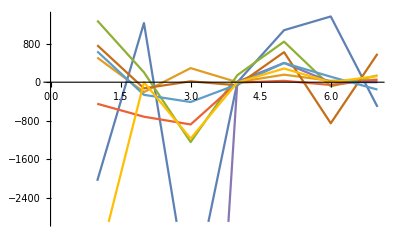

```mathematica
fn[i_]:={a1[1][[i]],a1[2][[i]],a1[3][[i]],a1[4][[i]],a1[5][[i]],a1[6][[i]],a1[7][[i]]}
ListLinePlot[{fn[1],fn[2],fn[3],fn[4],fn[5],fn[6],fn[7],fn[8]}]
```